# Using Graphs to analyze words

## Dictionaries and sets of words

```mathematica
WordData[]
```

```mathematica
DictionaryLookup[___]
```

```mathematica
WordList["KnownWords"]
```

## String Distance

There are several operations that can be used with strings:

Deletions:

```mathematica
StringDelete[StringJoin@Alphabet["Russian"],"э"]
```

абвгдеёжзийклмнопрстуфхцчшщъыьюя

Insertions:

```mathematica
StringInsert[StringJoin@Alphabet["Russian"],"e",{1}]
```

eабвгдеёжзийклмнопрстуфхцчшщъыьэюя

Substitutions:

```mathematica
StringReplace[StringJoin@Alphabet["Russian"],"э"->"z"]
```

абвгдеёжзийклмнопрстуфхцчшщъыьzюя

Transpositions such as “ab”->”ba”

### String Distance Measures and Functions

EditDistance allows for deletions, insertions, and substitutions:

```mathematica
EditDistance["abc","cba"]
```

2

DameruaLevenshteinDistance allows for deletions, insertions, substitutions, and transpositions:

```mathematica
DamerauLevenshteinDistance["abcd","back"]
```

2

HammingDistance gives the number of places where the elements are different:

```mathematica
HammingDistance["abcdeeee","abcdefgh"]
```

3

I will use DameruaLevenshteinDistance.

```mathematica
Select[DamerauLevenshteinDistance[#,"polygon"]==1&][WordList[]]
```

{}

```mathematica
Select[DamerauLevenshteinDistance[#,"cat"]==1&][WordList[]]
```

{act,at,bat,cab,cad,cam,can,cant,cap,car,cart,cast,caw,cay,chat,coat,cot,cut,eat,fat,hat,mat,oat,pat,rat,scat,tat,vat}

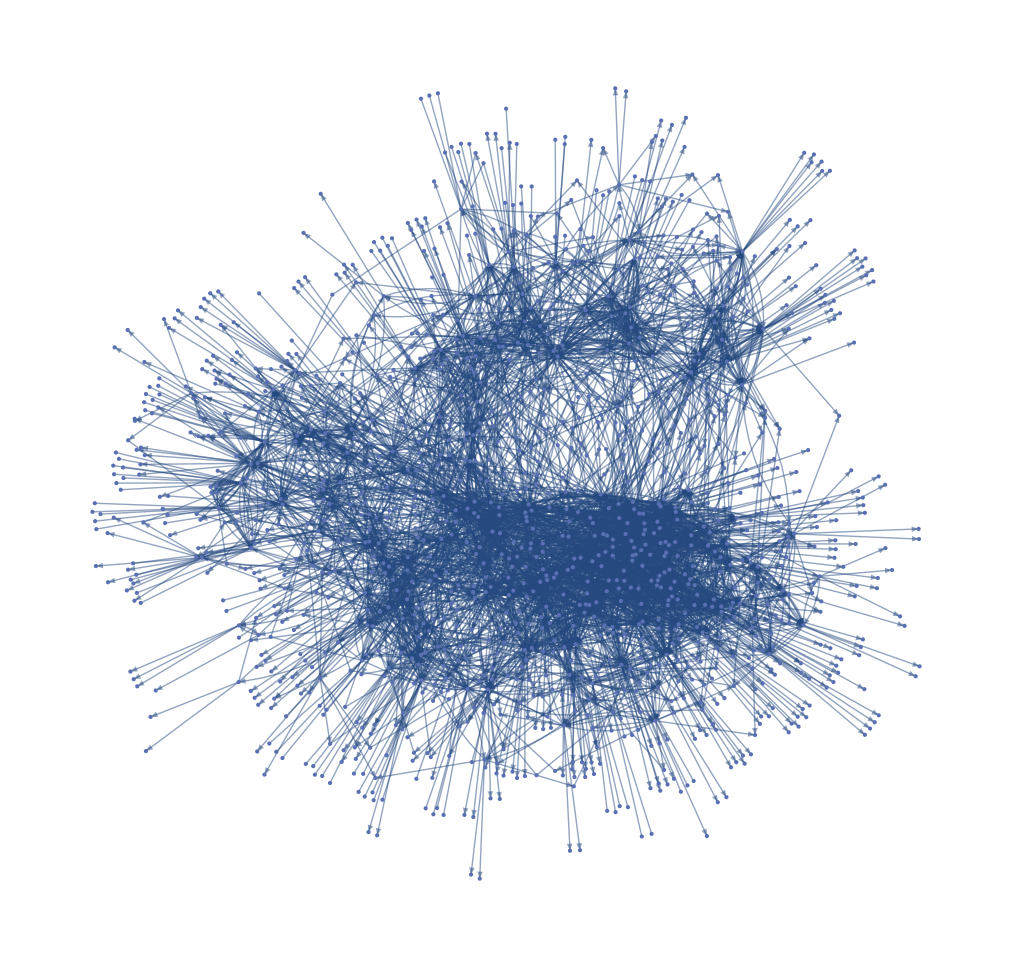

```mathematica
NestGraph[(word↦Select[DamerauLevenshteinDistance[#,word]==1&][WordList[]]),"cat",3]
```

```mathematica
VertexCount[%140]
```

1300

```mathematica
EdgeCount[%140]
```

5255

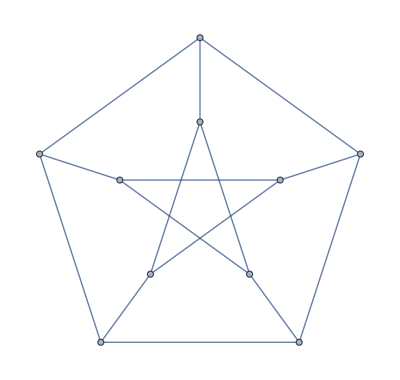

```mathematica
GraphData["PetersenGraph"]
```

```mathematica
GraphData["PetersenGraph","ResistanceMatrix"]
```

SparseArray[…]

GraphData::notprop: "ToroidalForbidden" is not a known property or size specification for GraphData. Use GraphData["Properties"] for a list of properties.

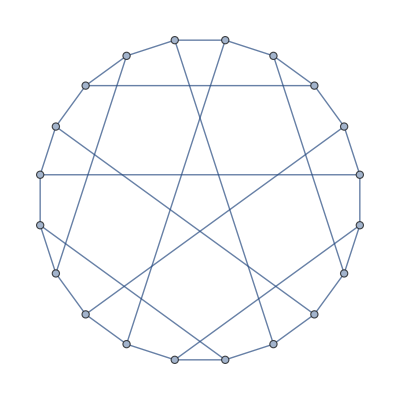
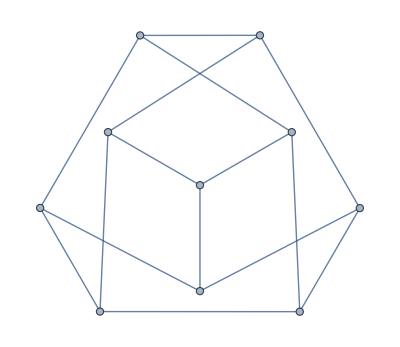
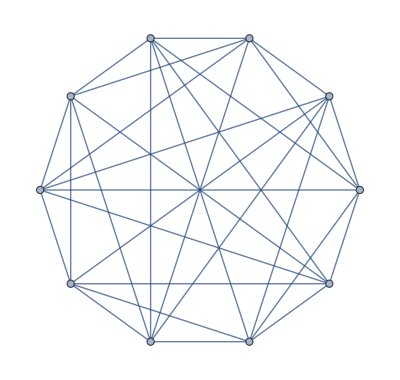
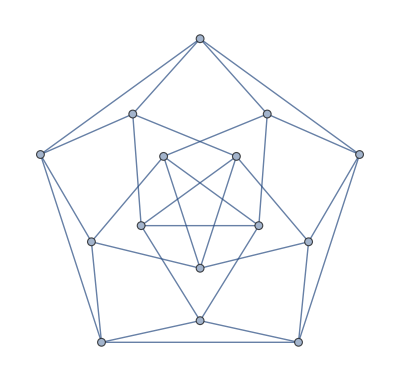
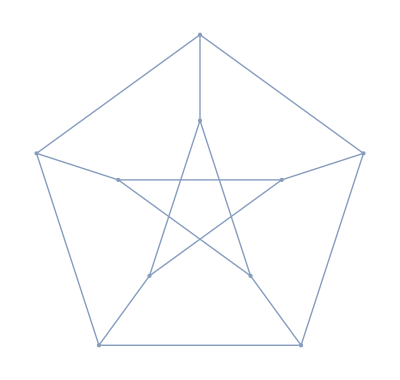
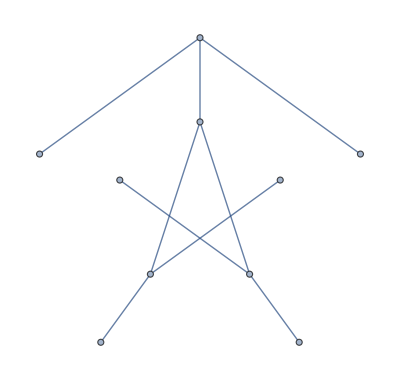
<|Acyclic→False,AdjacencyLists→{{3,4,6},{4,5,7},{1,5,8},{1,2,9},{2,3,10},{1,7,10},{2,6,8},{3,7,9},{4,8,10},{5,6,9}},AdjacencyMatrix→SparseArray[…],AdjacencyMatrixCount→30240,AlgebraicConnectivity→2,Alkane→False,AlmostHamiltonian→True,AlternateNames→{10-arc transitive graph 4,10-cubic graph 19,10-cubic hypohamiltonian graph 1,10-edge-transitive graph 13,10-graph 8428502,10-hypohamiltonian graph 1,10-strong snark 1,10-vertex transitive graph 5,10-weak snark 1,2-crossing number graph A,3-odd graph,(5,1,2)-I graph,(5,2,1)-I graph,(5,2)-generalized Petersen graph,(5,2)-Kneser graph,cubic transitive graph 8},AlternateStandardNames→{{10,8428502},{ArcTransitive,{10,4}},{Cage,{3,5}},CrossingNumberGraph2A,Ct8,{Cubic,{10,19}},{CubicHypohamiltonian,{10,1}},{CubicTransitive,8},{EdgeTransitive,{10,13}},F010A,Foster010A,{GeneralizedPetersen,{5,2}},Gp1,Gp5,2,GP5,2,{Hypohamiltonian,{10,1}},{IGraph,{5,1,2}},{IGraph,{5,2,1}},{Kneser,{5,2}},{LargestRegularNonplanarDiameter,{3,2}},O3,{Odd,3},P,Sn1,{StronglyRegular,{{10,3,0,1},1}},{StrongSnark,{10,1}},{VertexTransitive,{10,5}},{WeakSnark,{10,1}}},AlternateVertexCoordinates→{{{0.323,0.975},{0.037,0.789},{0.037,0.186},{0.323,0.},{0.5,0.487},{1.287,0.975},{1.,0.789},{1.,0.186},{1.287,0.},{1.464,0.487}},{{0.448354,-0.269958},{0.60481,-0.338987},{0.586329,-0.50903},{0.586329,-0.0309114},{0.862447,-0.50903},{0.724304,-0.131983},{0.724304,-0.269958},{0.843797,-0.338987},{0.862447,-0.0309114},{1.,-0.269958}},{{0.448354,-0.269958},{0.606498,-0.145654},{0.529114,-0.0747932},{0.529114,-0.465148},{0.84211,-0.145654},{1.,-0.269958},{0.919831,-0.0747932},{0.724304,0.00606582},{0.724304,-0.545992},{0.919831,-0.465148}},{{0.454407,-0.222966},{0.632542,-0.53161},{0.549237,-0.0587373},{0.487373,-0.409661},{0.822119,-0.53161},{1.,-0.222966},{0.905932,-0.0587373},{0.727373,0.00609153},{0.727373,-0.271102},{0.967797,-0.409661}},{{0.602252,-0.541848},{0.734705,-0.312345},{0.668478,-0.656599},{0.668478,-0.427096},{0.867236,-0.312345},{1.,-0.541848},{0.93323,-0.656599},{0.801242,-0.656599},{0.801242,-0.503571},{0.93323,-0.427096}},{{0,0},{1,3},{0,4},{1,1},{4,4},{2,0},{2,2},{3,3},{3,1},{4,0}},{{2,2},{6,4},{4,2},{2,4},{6,2},{5,5},{6,6},{4,6},{2,6},{3,5}},{{√(2/(5+√5)),0},{1/2 √(1-2/(√5)),1/2},{-1/2 √(1/10 (5+√5)),1/4 (-1+√5)},{-1/2 √(1/10 (5+√5)),1/4 (1-√5)},{1/2 √(1-2/(√5)),-1/2},{0,√(1/10 (5+√5))},{1/4 (-1-√5),1/2 √(1/10 (5-√5))},{-1/2,-1/2 √(1+2/(√5))},{1/2,-1/2 √(1+2/(√5))},{1/4 (1+√5),1/2 √(1/10 (5-√5))}},{{0.535302,0.95889},{0.328164,0.677274},{0.535302,0.470135},{0.0706049,0.621205},{0.328164,0.262996},{1.,0.621205},{0.742441,0.677274},{0.742441,0.262996},{0.247912,0.0745965},{0.822693,0.0745965}},{{√(5/8-(√5)/8),1/4 (-1-√5)},{0,1},{√(1/2 (5-√5)),1/2 (-1-√5)},{√(5/8+(√5)/8),1/4 (-1+√5)},{0,2},{-1/2 √(1/2 (5-√5)),1/4 (-1-√5)},{-1/2 √(1/2 (5+√5)),1/4 (-1+√5)},{-√(1/2 (5+√5)),1/2 (-1+√5)},{√(1/2 (5+√5)),1/2 (-1+√5)},{-√(1/2 (5-√5)),1/2 (-1-√5)}}},AlternatingGroup→False,Anarboricity→Missing[NotAvailable],Andrasfai→False,Antelope→False,Antipodal→False,Antiprism→False,Apex→False,ApexCount→0,Apices→{},Apollonian→False,Arboricity→2,Archimedean→False,ArchimedeanDual→False,ArcTransitive→True,ArcTransitivity→3,Arrangement→False,ArticulationVertexCount→0,ArticulationVertices→{},Asymmetric→False,AutomorphismCount→120,AutomorphismGroup→PermutationGroup[{Cycles[{{2,7},{4,6},{5,8},{9,10}}],Cycles[{{2,9},{5,8},{7,10}}],Cycles[{{2,5},{3,4},{7,10},{8,9}}],Cycles[{{1,2,3,4,5},{6,7,8,9,10}}]}],BalabanIndex→15/7,BananaTree→False,Bandwidth→5,Barbell→False,Beineke→False,BetweennessCentralities→{3,3,3,3,3,3,3,3,3,3},BicliqueCover→Missing[NotAvailable],Bicolorable→False,Biconnected→True,Bicubic→False,Bipartite→False,BipartiteDimension→Missing[NotAvailable],BipartiteDoubleGraph→-Graphics-,BipartiteKneser→False,Biplanar→True,Bishop→False,BlackBishop→False,BlockCount→1,Blocks→{-Graphics-},Book→False,Bouwer→False,BracedPolygon→False,BridgeCount→0,Bridged→False,Bridgeless→True,Bridges→{},BroadcastTime→Missing[NotAvailable],BroadcastTimes→Missing[NotAvailable],Bruhat→False,BurningNumber→3,Cactus→False,Cage→True,Camel→False,CanonicalForm→{{3,4,7},{3,5,8},{1,2,9},{1,6,8},{2,6,7},{4,5,9},{1,5,10},{2,4,10},{3,6,10},{7,8,9}},CanonicalGraph→-Graphics-,Caterpillar→False,Caveman→False,Cayley→False,CayleyGraphGeneratingGroupNames→Missing[NotApplicable],CayleyGraphGeneratingGroups→Missing[NotApplicable],Center→{1,2,3,4,5,6,7,8,9,10},Centipede→False,Chang→False,CharacteristicPolynomial→((-3+#1) (-1+#1)^5 (2+#1)^4&),CheegerConstant→Missing[NotAvailable],Chordal→False,ChordCount→15,Chordless→False,ChordlessCycleCount→22,ChordlessCyclePolynomial→(12 #1^5+10 #1^6&),ChordlessCycles→{{1,3,5,2,4},{1,3,5,10,6},{1,3,8,7,6},{1,3,8,9,4},{1,4,2,7,6},{1,4,9,10,6},{2,4,9,8,7},{2,4,9,10,5},{2,5,3,8,7},{2,5,10,6,7},{3,5,10,9,8},{6,7,8,9,10},{1,3,5,2,7,6},{1,3,5,10,9,4},{1,3,8,7,2,4},{1,3,8,9,10,6},{1,4,2,5,10,6},{1,4,9,8,7,6},{2,4,9,8,3,5},{2,4,9,10,6,7},{2,5,10,9,8,7},{3,5,10,6,7,8}},Chords→{1<->3,1<->4,1<->6,2<->4,2<->5,2<->7,3<->5,3<->8,4<->9,5<->10,6<->7,6<->10,7<->8,8<->9,9<->10},ChromaticallyNonunique→False,ChromaticallyUnique→True,ChromaticInvariant→36,ChromaticNumber→3,ChromaticPolynomial→((-2+#1) (-1+#1) #1 (-352+775 #1-814 #1^2+529 #1^3-230 #1^4+67 #1^5-12 #1^6+#1^7)&),CircuitRank→6,Circulant→False,Circumference→9,Class1→False,Class2→True,Classes→{AlmostHamiltonian,ArcTransitive,Biconnected,Biplanar,Bridgeless,Cage,ChromaticallyUnique,Class2,Connected,Cubic,Cyclic,DeterminedByResistance,DeterminedBySpectrum,DistanceRegular,DistanceTransitive,Doublecross,EdgeTransitive,GeneralizedPetersen,Geodetic,Graceful,Hypohamiltonian,IGraph,Imperfect,Integral,Kneser,Local,MaximallyNonhamiltonian,Moore,Noncayley,Nonempty,Noneulerian,Nonhamiltonian,Nonplanar,Odd,PerfectMatching,ProjectivePlanar,Regular,Simple,Snark,SquareFree,StronglyRegular,Symmetric,Toroidal,Traceable,TriangleFree,UnitDistance,VertexTransitive,WeakSnark},ClawFree→False,CliqueCount→26,CliqueCoveringNumber→5,CliqueNumber→2,CliquePolynomial→(1+10 #1+15 #1^2&),Cliques→{{},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{1,3},{1,4},{1,6},{2,4},{2,5},{2,7},{3,5},{3,8},{4,9},{5,10},{6,7},{6,10},{7,8},{8,9},{9,10}},ClosenessCentralities→{3/5,3/5,3/5,3/5,3/5,3/5,3/5,3/5,3/5,3/5},Coarseness→Missing[NotAvailable],CoboundaryPolynomial→(-704+2606 #1-4305 #1^2+4275 #1^3-2861 #1^4+1353 #1^5-455 #1^6+105 #1^7-15 #1^8+#1^9+5640 #2-19350 #1 #2+28845 #1^2 #2-25080 #1^3 #2+14175 #1^4 #2-5400 #1^5 #2+1365 #1^6 #2-210 #1^7 #2+15 #1^8 #2-19470 #2^2+61455 #1 #2^2-81570 #1^2 #2^2+60735 #1^3 #2^2-27960 #1^4 #2^2+8070 #1^5 #2^2-1365 #1^6 #2^2+105 #1^7 #2^2+37435 #2^3-107665 #1 #2^3+124935 #1^2 #2^3-77130 #1^3 #2^3+27310 #1^4 #2^3-5340 #1^5 #2^3+455 #1^6 #2^3-42930 #2^4+110970 #1 #2^4-109515 #1^2 #2^4+53175 #1^3 #2^4-13005 #1^4 #2^4+1305 #1^5 #2^4+28584 #2^5-64872 #1 #2^5+51765 #1^2 #2^5-17700 #1^3 #2^5+2211 #1^4 #2^5+12 #1^5 #2^5-9100 #2^6+17010 #1 #2^6-9345 #1^2 #2^6+1305 #1^3 #2^6+130 #1^4 #2^6-45 #2^7+810 #1 #2^7-1155 #1^2 #2^7+390 #1^3 #2^7+540 #2^8-810 #1 #2^8+240 #1^2 #2^8+30 #1^3 #2^8+80 #2^9-170 #1 #2^9+90 #1^2 #2^9-6 #2^10-9 #1 #2^10+15 #1^2 #2^10-15 #2^11+15 #1 #2^11-10 #2^12+10 #1 #2^12+#2^15&),CochromaticGraphs→{},CocktailParty→False,ComplementGraph→-Graphics-,ComplementOddChordlessCycleCount→12,ComplementOddChordlessCyclePolynomial→(12 #1^5&),ComplementOddChordlessCycles→{{1,2,3,4,5},{1,2,6,4,7},{1,5,6,3,10},{1,7,3,6,8},{1,8,4,3,9},{1,9,6,4,10},{2,6,5,7,10},{2,8,4,7,9},{2,9,5,4,10},{3,2,8,5,7},{3,9,5,8,10},{6,8,10,7,9}},Complete→False,CompleteBipartite→False,CompleteKPartite→False,CompletelyRegular→False,CompleteTree→False,CompleteTripartite→False,Conductance→Missing[NotAvailable],Cone→False,Conference→False,Connected→True,ConnectedComponentCount→1,ConnectedComponents→{-Graphics-},ConnectedDominatingSetCount→383,ConnectedDominatingSets→{{1,2,4,9},{1,3,4,6},{1,3,5,8},{1,6,7,10},{2,3,5,10},{2,4,5,7},{2,6,7,8},{3,7,8,9},{4,8,9,10},{5,6,9,10},{1,2,3,4,5},{1,2,3,4,6},{1,2,3,4,9},{1,2,3,5,8},{1,2,3,5,10},{1,2,4,5,7},{1,2,4,5,9},{1,2,4,6,7},{1,2,4,6,9},{1,2,4,7,9},{1,2,4,8,9},{1,2,4,9,10},{1,2,6,7,8},{1,2,6,7,10},{1,3,4,5,6},{1,3,4,5,8},{1,3,4,6,7},{1,3,4,6,8},{1,3,4,6,9},{1,3,4,6,10},{1,3,4,8,9},{1,3,5,6,8},{1,3,5,6,10},{1,3,5,7,8},{1,3,5,8,9},{1,3,5,8,10},{1,3,6,7,8},{1,3,6,7,10},{1,3,7,8,9},{1,4,6,7,10},{1,4,6,9,10},{1,4,8,9,10},{1,5,6,7,10},{1,5,6,9,10},{1,6,7,8,10},{1,6,7,9,10},{2,3,4,5,7},{2,3,4,5,10},{2,3,5,6,10},{2,3,5,7,8},{2,3,5,7,10},{2,3,5,8,10},{2,3,5,9,10},{2,3,6,7,8},{2,3,7,8,9},{2,4,5,6,7},{2,4,5,7,8},{2,4,5,7,9},{2,4,5,7,10},{2,4,5,9,10},{2,4,6,7,8},{2,4,7,8,9},{2,4,8,9,10},{2,5,6,7,8},{2,5,6,7,10},{2,5,6,9,10},{2,6,7,8,9},{2,6,7,8,10},{3,4,7,8,9},{3,4,8,9,10},{3,5,6,9,10},{3,5,7,8,9},{3,5,8,9,10},{3,6,7,8,9},{3,7,8,9,10},{4,5,6,9,10},{4,5,8,9,10},{4,6,8,9,10},{4,7,8,9,10},{5,6,7,9,10},{5,6,8,9,10},{6,7,8,9,10},{1,2,3,4,5,6},{1,2,3,4,5,7},{1,2,3,4,5,8},{1,2,3,4,5,9},{1,2,3,4,5,10},{1,2,3,4,6,7},{1,2,3,4,6,8},{1,2,3,4,6,9},{1,2,3,4,6,10},{1,2,3,4,7,9},{1,2,3,4,8,9},{1,2,3,4,9,10},{1,2,3,5,6,8},{1,2,3,5,6,10},{1,2,3,5,7,8},{1,2,3,5,7,10},{1,2,3,5,8,9},{1,2,3,5,8,10},{1,2,3,5,9,10},{1,2,3,6,7,8},{1,2,3,6,7,10},{1,2,3,7,8,9},{1,2,4,5,6,7},{1,2,4,5,6,9},{1,2,4,5,7,8},{1,2,4,5,7,9},{1,2,4,5,7,10},{1,2,4,5,8,9},{1,2,4,5,9,10},{1,2,4,6,7,8},{1,2,4,6,7,9},{1,2,4,6,7,10},{1,2,4,6,8,9},{1,2,4,6,9,10},{1,2,4,7,8,9},{1,2,4,7,9,10},{1,2,4,8,9,10},{1,2,5,6,7,8},{1,2,5,6,7,10},{1,2,5,6,9,10},{1,2,6,7,8,9},{1,2,6,7,8,10},{1,2,6,7,9,10},{1,3,4,5,6,7},{1,3,4,5,6,8},{1,3,4,5,6,9},{1,3,4,5,6,10},{1,3,4,5,7,8},{1,3,4,5,8,9},{1,3,4,5,8,10},{1,3,4,6,7,8},{1,3,4,6,7,9},{1,3,4,6,7,10},{1,3,4,6,8,9},{1,3,4,6,8,10},{1,3,4,6,9,10},{1,3,4,7,8,9},{1,3,4,8,9,10},{1,3,5,6,7,8},{1,3,5,6,7,10},{1,3,5,6,8,9},{1,3,5,6,8,10},{1,3,5,6,9,10},{1,3,5,7,8,9},{1,3,5,7,8,10},{1,3,5,8,9,10},{1,3,6,7,8,9},{1,3,6,7,8,10},{1,3,6,7,9,10},{1,3,7,8,9,10},{1,4,5,6,7,10},{1,4,5,6,9,10},{1,4,5,8,9,10},{1,4,6,7,8,10},{1,4,6,7,9,10},{1,4,6,8,9,10},{1,4,7,8,9,10},{1,5,6,7,8,10},{1,5,6,7,9,10},{1,5,6,8,9,10},{1,6,7,8,9,10},{2,3,4,5,6,7},{2,3,4,5,6,10},{2,3,4,5,7,8},{2,3,4,5,7,9},{2,3,4,5,7,10},{2,3,4,5,8,10},{2,3,4,5,9,10},{2,3,4,6,7,8},{2,3,4,7,8,9},{2,3,4,8,9,10},{2,3,5,6,7,8},{2,3,5,6,7,10},{2,3,5,6,8,10},{2,3,5,6,9,10},{2,3,5,7,8,9},{2,3,5,7,8,10},{2,3,5,7,9,10},{2,3,5,8,9,10},{2,3,6,7,8,9},{2,3,6,7,8,10},{2,3,7,8,9,10},{2,4,5,6,7,8},{2,4,5,6,7,9},{2,4,5,6,7,10},{2,4,5,6,9,10},{2,4,5,7,8,9},{2,4,5,7,8,10},{2,4,5,7,9,10},{2,4,5,8,9,10},{2,4,6,7,8,9},{2,4,6,7,8,10},{2,4,6,8,9,10},{2,4,7,8,9,10},{2,5,6,7,8,9},{2,5,6,7,8,10},{2,5,6,7,9,10},{2,5,6,8,9,10},{2,6,7,8,9,10},{3,4,5,6,9,10},{3,4,5,7,8,9},{3,4,5,8,9,10},{3,4,6,7,8,9},{3,4,6,8,9,10},{3,4,7,8,9,10},{3,5,6,7,8,9},{3,5,6,7,9,10},{3,5,6,8,9,10},{3,5,7,8,9,10},{3,6,7,8,9,10},{4,5,6,7,9,10},{4,5,6,8,9,10},{4,5,7,8,9,10},{4,6,7,8,9,10},{5,6,7,8,9,10},{1,2,3,4,5,6,7},{1,2,3,4,5,6,8},{1,2,3,4,5,6,9},{1,2,3,4,5,6,10},{1,2,3,4,5,7,8},{1,2,3,4,5,7,9},{1,2,3,4,5,7,10},{1,2,3,4,5,8,9},{1,2,3,4,5,8,10},{1,2,3,4,5,9,10},{1,2,3,4,6,7,8},{1,2,3,4,6,7,9},{1,2,3,4,6,7,10},{1,2,3,4,6,8,9},{1,2,3,4,6,8,10},{1,2,3,4,6,9,10},{1,2,3,4,7,8,9},{1,2,3,4,7,9,10},{1,2,3,4,8,9,10},{1,2,3,5,6,7,8},{1,2,3,5,6,7,10},{1,2,3,5,6,8,9},{1,2,3,5,6,8,10},{1,2,3,5,6,9,10},{1,2,3,5,7,8,9},{1,2,3,5,7,8,10},{1,2,3,5,7,9,10},{1,2,3,5,8,9,10},{1,2,3,6,7,8,9},{1,2,3,6,7,8,10},{1,2,3,6,7,9,10},{1,2,3,7,8,9,10},{1,2,4,5,6,7,8},{1,2,4,5,6,7,9},{1,2,4,5,6,7,10},{1,2,4,5,6,8,9},{1,2,4,5,6,9,10},{1,2,4,5,7,8,9},{1,2,4,5,7,8,10},{1,2,4,5,7,9,10},{1,2,4,5,8,9,10},{1,2,4,6,7,8,9},{1,2,4,6,7,8,10},{1,2,4,6,7,9,10},{1,2,4,6,8,9,10},{1,2,4,7,8,9,10},{1,2,5,6,7,8,9},{1,2,5,6,7,8,10},{1,2,5,6,7,9,10},{1,2,5,6,8,9,10},{1,2,6,7,8,9,10},{1,3,4,5,6,7,8},{1,3,4,5,6,7,9},{1,3,4,5,6,7,10},{1,3,4,5,6,8,9},{1,3,4,5,6,8,10},{1,3,4,5,6,9,10},{1,3,4,5,7,8,9},{1,3,4,5,7,8,10},{1,3,4,5,8,9,10},{1,3,4,6,7,8,9},{1,3,4,6,7,8,10},{1,3,4,6,7,9,10},{1,3,4,6,8,9,10},{1,3,4,7,8,9,10},{1,3,5,6,7,8,9},{1,3,5,6,7,8,10},{1,3,5,6,7,9,10},{1,3,5,6,8,9,10},{1,3,5,7,8,9,10},{1,3,6,7,8,9,10},{1,4,5,6,7,8,10},{1,4,5,6,7,9,10},{1,4,5,6,8,9,10},{1,4,5,7,8,9,10},{1,4,6,7,8,9,10},{1,5,6,7,8,9,10},{2,3,4,5,6,7,8},{2,3,4,5,6,7,9},{2,3,4,5,6,7,10},{2,3,4,5,6,8,10},{2,3,4,5,6,9,10},{2,3,4,5,7,8,9},{2,3,4,5,7,8,10},{2,3,4,5,7,9,10},{2,3,4,5,8,9,10},{2,3,4,6,7,8,9},{2,3,4,6,7,8,10},{2,3,4,6,8,9,10},{2,3,4,7,8,9,10},{2,3,5,6,7,8,9},{2,3,5,6,7,8,10},{2,3,5,6,7,9,10},{2,3,5,6,8,9,10},{2,3,5,7,8,9,10},{2,3,6,7,8,9,10},{2,4,5,6,7,8,9},{2,4,5,6,7,8,10},{2,4,5,6,7,9,10},{2,4,5,6,8,9,10},{2,4,5,7,8,9,10},{2,4,6,7,8,9,10},{2,5,6,7,8,9,10},{3,4,5,6,7,8,9},{3,4,5,6,7,9,10},{3,4,5,6,8,9,10},{3,4,5,7,8,9,10},{3,4,6,7,8,9,10},{3,5,6,7,8,9,10},{4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,9},{1,2,3,4,5,6,7,10},{1,2,3,4,5,6,8,9},{1,2,3,4,5,6,8,10},{1,2,3,4,5,6,9,10},{1,2,3,4,5,7,8,9},{1,2,3,4,5,7,8,10},{1,2,3,4,5,7,9,10},{1,2,3,4,5,8,9,10},{1,2,3,4,6,7,8,9},{1,2,3,4,6,7,8,10},{1,2,3,4,6,7,9,10},{1,2,3,4,6,8,9,10},{1,2,3,4,7,8,9,10},{1,2,3,5,6,7,8,9},{1,2,3,5,6,7,8,10},{1,2,3,5,6,7,9,10},{1,2,3,5,6,8,9,10},{1,2,3,5,7,8,9,10},{1,2,3,6,7,8,9,10},{1,2,4,5,6,7,8,9},{1,2,4,5,6,7,8,10},{1,2,4,5,6,7,9,10},{1,2,4,5,6,8,9,10},{1,2,4,5,7,8,9,10},{1,2,4,6,7,8,9,10},{1,2,5,6,7,8,9,10},{1,3,4,5,6,7,8,9},{1,3,4,5,6,7,8,10},{1,3,4,5,6,7,9,10},{1,3,4,5,6,8,9,10},{1,3,4,5,7,8,9,10},{1,3,4,6,7,8,9,10},{1,3,5,6,7,8,9,10},{1,4,5,6,7,8,9,10},{2,3,4,5,6,7,8,9},{2,3,4,5,6,7,8,10},{2,3,4,5,6,7,9,10},{2,3,4,5,6,8,9,10},{2,3,4,5,7,8,9,10},{2,3,4,6,7,8,9,10},{2,3,5,6,7,8,9,10},{2,4,5,6,7,8,9,10},{3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,10},{1,2,3,4,5,6,7,9,10},{1,2,3,4,5,6,8,9,10},{1,2,3,4,5,7,8,9,10},{1,2,3,4,6,7,8,9,10},{1,2,3,5,6,7,8,9,10},{1,2,4,5,6,7,8,9,10},{1,3,4,5,6,7,8,9,10},{2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10}},ConnectedDominationNumber→4,ConnectedDominationPolynomial→(10 #1^4+72 #1^5+135 #1^6+110 #1^7+45 #1^8+10 #1^9+#1^10&),ConnectedInducedSubgraphCount→568,ConnectedInducedSubgraphPolynomial→(10 #1+15 #1^2+30 #1^3+70 #1^4+132 #1^5+145 #1^6+110 #1^7+45 #1^8+10 #1^9+#1^10&),Corank→6,CoresistanceGraphs→{},CospectralGraphs→{},CriticalNonplanar→False,CrossedPrism→False,CrossingNumber→2,Crown→False,CubeConnectedCycle→False,Cubic→True,Cycle→False,CycleComplement→False,CycleCount→57,CyclePolynomial→(12 #1^5+10 #1^6+15 #1^8+20 #1^9&),Cycles→{{1,3,5,2,4},{1,3,5,10,6},{1,3,8,7,6},{1,3,8,9,4},{1,4,2,7,6},{1,4,9,10,6},{2,4,9,8,7},{2,4,9,10,5},{2,5,3,8,7},{2,5,10,6,7},{3,5,10,9,8},{6,7,8,9,10},{1,3,5,2,7,6},{1,3,5,10,9,4},{1,3,8,7,2,4},{1,3,8,9,10,6},{1,4,2,5,10,6},{1,4,9,8,7,6},{2,4,9,8,3,5},{2,4,9,10,6,7},{2,5,10,9,8,7},{3,5,10,6,7,8},{1,3,5,2,4,9,10,6},{1,3,5,2,7,8,9,4},{1,3,5,10,6,7,2,4},{1,3,5,10,9,8,7,6},{1,3,8,7,2,5,10,6},{1,3,8,7,6,10,9,4},{1,3,8,9,4,2,7,6},{1,3,8,9,10,5,2,4},{1,4,2,5,3,8,7,6},{1,4,2,7,8,9,10,6},{1,4,9,8,3,5,10,6},{1,4,9,10,5,2,7,6},{2,4,9,8,7,6,10,5},{2,4,9,10,5,3,8,7},{2,5,3,8,9,10,6,7},{1,3,5,2,4,9,8,7,6},{1,3,5,2,7,6,10,9,4},{1,3,5,2,7,8,9,10,6},{1,3,5,10,6,7,8,9,4},{1,3,5,10,9,4,2,7,6},{1,3,5,10,9,8,7,2,4},{1,3,8,7,2,4,9,10,6},{1,3,8,7,2,5,10,9,4},{1,3,8,7,6,10,5,2,4},{1,3,8,9,4,2,5,10,6},{1,3,8,9,10,5,2,7,6},{1,3,8,9,10,6,7,2,4},{1,4,2,5,3,8,9,10,6},{1,4,2,5,10,9,8,7,6},{1,4,2,7,8,3,5,10,6},{1,4,9,8,3,5,2,7,6},{1,4,9,8,7,2,5,10,6},{1,4,9,10,5,3,8,7,6},{2,4,9,8,3,5,10,6,7},{2,4,9,10,6,7,8,3,5}},Cyclic→True,CyclicEdgeConnectivity→5,Cyclotomic→False,Degeneracy→Missing[NotAvailable],DegreeCentralities→{3,3,3,3,3,3,3,3,3,3},DegreeSequence→{3,3,3,3,3,3,3,3,3,3},DeterminedByResistance→True,DeterminedBySpectrum→True,DetourIndex→390,DetourMatrix→{{0,9,8,8,9,8,9,9,9,9},{9,0,9,8,8,9,8,9,9,9},{8,9,0,9,8,9,9,8,9,9},{8,8,9,0,9,9,9,9,8,9},{9,8,8,9,0,9,9,9,9,8},{8,9,9,9,9,0,8,9,9,8},{9,8,9,9,9,8,0,8,9,9},{9,9,8,9,9,9,8,0,8,9},{9,9,9,8,9,9,9,8,0,8},{9,9,9,9,8,8,9,9,8,0}},DetourPolynomial→((-78+#1) (7+#1)^4 (10+#1)^5&),DiagonalIntersection→False,Diameter→2,Dimension→2,Dipyramid→False,Disconnected→False,DistanceMatrix→SparseArray[…],DistancePolynomial→((-15+#1) #1^4 (3+#1)^5&),DistanceRegular→True,DistanceTransitive→True,DistinguishingNumber→3,DomaticNumber→2,DominatingSetCount→653,DominatingSets→Missing[TooLarge,{1,2,9}],DominationNumber→3,DominationPolynomial→(#1^3 (10+75 #1+192 #1^2+200 #1^3+120 #1^4+45 #1^5+10 #1^6+#1^7)&),Doob→False,Doublecross→True,DoubleToroidal→False,DualGraph→Missing[NotAvailable],DutchWindmill→False,Eccentricities→{2,2,2,2,2,2,2,2,2,2},EccentricityCentralities→{1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2},EdgeBetweennessCentralities→{10,10,10,10,10,10,10,10,10,10,10,10,10,10,10},EdgeChromaticNumber→4,EdgeConnectivity→3,EdgeCount→15,EdgeCoverCount→10870,EdgeCoverNumber→5,EdgeCoverPolynomial→(#1^5 (6+215 #1+1095 #1^2+2400 #1^3+2985 #1^4+2358 #1^5+1245 #1^6+445 #1^7+105 #1^8+15 #1^9+#1^10)&),EdgeCovers→Missing[TooLarge,{1<->6,2<->7,3<->8,4<->9,5<->10}],EdgeCutCount→26800,EdgeCutPolynomial→(10 #1^3+135 #1^4+831 #1^5+3005 #1^6+6435 #1^7+6435 #1^8+5005 #1^9+3003 #1^10+1365 #1^11+455 #1^12+105 #1^13+15 #1^14+#1^15&),EdgeCuts→Missing[TooLarge,{1<->3,1<->4,1<->6}],Edges→{1<->3,1<->4,1<->6,2<->4,2<->5,2<->7,3<->5,3<->8,4<->9,5<->10,6<->7,6<->10,7<->8,8<->9,9<->10},EdgeTransitive→True,Egawa→False,EigenvectorCentralities→{1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10},EmbeddingClasses→{{GeneralizedPetersen,IGraph,Primary},{},{},{},{},{},{IntegerCoordinates,MinimalCrossing,MinimalRectilinearCrossing},{IntegerCoordinates},{Integral,MinimalIntegral,UnitDistance},{MinimalCrossing,MinimalRectilinearCrossing},{IGraph}},Embeddings→{{{0.,1.},{-0.951,0.309},{-0.588,-0.809},{0.588,-0.809},{0.951,0.309},{0.,2.},{-1.902,0.618},{-1.176,-1.618},{1.176,-1.618},{1.902,0.618}},{{0.323,0.975},{0.037,0.789},{0.037,0.186},{0.323,0.},{0.5,0.487},{1.287,0.975},{1.,0.789},{1.,0.186},{1.287,0.},{1.464,0.487}},{{0.448354,-0.269958},{0.60481,-0.338987},{0.586329,-0.50903},{0.586329,-0.0309114},{0.862447,-0.50903},{0.724304,-0.131983},{0.724304,-0.269958},{0.843797,-0.338987},{0.862447,-0.0309114},{1.,-0.269958}},{{0.448354,-0.269958},{0.606498,-0.145654},{0.529114,-0.0747932},{0.529114,-0.465148},{0.84211,-0.145654},{1.,-0.269958},{0.919831,-0.0747932},{0.724304,0.00606582},{0.724304,-0.545992},{0.919831,-0.465148}},{{0.454407,-0.222966},{0.632542,-0.53161},{0.549237,-0.0587373},{0.487373,-0.409661},{0.822119,-0.53161},{1.,-0.222966},{0.905932,-0.0587373},{0.727373,0.00609153},{0.727373,-0.271102},{0.967797,-0.409661}},{{0.602252,-0.541848},{0.734705,-0.312345},{0.668478,-0.656599},{0.668478,-0.427096},{0.867236,-0.312345},{1.,-0.541848},{0.93323,-0.656599},{0.801242,-0.656599},{0.801242,-0.503571},{0.93323,-0.427096}},{{0,0},{1,3},{0,4},{1,1},{4,4},{2,0},{2,2},{3,3},{3,1},{4,0}},{{2,2},{6,4},{4,2},{2,4},{6,2},{5,5},{6,6},{4,6},{2,6},{3,5}},{{√(2/(5+√5)),0},{1/2 √(1-2/(√5)),1/2},{-1/2 √(1/10 (5+√5)),1/4 (-1+√5)},{-1/2 √(1/10 (5+√5)),1/4 (1-√5)},{1/2 √(1-2/(√5)),-1/2},{0,√(1/10 (5+√5))},{1/4 (-1-√5),1/2 √(1/10 (5-√5))},{-1/2,-1/2 √(1+2/(√5))},{1/2,-1/2 √(1+2/(√5))},{1/4 (1+√5),1/2 √(1/10 (5-√5))}},{{0.535302,0.95889},{0.328164,0.677274},{0.535302,0.470135},{0.0706049,0.621205},{0.328164,0.262996},{1.,0.621205},{0.742441,0.677274},{0.742441,0.262996},{0.247912,0.0745965},{0.822693,0.0745965}},{{√(5/8-(√5)/8),1/4 (-1-√5)},{0,1},{√(1/2 (5-√5)),1/2 (-1-√5)},{√(5/8+(√5)/8),1/4 (-1+√5)},{0,2},{-1/2 √(1/2 (5-√5)),1/4 (-1-√5)},{-1/2 √(1/2 (5+√5)),1/4 (-1+√5)},{-√(1/2 (5+√5)),1/2 (-1+√5)},{√(1/2 (5+√5)),1/2 (-1+√5)},{-√(1/2 (5-√5)),1/2 (-1-√5)}}},Empty→False,Entity→Petersen graph,Eulerian→False,EulerianCycleCount→0,EulerianCycles→{},FaceCount→Missing[NotApplicable],Faces→Missing[NotApplicable],FaceSignature→Missing[NotApplicable],Fan→False,FibonacciCube→False,Firecracker→False,Fiveleaper→False,Flower→False,FlowPolynomial→((-4+#1) (-3+#1) (-2+#1) (-1+#1) (10-5 #1+#1^2)&),FoldedCube→False,Forest→False,FractionalArboricity→Missing[NotAvailable],FractionalChromaticNumber→5/2,FractionalCliqueNumber→5/2,FractionalEdgeChromaticNumber→3,Fullerene→False,Fusene→False,Gear→False,GeneralizedPetersen→True,GeneralizedPolygon→False,Genus→1,Geodetic→True,Giraffe→False,Girth→5,GlobalClusteringCoefficient→0,GoethalsSeidelBlockDesign→False,Goldberg→False,Gonality→Missing[NotAvailable],Graceful→True,GracefulLabelingCount→42,GracefulLabelings→{{0,1,2,14,10,15,4,8,13,3},{0,1,2,14,10,15,12,8,13,3},{0,1,2,14,13,15,11,3,9,6},{0,1,2,15,7,13,9,12,3,14},{0,1,2,15,12,5,14,10,3,6},{0,1,2,15,13,4,14,9,6,12},{0,1,3,15,8,10,12,11,2,14},{0,1,3,15,9,12,8,13,2,11},{0,1,3,15,11,9,8,14,2,7},{0,1,4,15,10,13,2,14,12,5},{0,1,4,15,12,5,8,14,2,3},{0,1,4,15,14,9,12,6,7,2},{0,1,4,15,14,12,9,10,8,3},{0,1,5,14,7,15,4,12,2,6},{0,1,5,15,7,11,4,14,2,3},{0,1,5,15,11,7,3,14,2,10},{0,1,5,15,11,13,9,12,14,2},{0,1,5,15,14,10,12,8,9,2},{0,1,5,15,14,10,12,9,8,2},{0,1,5,15,14,10,12,11,3,7},{0,1,5,15,14,10,13,12,4,8},{0,1,6,15,8,13,10,2,14,3},{0,1,6,15,14,9,12,10,3,4},{0,1,6,15,14,12,11,2,4,7},{0,1,7,15,13,10,12,3,2,5},{0,1,7,15,13,10,12,11,2,5},{0,1,8,15,3,12,5,11,2,13},{0,1,8,15,11,13,6,12,14,2},{0,1,8,15,14,9,12,13,3,7},{0,1,8,15,14,9,13,3,4,7},{0,1,8,15,14,9,13,3,4,11},{0,1,8,15,14,11,13,3,6,7},{0,1,9,15,7,11,4,14,2,3},{0,1,10,15,4,13,2,14,6,11},{0,1,10,15,5,11,3,9,2,14},{0,1,10,15,5,11,9,3,2,14},{0,1,10,15,7,13,5,12,3,2},{0,1,10,15,12,13,4,11,3,7},{0,1,12,15,3,13,5,2,9,14},{0,1,12,15,5,13,11,3,4,10},{0,1,12,15,5,13,11,3,14,8},{0,1,12,15,8,13,4,6,14,3}},Graph→-Graphics-,Graphics→-Graphics-,Graphics3D→-Graphics3D-,Grassmann→False,Grid→False,Haar→False,Hadamard→False,HadwigerNumber→5,Halin→False,HalvedCube→False,HamiltonConnected→False,HamiltonDecomposable→False,HamiltonDecompositionCount→Missing[NotApplicable],HamiltonDecompositions→Missing[NotApplicable],Hamiltonian→False,HamiltonianCycleCount→0,HamiltonianCycles→{},HamiltonianNumber→11,HamiltonianPathCount→120,HamiltonianPaths→{{1,3,5,2,4,9,8,7,6,10},{1,3,5,2,4,9,10,6,7,8},{1,3,5,10,6,7,2,4,9,8},{1,3,5,10,6,7,8,9,4,2},{1,3,8,7,6,10,5,2,4,9},{1,3,8,7,6,10,9,4,2,5},{1,3,8,9,4,2,5,10,6,7},{1,3,8,9,4,2,7,6,10,5},{1,4,2,5,3,8,7,6,10,9},{1,4,2,5,3,8,9,10,6,7},{1,4,2,7,6,10,5,3,8,9},{1,4,2,7,6,10,9,8,3,5},{1,4,9,8,3,5,2,7,6,10},{1,4,9,8,3,5,10,6,7,2},{1,4,9,10,6,7,2,5,3,8},{1,4,9,10,6,7,8,3,5,2},{1,6,7,2,4,9,8,3,5,10},{1,6,7,2,4,9,10,5,3,8},{1,6,7,8,3,5,2,4,9,10},{1,6,7,8,3,5,10,9,4,2},{1,6,10,5,3,8,7,2,4,9},{1,6,10,5,3,8,9,4,2,7},{1,6,10,9,4,2,5,3,8,7},{1,6,10,9,4,2,7,8,3,5},{2,4,1,3,5,10,6,7,8,9},{2,4,1,3,5,10,9,8,7,6},{2,4,1,6,7,8,3,5,10,9},{2,4,1,6,7,8,9,10,5,3},{2,4,9,8,7,6,1,3,5,10},{2,4,9,10,5,3,1,6,7,8},{2,5,3,1,4,9,8,7,6,10},{2,5,3,1,4,9,10,6,7,8},{2,5,3,8,7,6,1,4,9,10},{2,5,10,6,7,8,3,1,4,9},{2,5,10,6,7,8,9,4,1,3},{2,5,10,9,4,1,3,8,7,6},{2,5,10,9,4,1,6,7,8,3},{2,7,6,1,4,9,8,3,5,10},{2,7,6,1,4,9,10,5,3,8},{2,7,6,10,5,3,1,4,9,8},{2,7,8,3,5,10,6,1,4,9},{2,7,8,3,5,10,9,4,1,6},{2,7,8,9,4,1,3,5,10,6},{2,7,8,9,4,1,6,10,5,3},{3,1,4,2,5,10,6,7,8,9},{3,1,4,2,5,10,9,8,7,6},{3,1,4,9,8,7,2,5,10,6},{3,1,6,7,8,9,4,2,5,10},{3,1,6,7,8,9,10,5,2,4},{3,1,6,10,5,2,4,9,8,7},{3,1,6,10,5,2,7,8,9,4},{3,5,2,4,1,6,7,8,9,10},{3,5,2,4,1,6,10,9,8,7},{3,5,2,7,8,9,4,1,6,10},{3,5,2,7,8,9,10,6,1,4},{3,5,10,6,1,4,2,7,8,9},{3,5,10,9,8,7,2,4,1,6},{3,8,7,2,5,10,6,1,4,9},{3,8,7,2,5,10,9,4,1,6},{3,8,7,6,1,4,2,5,10,9},{3,8,9,4,1,6,7,2,5,10},{3,8,9,4,1,6,10,5,2,7},{3,8,9,10,5,2,4,1,6,7},{3,8,9,10,5,2,7,6,1,4},{4,1,3,5,2,7,6,10,9,8},{4,1,3,5,2,7,8,9,10,6},{4,1,3,8,9,10,5,2,7,6},{4,1,3,8,9,10,6,7,2,5},{4,1,6,7,2,5,3,8,9,10},{4,1,6,10,9,8,3,5,2,7},{4,2,5,3,1,6,7,8,9,10},{4,2,5,3,1,6,10,9,8,7},{4,2,5,10,9,8,3,1,6,7},{4,2,7,6,1,3,5,10,9,8},{4,2,7,6,1,3,8,9,10,5},{4,2,7,8,9,10,5,3,1,6},{4,2,7,8,9,10,6,1,3,5},{4,9,8,3,1,6,7,2,5,10},{4,9,8,3,1,6,10,5,2,7},{4,9,8,7,2,5,3,1,6,10},{4,9,10,5,2,7,6,1,3,8},{4,9,10,5,2,7,8,3,1,6},{4,9,10,6,1,3,5,2,7,8},{4,9,10,6,1,3,8,7,2,5},{5,2,4,1,3,8,7,6,10,9},{5,2,4,1,3,8,9,10,6,7},{5,2,4,9,10,6,1,3,8,7},{5,2,7,6,10,9,4,1,3,8},{5,2,7,8,3,1,4,9,10,6},{5,3,1,4,2,7,6,10,9,8},{5,3,1,4,2,7,8,9,10,6},{5,3,1,6,10,9,4,2,7,8},{5,3,8,7,2,4,1,6,10,9},{5,3,8,9,10,6,1,4,2,7},{5,10,6,1,3,8,7,2,4,9},{5,10,6,1,3,8,9,4,2,7},{5,10,6,7,2,4,1,3,8,9},{5,10,9,4,2,7,6,1,3,8},{5,10,9,4,2,7,8,3,1,6},{5,10,9,8,3,1,4,2,7,6},{6,1,3,5,10,9,4,2,7,8},{6,1,4,2,7,8,3,5,10,9},{6,7,2,4,1,3,5,10,9,8},{6,7,2,5,10,9,4,1,3,8},{6,7,8,3,1,4,2,5,10,9},{6,10,5,2,7,8,3,1,4,9},{6,10,5,3,1,4,2,7,8,9},{6,10,9,4,1,3,5,2,7,8},{7,2,4,1,6,10,5,3,8,9},{7,2,5,3,8,9,4,1,6,10},{7,6,1,3,8,9,4,2,5,10},{7,6,1,4,2,5,3,8,9,10},{7,6,10,5,2,4,1,3,8,9},{7,8,3,1,6,10,5,2,4,9},{7,8,3,5,2,4,1,6,10,9},{7,8,9,4,2,5,3,1,6,10},{8,3,5,2,7,6,1,4,9,10},{8,7,6,1,3,5,2,4,9,10},{8,9,4,1,3,5,2,7,6,10},{8,9,4,2,7,6,1,3,5,10}},HamiltonianWalkCount→66,HamiltonianWalks→{{1,3,1,4,2,5,10,9,8,7,6},{1,3,1,4,9,8,7,2,5,10,6},{1,3,1,6,7,8,9,10,5,2,4},{1,3,1,6,10,5,2,7,8,9,4},{1,3,5,2,4,2,7,8,9,10,6},{1,3,5,2,4,9,8,7,6,10,6},{1,3,5,2,4,9,10,6,7,8,3},{1,3,5,2,4,9,10,9,8,7,6},{1,3,5,2,5,10,6,7,8,9,4},{1,3,5,2,7,6,10,9,8,9,4},{1,3,5,2,7,8,7,6,10,9,4},{1,3,5,2,7,8,9,4,9,10,6},{1,3,5,2,7,8,9,10,6,1,4},{1,3,5,3,8,7,2,4,9,10,6},{1,3,5,3,8,9,10,6,7,2,4},{1,3,5,10,5,2,4,9,8,7,6},{1,3,5,10,6,7,2,4,9,8,3},{1,3,5,10,6,7,2,7,8,9,4},{1,3,5,10,6,7,8,9,4,2,4},{1,3,5,10,6,10,9,8,7,2,4},{1,3,5,10,9,4,2,7,8,7,6},{1,3,5,10,9,8,7,2,4,1,6},{1,3,5,10,9,8,7,6,7,2,4},{1,3,5,10,9,8,9,4,2,7,6},{1,3,8,3,5,2,7,6,10,9,4},{1,3,8,3,5,10,9,4,2,7,6},{1,3,8,7,2,4,9,10,5,10,6},{1,3,8,7,2,5,2,4,9,10,6},{1,3,8,7,2,5,10,6,10,9,4},{1,3,8,7,2,5,10,9,4,1,6},{1,3,8,7,6,7,2,5,10,9,4},{1,3,8,7,6,10,5,2,4,9,4},{1,3,8,7,6,10,9,10,5,2,4},{1,3,8,7,8,9,4,2,5,10,6},{1,3,8,9,4,2,5,10,6,7,6},{1,3,8,9,4,2,7,2,5,10,6},{1,3,8,9,4,9,10,5,2,7,6},{1,3,8,9,8,7,6,10,5,2,4},{1,3,8,9,10,5,2,4,2,7,6},{1,3,8,9,10,5,2,7,6,1,4},{1,3,8,9,10,5,10,6,7,2,4},{1,3,8,9,10,6,7,2,5,2,4},{1,4,1,3,5,2,7,8,9,10,6},{1,4,1,3,8,9,10,5,2,7,6},{1,4,2,4,9,10,5,3,8,7,6},{1,4,2,5,3,5,10,9,8,7,6},{1,4,2,5,3,8,7,6,10,9,4},{1,4,2,5,3,8,7,8,9,10,6},{1,4,2,5,3,8,9,10,6,7,6},{1,4,2,5,10,9,8,3,8,7,6},{1,4,2,7,2,5,3,8,9,10,6},{1,4,2,7,6,10,5,3,8,9,4},{1,4,2,7,8,3,5,10,9,10,6},{1,4,2,7,8,9,8,3,5,10,6},{1,4,2,7,8,9,10,5,3,1,6},{1,4,9,4,2,7,8,3,5,10,6},{1,4,9,8,3,5,2,7,6,10,6},{1,4,9,8,3,5,10,5,2,7,6},{1,4,9,8,3,8,7,2,5,10,6},{1,4,9,8,7,2,5,3,5,10,6},{1,4,9,10,5,2,5,3,8,7,6},{1,4,9,10,5,2,7,8,3,1,6},{1,4,9,10,5,3,8,7,2,7,6},{1,4,9,10,9,8,3,5,2,7,6},{1,6,7,2,4,9,8,3,5,10,6},{1,6,7,8,3,5,2,4,9,10,6}},HamiltonLaceable→False,Hamming→False,Hanoi→False,Harary→False,HararyIndex→30,Helm→False,HexagonalGrid→False,HexagonCount→10,HITSCentralities→{{1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10},{3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10}},HoneycombToroidal→False,HosoyaIndex→332,HStarConnected→False,Hypercube→False,Hypohamiltonian→True,Hypotraceable→False,Identity→False,IdiosyncraticPolynomial→((-3+#1-6 #2) (2+#1-#2)^4 (-1+#1+2 #2)^5&),IGraph→True,Image→-Graphics-,Imperfect→True,Incidence→False,IncidenceMatrix→SparseArray[…],IndependenceNumber→4,IndependencePolynomial→(1+10 #1+30 #1^2+30 #1^3+5 #1^4&),IndependenceRatio→2/5,IndependentEdgeSetCount→332,IndependentEdgeSets→{{},{1<->3},{1<->4},{1<->6},{2<->4},{2<->5},{2<->7},{3<->5},{3<->8},{4<->9},{5<->10},{6<->7},{6<->10},{7<->8},{8<->9},{9<->10},{1<->3,2<->4},{1<->3,2<->5},{1<->3,2<->7},{1<->3,4<->9},{1<->3,5<->10},{1<->3,6<->7},{1<->3,6<->10},{1<->3,7<->8},{1<->3,8<->9},{1<->3,9<->10},{1<->4,2<->5},{1<->4,2<->7},{1<->4,3<->5},{1<->4,3<->8},{1<->4,5<->10},{1<->4,6<->7},{1<->4,6<->10},{1<->4,7<->8},{1<->4,8<->9},{1<->4,9<->10},{1<->6,2<->4},{1<->6,2<->5},{1<->6,2<->7},{1<->6,3<->5},{1<->6,3<->8},{1<->6,4<->9},{1<->6,5<->10},{1<->6,7<->8},{1<->6,8<->9},{1<->6,9<->10},{2<->4,3<->5},{2<->4,3<->8},{2<->4,5<->10},{2<->4,6<->7},{2<->4,6<->10},{2<->4,7<->8},{2<->4,8<->9},{2<->4,9<->10},{2<->5,3<->8},{2<->5,4<->9},{2<->5,6<->7},{2<->5,6<->10},{2<->5,7<->8},{2<->5,8<->9},{2<->5,9<->10},{2<->7,3<->5},{2<->7,3<->8},{2<->7,4<->9},{2<->7,5<->10},{2<->7,6<->10},{2<->7,8<->9},{2<->7,9<->10},{3<->5,4<->9},{3<->5,6<->7},{3<->5,6<->10},{3<->5,7<->8},{3<->5,8<->9},{3<->5,9<->10},{3<->8,4<->9},{3<->8,5<->10},{3<->8,6<->7},{3<->8,6<->10},{3<->8,9<->10},{4<->9,5<->10},{4<->9,6<->7},{4<->9,6<->10},{4<->9,7<->8},{5<->10,6<->7},{5<->10,7<->8},{5<->10,8<->9},{6<->7,8<->9},{6<->7,9<->10},{6<->10,7<->8},{6<->10,8<->9},{7<->8,9<->10},{1<->3,2<->4,5<->10},{1<->3,2<->4,6<->7},{1<->3,2<->4,6<->10},{1<->3,2<->4,7<->8},{1<->3,2<->4,8<->9},{1<->3,2<->4,9<->10},{1<->3,2<->5,4<->9},{1<->3,2<->5,6<->7},{1<->3,2<->5,6<->10},{1<->3,2<->5,7<->8},{1<->3,2<->5,8<->9},{1<->3,2<->5,9<->10},{1<->3,2<->7,4<->9},{1<->3,2<->7,5<->10},{1<->3,2<->7,6<->10},{1<->3,2<->7,8<->9},{1<->3,2<->7,9<->10},{1<->3,4<->9,5<->10},{1<->3,4<->9,6<->7},{1<->3,4<->9,6<->10},{1<->3,4<->9,7<->8},{1<->3,5<->10,6<->7},{1<->3,5<->10,7<->8},{1<->3,5<->10,8<->9},{1<->3,6<->7,8<->9},{1<->3,6<->7,9<->10},{1<->3,6<->10,7<->8},{1<->3,6<->10,8<->9},{1<->3,7<->8,9<->10},{1<->4,2<->5,3<->8},{1<->4,2<->5,6<->7},{1<->4,2<->5,6<->10},{1<->4,2<->5,7<->8},{1<->4,2<->5,8<->9},{1<->4,2<->5,9<->10},{1<->4,2<->7,3<->5},{1<->4,2<->7,3<->8},{1<->4,2<->7,5<->10},{1<->4,2<->7,6<->10},{1<->4,2<->7,8<->9},{1<->4,2<->7,9<->10},{1<->4,3<->5,6<->7},{1<->4,3<->5,6<->10},{1<->4,3<->5,7<->8},{1<->4,3<->5,8<->9},{1<->4,3<->5,9<->10},{1<->4,3<->8,5<->10},{1<->4,3<->8,6<->7},{1<->4,3<->8,6<->10},{1<->4,3<->8,9<->10},{1<->4,5<->10,6<->7},{1<->4,5<->10,7<->8},{1<->4,5<->10,8<->9},{1<->4,6<->7,8<->9},{1<->4,6<->7,9<->10},{1<->4,6<->10,7<->8},{1<->4,6<->10,8<->9},{1<->4,7<->8,9<->10},{1<->6,2<->4,3<->5},{1<->6,2<->4,3<->8},{1<->6,2<->4,5<->10},{1<->6,2<->4,7<->8},{1<->6,2<->4,8<->9},{1<->6,2<->4,9<->10},{1<->6,2<->5,3<->8},{1<->6,2<->5,4<->9},{1<->6,2<->5,7<->8},{1<->6,2<->5,8<->9},{1<->6,2<->5,9<->10},{1<->6,2<->7,3<->5},{1<->6,2<->7,3<->8},{1<->6,2<->7,4<->9},{1<->6,2<->7,5<->10},{1<->6,2<->7,8<->9},{1<->6,2<->7,9<->10},{1<->6,3<->5,4<->9},{1<->6,3<->5,7<->8},{1<->6,3<->5,8<->9},{1<->6,3<->5,9<->10},{1<->6,3<->8,4<->9},{1<->6,3<->8,5<->10},{1<->6,3<->8,9<->10},{1<->6,4<->9,5<->10},{1<->6,4<->9,7<->8},{1<->6,5<->10,7<->8},{1<->6,5<->10,8<->9},{1<->6,7<->8,9<->10},{2<->4,3<->5,6<->7},{2<->4,3<->5,6<->10},{2<->4,3<->5,7<->8},{2<->4,3<->5,8<->9},{2<->4,3<->5,9<->10},{2<->4,3<->8,5<->10},{2<->4,3<->8,6<->7},{2<->4,3<->8,6<->10},{2<->4,3<->8,9<->10},{2<->4,5<->10,6<->7},{2<->4,5<->10,7<->8},{2<->4,5<->10,8<->9},{2<->4,6<->7,8<->9},{2<->4,6<->7,9<->10},{2<->4,6<->10,7<->8},{2<->4,6<->10,8<->9},{2<->4,7<->8,9<->10},{2<->5,3<->8,4<->9},{2<->5,3<->8,6<->7},{2<->5,3<->8,6<->10},{2<->5,3<->8,9<->10},{2<->5,4<->9,6<->7},{2<->5,4<->9,6<->10},{2<->5,4<->9,7<->8},{2<->5,6<->7,8<->9},{2<->5,6<->7,9<->10},{2<->5,6<->10,7<->8},{2<->5,6<->10,8<->9},{2<->5,7<->8,9<->10},{2<->7,3<->5,4<->9},{2<->7,3<->5,6<->10},{2<->7,3<->5,8<->9},{2<->7,3<->5,9<->10},{2<->7,3<->8,4<->9},{2<->7,3<->8,5<->10},{2<->7,3<->8,6<->10},{2<->7,3<->8,9<->10},{2<->7,4<->9,5<->10},{2<->7,4<->9,6<->10},{2<->7,5<->10,8<->9},{2<->7,6<->10,8<->9},{3<->5,4<->9,6<->7},{3<->5,4<->9,6<->10},{3<->5,4<->9,7<->8},{3<->5,6<->7,8<->9},{3<->5,6<->7,9<->10},{3<->5,6<->10,7<->8},{3<->5,6<->10,8<->9},{3<->5,7<->8,9<->10},{3<->8,4<->9,5<->10},{3<->8,4<->9,6<->7},{3<->8,4<->9,6<->10},{3<->8,5<->10,6<->7},{3<->8,6<->7,9<->10},{4<->9,5<->10,6<->7},{4<->9,5<->10,7<->8},{4<->9,6<->10,7<->8},{5<->10,6<->7,8<->9},{1<->3,2<->4,5<->10,6<->7},{1<->3,2<->4,5<->10,7<->8},{1<->3,2<->4,5<->10,8<->9},{1<->3,2<->4,6<->7,8<->9},{1<->3,2<->4,6<->7,9<->10},{1<->3,2<->4,6<->10,7<->8},{1<->3,2<->4,6<->10,8<->9},{1<->3,2<->4,7<->8,9<->10},{1<->3,2<->5,4<->9,6<->7},{1<->3,2<->5,4<->9,6<->10},{1<->3,2<->5,4<->9,7<->8},{1<->3,2<->5,6<->7,8<->9},{1<->3,2<->5,6<->7,9<->10},{1<->3,2<->5,6<->10,7<->8},{1<->3,2<->5,6<->10,8<->9},{1<->3,2<->5,7<->8,9<->10},{1<->3,2<->7,4<->9,5<->10},{1<->3,2<->7,4<->9,6<->10},{1<->3,2<->7,5<->10,8<->9},{1<->3,2<->7,6<->10,8<->9},{1<->3,4<->9,5<->10,6<->7},{1<->3,4<->9,5<->10,7<->8},{1<->3,4<->9,6<->10,7<->8},{1<->3,5<->10,6<->7,8<->9},{1<->4,2<->5,3<->8,6<->7},{1<->4,2<->5,3<->8,6<->10},{1<->4,2<->5,3<->8,9<->10},{1<->4,2<->5,6<->7,8<->9},{1<->4,2<->5,6<->7,9<->10},{1<->4,2<->5,6<->10,7<->8},{1<->4,2<->5,6<->10,8<->9},{1<->4,2<->5,7<->8,9<->10},{1<->4,2<->7,3<->5,6<->10},{1<->4,2<->7,3<->5,8<->9},{1<->4,2<->7,3<->5,9<->10},{1<->4,2<->7,3<->8,5<->10},{1<->4,2<->7,3<->8,6<->10},{1<->4,2<->7,3<->8,9<->10},{1<->4,2<->7,5<->10,8<->9},{1<->4,2<->7,6<->10,8<->9},{1<->4,3<->5,6<->7,8<->9},{1<->4,3<->5,6<->7,9<->10},{1<->4,3<->5,6<->10,7<->8},{1<->4,3<->5,6<->10,8<->9},{1<->4,3<->5,7<->8,9<->10},{1<->4,3<->8,5<->10,6<->7},{1<->4,3<->8,6<->7,9<->10},{1<->4,5<->10,6<->7,8<->9},{1<->6,2<->4,3<->5,7<->8},{1<->6,2<->4,3<->5,8<->9},{1<->6,2<->4,3<->5,9<->10},{1<->6,2<->4,3<->8,5<->10},{1<->6,2<->4,3<->8,9<->10},{1<->6,2<->4,5<->10,7<->8},{1<->6,2<->4,5<->10,8<->9},{1<->6,2<->4,7<->8,9<->10},{1<->6,2<->5,3<->8,4<->9},{1<->6,2<->5,3<->8,9<->10},{1<->6,2<->5,4<->9,7<->8},{1<->6,2<->5,7<->8,9<->10},{1<->6,2<->7,3<->5,4<->9},{1<->6,2<->7,3<->5,8<->9},{1<->6,2<->7,3<->5,9<->10},{1<->6,2<->7,3<->8,4<->9},{1<->6,2<->7,3<->8,5<->10},{1<->6,2<->7,3<->8,9<->10},{1<->6,2<->7,4<->9,5<->10},{1<->6,2<->7,5<->10,8<->9},{1<->6,3<->5,4<->9,7<->8},{1<->6,3<->5,7<->8,9<->10},{1<->6,3<->8,4<->9,5<->10},{1<->6,4<->9,5<->10,7<->8},{2<->4,3<->5,6<->7,8<->9},{2<->4,3<->5,6<->7,9<->10},{2<->4,3<->5,6<->10,7<->8},{2<->4,3<->5,6<->10,8<->9},{2<->4,3<->5,7<->8,9<->10},{2<->4,3<->8,5<->10,6<->7},{2<->4,3<->8,6<->7,9<->10},{2<->4,5<->10,6<->7,8<->9},{2<->5,3<->8,4<->9,6<->7},{2<->5,3<->8,4<->9,6<->10},{2<->5,3<->8,6<->7,9<->10},{2<->5,4<->9,6<->10,7<->8},{2<->7,3<->5,4<->9,6<->10},{2<->7,3<->5,6<->10,8<->9},{2<->7,3<->8,4<->9,5<->10},{2<->7,3<->8,4<->9,6<->10},{3<->5,4<->9,6<->10,7<->8},{3<->8,4<->9,5<->10,6<->7},{1<->3,2<->4,5<->10,6<->7,8<->9},{1<->3,2<->5,4<->9,6<->10,7<->8},{1<->4,2<->5,3<->8,6<->7,9<->10},{1<->4,2<->7,3<->5,6<->10,8<->9},{1<->6,2<->4,3<->5,7<->8,9<->10},{1<->6,2<->7,3<->8,4<->9,5<->10}},IndependentVertexSetCount→76,IndependentVertexSets→{{},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{1,2},{1,5},{1,7},{1,8},{1,9},{1,10},{2,3},{2,6},{2,8},{2,9},{2,10},{3,4},{3,6},{3,7},{3,9},{3,10},{4,5},{4,6},{4,7},{4,8},{4,10},{5,6},{5,7},{5,8},{5,9},{6,8},{6,9},{7,9},{7,10},{8,10},{1,2,8},{1,2,9},{1,2,10},{1,5,7},{1,5,8},{1,5,9},{1,7,9},{1,7,10},{1,8,10},{2,3,6},{2,3,9},{2,3,10},{2,6,8},{2,6,9},{2,8,10},{3,4,6},{3,4,7},{3,4,10},{3,6,9},{3,7,9},{3,7,10},{4,5,6},{4,5,7},{4,5,8},{4,6,8},{4,7,10},{4,8,10},{5,6,8},{5,6,9},{5,7,9},{1,2,8,10},{1,5,7,9},{2,3,6,9},{3,4,7,10},{4,5,6,8}},Information→http://mathworld.wolfram.com/PetersenGraph.html,Integral→True,IntersectionArray→{{3,2},{1,1}},IntersectionNumber→Missing[NotAvailable],IrredundanceNumber→3,IrredundancePolynomial→(1+10 #1+45 #1^2+120 #1^3+65 #1^4+12 #1^5&),IrredundantSetCount→253,IrredundantSets→{{},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{5,6},{5,7},{5,8},{5,9},{5,10},{6,7},{6,8},{6,9},{6,10},{7,8},{7,9},{7,10},{8,9},{8,10},{9,10},{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,2,7},{1,2,8},{1,2,9},{1,2,10},{1,3,4},{1,3,5},{1,3,6},{1,3,7},{1,3,8},{1,3,9},{1,3,10},{1,4,5},{1,4,6},{1,4,7},{1,4,8},{1,4,9},{1,4,10},{1,5,6},{1,5,7},{1,5,8},{1,5,9},{1,5,10},{1,6,7},{1,6,8},{1,6,9},{1,6,10},{1,7,8},{1,7,9},{1,7,10},{1,8,9},{1,8,10},{1,9,10},{2,3,4},{2,3,5},{2,3,6},{2,3,7},{2,3,8},{2,3,9},{2,3,10},{2,4,5},{2,4,6},{2,4,7},{2,4,8},{2,4,9},{2,4,10},{2,5,6},{2,5,7},{2,5,8},{2,5,9},{2,5,10},{2,6,7},{2,6,8},{2,6,9},{2,6,10},{2,7,8},{2,7,9},{2,7,10},{2,8,9},{2,8,10},{2,9,10},{3,4,5},{3,4,6},{3,4,7},{3,4,8},{3,4,9},{3,4,10},{3,5,6},{3,5,7},{3,5,8},{3,5,9},{3,5,10},{3,6,7},{3,6,8},{3,6,9},{3,6,10},{3,7,8},{3,7,9},{3,7,10},{3,8,9},{3,8,10},{3,9,10},{4,5,6},{4,5,7},{4,5,8},{4,5,9},{4,5,10},{4,6,7},{4,6,8},{4,6,9},{4,6,10},{4,7,8},{4,7,9},{4,7,10},{4,8,9},{4,8,10},{4,9,10},{5,6,7},{5,6,8},{5,6,9},{5,6,10},{5,7,8},{5,7,9},{5,7,10},{5,8,9},{5,8,10},{5,9,10},{6,7,8},{6,7,9},{6,7,10},{6,8,9},{6,8,10},{6,9,10},{7,8,9},{7,8,10},{7,9,10},{8,9,10},{1,2,3,4},{1,2,3,5},{1,2,4,5},{1,2,4,6},{1,2,4,7},{1,2,6,7},{1,2,8,10},{1,3,4,5},{1,3,4,8},{1,3,4,9},{1,3,5,6},{1,3,5,10},{1,3,6,7},{1,3,6,8},{1,3,6,10},{1,3,7,8},{1,3,8,9},{1,4,6,7},{1,4,6,9},{1,4,6,10},{1,4,8,9},{1,4,9,10},{1,5,6,10},{1,5,7,9},{1,6,7,8},{1,6,9,10},{2,3,4,5},{2,3,5,7},{2,3,5,8},{2,3,6,9},{2,3,7,8},{2,4,5,9},{2,4,5,10},{2,4,6,7},{2,4,7,8},{2,4,7,9},{2,4,8,9},{2,4,9,10},{2,5,6,7},{2,5,6,10},{2,5,7,8},{2,5,7,10},{2,5,9,10},{2,6,7,10},{2,7,8,9},{3,4,7,10},{3,4,8,9},{3,5,6,10},{3,5,7,8},{3,5,8,9},{3,5,8,10},{3,5,9,10},{3,6,7,8},{3,8,9,10},{4,5,6,8},{4,5,9,10},{4,6,9,10},{4,7,8,9},{5,6,7,10},{5,8,9,10},{6,7,8,9},{6,7,8,10},{6,7,9,10},{6,8,9,10},{7,8,9,10},{1,2,3,4,5},{1,2,4,6,7},{1,3,4,8,9},{1,3,5,6,10},{1,3,6,7,8},{1,4,6,9,10},{2,3,5,7,8},{2,4,5,9,10},{2,4,7,8,9},{2,5,6,7,10},{3,5,8,9,10},{6,7,8,9,10}},IsolatedPointCount→0,IsolatedPoints→{},Jahangir→False,Johnson→False,JohnsonSkeleton→False,KatzCentralities→({#2/(1-3 #1),#2/(1-3 #1),#2/(1-3 #1),#2/(1-3 #1),#2/(1-3 #1),#2/(1-3 #1),#2/(1-3 #1),#2/(1-3 #1),#2/(1-3 #1),#2/(1-3 #1)}&),KayakPaddle→False,KCyclicIndices→Missing[NotAvailable],Keller→False,KempeCounterexample→False,King→False,KirchhoffIndex→33,KirchhoffSumIndex→21,KleinBottleCrossingNumber→Missing[NotAvailable],KleinBottleTriangulation→False,Kneser→True,Knight→False,Knoedel→False,Kuratowski→False,Ladder→False,LadderRung→False,Laman→False,LambdaComponents→{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{1,2,3,4,5,6,7,8,9,10}},LaplacianMatrix→SparseArray[…],LaplacianPolynomial→((-5+#1)^4 (-2+#1)^5 #1&),LaplacianSpectrum→{0,2,2,2,2,2,5,5,5,5},LaplacianSpectrumSignature→{{0,1},{2,5},{5,4}},LCF→False,LCFNotations→Missing[NotApplicable],LCFSignature→Missing[NotApplicable],LeafCount→0,Leaves→{},Likelihood→63221/604913702400000,Line→False,LinearArboricity→Missing[NotAvailable],LineGraph→-Graphics-,LinkRankCentralities→{1/30,1/30,1/30,1/30,1/30,1/30,1/30,1/30,1/30,1/30,1/30,1/30,1/30,1/30,1/30},Lobster→False,Local→True,LocalClusteringCoefficients→{0,0,0,0,0,0,0,0,0,0},LocalGraph→-Graphics-,LocallyPetersen→False,Lollipop→False,LongestCycleCount→20,LongestCycles→{{1,3,5,2,4,9,8,7,6},{1,3,5,2,7,6,10,9,4},{1,3,5,2,7,8,9,10,6},{1,3,5,10,6,7,8,9,4},{1,3,5,10,9,4,2,7,6},{1,3,5,10,9,8,7,2,4},{1,3,8,7,2,4,9,10,6},{1,3,8,7,2,5,10,9,4},{1,3,8,7,6,10,5,2,4},{1,3,8,9,4,2,5,10,6},{1,3,8,9,10,5,2,7,6},{1,3,8,9,10,6,7,2,4},{1,4,2,5,3,8,9,10,6},{1,4,2,5,10,9,8,7,6},{1,4,2,7,8,3,5,10,6},{1,4,9,8,3,5,2,7,6},{1,4,9,8,7,2,5,10,6},{1,4,9,10,5,3,8,7,6},{2,4,9,8,3,5,10,6,7},{2,4,9,10,6,7,8,3,5}},LongestPathCount→120,LongestPathLength→9,LongestPaths→{{1,3,5,2,4,9,8,7,6,10},{1,3,5,2,4,9,10,6,7,8},{1,3,5,10,6,7,2,4,9,8},{1,3,5,10,6,7,8,9,4,2},{1,3,8,7,6,10,5,2,4,9},{1,3,8,7,6,10,9,4,2,5},{1,3,8,9,4,2,5,10,6,7},{1,3,8,9,4,2,7,6,10,5},{1,4,2,5,3,8,7,6,10,9},{1,4,2,5,3,8,9,10,6,7},{1,4,2,7,6,10,5,3,8,9},{1,4,2,7,6,10,9,8,3,5},{1,4,9,8,3,5,2,7,6,10},{1,4,9,8,3,5,10,6,7,2},{1,4,9,10,6,7,2,5,3,8},{1,4,9,10,6,7,8,3,5,2},{1,6,7,2,4,9,8,3,5,10},{1,6,7,2,4,9,10,5,3,8},{1,6,7,8,3,5,2,4,9,10},{1,6,7,8,3,5,10,9,4,2},{1,6,10,5,3,8,7,2,4,9},{1,6,10,5,3,8,9,4,2,7},{1,6,10,9,4,2,5,3,8,7},{1,6,10,9,4,2,7,8,3,5},{2,4,1,3,5,10,6,7,8,9},{2,4,1,3,5,10,9,8,7,6},{2,4,1,6,7,8,3,5,10,9},{2,4,1,6,7,8,9,10,5,3},{2,4,9,8,7,6,1,3,5,10},{2,4,9,10,5,3,1,6,7,8},{2,5,3,1,4,9,8,7,6,10},{2,5,3,1,4,9,10,6,7,8},{2,5,3,8,7,6,1,4,9,10},{2,5,10,6,7,8,3,1,4,9},{2,5,10,6,7,8,9,4,1,3},{2,5,10,9,4,1,3,8,7,6},{2,5,10,9,4,1,6,7,8,3},{2,7,6,1,4,9,8,3,5,10},{2,7,6,1,4,9,10,5,3,8},{2,7,6,10,5,3,1,4,9,8},{2,7,8,3,5,10,6,1,4,9},{2,7,8,3,5,10,9,4,1,6},{2,7,8,9,4,1,3,5,10,6},{2,7,8,9,4,1,6,10,5,3},{3,1,4,2,5,10,6,7,8,9},{3,1,4,2,5,10,9,8,7,6},{3,1,4,9,8,7,2,5,10,6},{3,1,6,7,8,9,4,2,5,10},{3,1,6,7,8,9,10,5,2,4},{3,1,6,10,5,2,4,9,8,7},{3,1,6,10,5,2,7,8,9,4},{3,5,2,4,1,6,7,8,9,10},{3,5,2,4,1,6,10,9,8,7},{3,5,2,7,8,9,4,1,6,10},{3,5,2,7,8,9,10,6,1,4},{3,5,10,6,1,4,2,7,8,9},{3,5,10,9,8,7,2,4,1,6},{3,8,7,2,5,10,6,1,4,9},{3,8,7,2,5,10,9,4,1,6},{3,8,7,6,1,4,2,5,10,9},{3,8,9,4,1,6,7,2,5,10},{3,8,9,4,1,6,10,5,2,7},{3,8,9,10,5,2,4,1,6,7},{3,8,9,10,5,2,7,6,1,4},{4,1,3,5,2,7,6,10,9,8},{4,1,3,5,2,7,8,9,10,6},{4,1,3,8,9,10,5,2,7,6},{4,1,3,8,9,10,6,7,2,5},{4,1,6,7,2,5,3,8,9,10},{4,1,6,10,9,8,3,5,2,7},{4,2,5,3,1,6,7,8,9,10},{4,2,5,3,1,6,10,9,8,7},{4,2,5,10,9,8,3,1,6,7},{4,2,7,6,1,3,5,10,9,8},{4,2,7,6,1,3,8,9,10,5},{4,2,7,8,9,10,5,3,1,6},{4,2,7,8,9,10,6,1,3,5},{4,9,8,3,1,6,7,2,5,10},{4,9,8,3,1,6,10,5,2,7},{4,9,8,7,2,5,3,1,6,10},{4,9,10,5,2,7,6,1,3,8},{4,9,10,5,2,7,8,3,1,6},{4,9,10,6,1,3,5,2,7,8},{4,9,10,6,1,3,8,7,2,5},{5,2,4,1,3,8,7,6,10,9},{5,2,4,1,3,8,9,10,6,7},{5,2,4,9,10,6,1,3,8,7},{5,2,7,6,10,9,4,1,3,8},{5,2,7,8,3,1,4,9,10,6},{5,3,1,4,2,7,6,10,9,8},{5,3,1,4,2,7,8,9,10,6},{5,3,1,6,10,9,4,2,7,8},{5,3,8,7,2,4,1,6,10,9},{5,3,8,9,10,6,1,4,2,7},{5,10,6,1,3,8,7,2,4,9},{5,10,6,1,3,8,9,4,2,7},{5,10,6,7,2,4,1,3,8,9},{5,10,9,4,2,7,6,1,3,8},{5,10,9,4,2,7,8,3,1,6},{5,10,9,8,3,1,4,2,7,6},{6,1,3,5,10,9,4,2,7,8},{6,1,4,2,7,8,3,5,10,9},{6,7,2,4,1,3,5,10,9,8},{6,7,2,5,10,9,4,1,3,8},{6,7,8,3,1,4,2,5,10,9},{6,10,5,2,7,8,3,1,4,9},{6,10,5,3,1,4,2,7,8,9},{6,10,9,4,1,3,5,2,7,8},{7,2,4,1,6,10,5,3,8,9},{7,2,5,3,8,9,4,1,6,10},{7,6,1,3,8,9,4,2,5,10},{7,6,1,4,2,5,3,8,9,10},{7,6,10,5,2,4,1,3,8,9},{7,8,3,1,6,10,5,2,4,9},{7,8,3,5,2,4,1,6,10,9},{7,8,9,4,2,5,3,1,6,10},{8,3,5,2,7,6,1,4,9,10},{8,7,6,1,3,5,2,4,9,10},{8,9,4,1,3,5,2,7,6,10},{8,9,4,2,7,6,1,3,5,10}},LovaszNumber→4,LowerIndependenceNumber→3,LowerMatchingNumber→3,LuccioSamiComponents→{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{1,2,3,4,5,6,7,8,9,10}},MatchingGeneratingPolynomial→(1+15 #1+75 #1^2+145 #1^3+90 #1^4+6 #1^5&),MatchingNumber→5,MatchingPolynomial→((-1+#1) (1+#1) (6-84 #1^2+61 #1^4-14 #1^6+#1^8)&),Matchstick→False,Mathon→False,MaximalCliqueCount→15,MaximalCliquePolynomial→(15 #1^2&),MaximalCliques→{{1,3},{1,4},{1,6},{2,4},{2,5},{2,7},{3,5},{3,8},{4,9},{5,10},{6,7},{6,10},{7,8},{8,9},{9,10}},MaximalIndependencePolynomial→(10 #1^3+5 #1^4&),MaximalIndependentEdgeSetCount→71,MaximalIndependentEdgeSets→{{1<->3,2<->7,9<->10},{1<->4,5<->10,7<->8},{1<->6,2<->5,8<->9},{2<->4,3<->8,6<->10},{3<->5,4<->9,6<->7},{1<->3,2<->4,5<->10,7<->8},{1<->3,2<->4,6<->7,9<->10},{1<->3,2<->4,6<->10,7<->8},{1<->3,2<->4,6<->10,8<->9},{1<->3,2<->4,7<->8,9<->10},{1<->3,2<->5,4<->9,6<->7},{1<->3,2<->5,6<->7,8<->9},{1<->3,2<->5,6<->7,9<->10},{1<->3,2<->5,6<->10,8<->9},{1<->3,2<->5,7<->8,9<->10},{1<->3,2<->7,4<->9,5<->10},{1<->3,2<->7,4<->9,6<->10},{1<->3,2<->7,5<->10,8<->9},{1<->3,2<->7,6<->10,8<->9},{1<->3,4<->9,5<->10,6<->7},{1<->3,4<->9,5<->10,7<->8},{1<->4,2<->5,3<->8,6<->10},{1<->4,2<->5,6<->7,8<->9},{1<->4,2<->5,6<->10,7<->8},{1<->4,2<->5,6<->10,8<->9},{1<->4,2<->5,7<->8,9<->10},{1<->4,2<->7,3<->5,9<->10},{1<->4,2<->7,3<->8,5<->10},{1<->4,2<->7,3<->8,6<->10},{1<->4,2<->7,3<->8,9<->10},{1<->4,2<->7,5<->10,8<->9},{1<->4,3<->5,6<->7,8<->9},{1<->4,3<->5,6<->7,9<->10},{1<->4,3<->5,6<->10,7<->8},{1<->4,3<->5,7<->8,9<->10},{1<->4,3<->8,5<->10,6<->7},{1<->4,5<->10,6<->7,8<->9},{1<->6,2<->4,3<->5,8<->9},{1<->6,2<->4,3<->8,5<->10},{1<->6,2<->4,3<->8,9<->10},{1<->6,2<->4,5<->10,7<->8},{1<->6,2<->4,5<->10,8<->9},{1<->6,2<->5,3<->8,4<->9},{1<->6,2<->5,3<->8,9<->10},{1<->6,2<->5,4<->9,7<->8},{1<->6,2<->5,7<->8,9<->10},{1<->6,2<->7,3<->5,4<->9},{1<->6,2<->7,3<->5,8<->9},{1<->6,2<->7,3<->5,9<->10},{1<->6,2<->7,3<->8,9<->10},{1<->6,2<->7,5<->10,8<->9},{1<->6,3<->5,4<->9,7<->8},{1<->6,4<->9,5<->10,7<->8},{2<->4,3<->5,6<->7,8<->9},{2<->4,3<->5,6<->7,9<->10},{2<->4,3<->5,6<->10,7<->8},{2<->4,3<->5,6<->10,8<->9},{2<->4,3<->8,5<->10,6<->7},{2<->4,3<->8,6<->7,9<->10},{2<->5,3<->8,4<->9,6<->7},{2<->5,3<->8,4<->9,6<->10},{2<->7,3<->5,4<->9,6<->10},{2<->7,3<->8,4<->9,6<->10},{3<->5,4<->9,6<->10,7<->8},{3<->8,4<->9,5<->10,6<->7},{1<->3,2<->4,5<->10,6<->7,8<->9},{1<->3,2<->5,4<->9,6<->10,7<->8},{1<->4,2<->5,3<->8,6<->7,9<->10},{1<->4,2<->7,3<->5,6<->10,8<->9},{1<->6,2<->4,3<->5,7<->8,9<->10},{1<->6,2<->7,3<->8,4<->9,5<->10}},MaximalIndependentVertexSetCount→15,MaximalIndependentVertexSets→{{1,2,9},{1,5,8},{1,7,10},{2,3,10},{2,6,8},{3,4,6},{3,7,9},{4,5,7},{4,8,10},{5,6,9},{1,2,8,10},{1,5,7,9},{2,3,6,9},{3,4,7,10},{4,5,6,8}},MaximalIrredundancePolynomial→(10 #1^3+5 #1^4+12 #1^5&),MaximalIrredundantSetCount→27,MaximalIrredundantSets→{{1,2,9},{1,5,8},{1,7,10},{2,3,10},{2,6,8},{3,4,6},{3,7,9},{4,5,7},{4,8,10},{5,6,9},{1,2,8,10},{1,5,7,9},{2,3,6,9},{3,4,7,10},{4,5,6,8},{1,2,3,4,5},{1,2,4,6,7},{1,3,4,8,9},{1,3,5,6,10},{1,3,6,7,8},{1,4,6,9,10},{2,3,5,7,8},{2,4,5,9,10},{2,4,7,8,9},{2,5,6,7,10},{3,5,8,9,10},{6,7,8,9,10}},MaximallyNonhamiltonian→True,MaximalMatchingGeneratingPolynomial→(5 #1^3+60 #1^4+6 #1^5&),MaximumCliqueCount→15,MaximumCliques→{{1,3},{1,4},{1,6},{2,4},{2,5},{2,7},{3,5},{3,8},{4,9},{5,10},{6,7},{6,10},{7,8},{8,9},{9,10}},MaximumFlowMatrix→SparseArray[…],MaximumIndependentEdgeSetCount→6,MaximumIndependentEdgeSets→{{1<->3,2<->4,5<->10,6<->7,8<->9},{1<->3,2<->5,4<->9,6<->10,7<->8},{1<->4,2<->5,3<->8,6<->7,9<->10},{1<->4,2<->7,3<->5,6<->10,8<->9},{1<->6,2<->4,3<->5,7<->8,9<->10},{1<->6,2<->7,3<->8,4<->9,5<->10}},MaximumIndependentVertexSetCount→5,MaximumIndependentVertexSets→{{1,2,8,10},{1,5,7,9},{2,3,6,9},{3,4,7,10},{4,5,6,8}},MaximumIrredundantSetCount→12,MaximumIrredundantSets→{{1,2,3,4,5},{1,2,4,6,7},{1,3,4,8,9},{1,3,5,6,10},{1,3,6,7,8},{1,4,6,9,10},{2,3,5,7,8},{2,4,5,9,10},{2,4,7,8,9},{2,5,6,7,10},{3,5,8,9,10},{6,7,8,9,10}},MaximumLeafNumber→6,MaximumVertexDegree→3,MeanClusteringCoefficient→0,MeanDistance→3/2,Median→False,MengerSponge→False,MeshRegion→-Graphics-,Metelsky→False,MetricDimension→3,MinimalConnectedDominatingSetCount→12,MinimalConnectedDominatingSets→{{1,2,3,4,5},{1,2,4,6,7},{1,3,4,8,9},{1,3,5,6,10},{1,3,6,7,8},{1,4,6,9,10},{2,3,5,7,8},{2,4,5,9,10},{2,4,7,8,9},{2,5,6,7,10},{3,5,8,9,10},{6,7,8,9,10}},MinimalConnectedDominationPolynomial→(12 #1^5&),MinimalDominatingSetCount→27,MinimalDominatingSets→{{1,2,9},{1,5,8},{1,7,10},{2,3,10},{2,6,8},{3,4,6},{3,7,9},{4,5,7},{4,8,10},{5,6,9},{1,2,8,10},{1,5,7,9},{2,3,6,9},{3,4,7,10},{4,5,6,8},{1,2,3,4,5},{1,2,4,6,7},{1,3,4,8,9},{1,3,5,6,10},{1,3,6,7,8},{1,4,6,9,10},{2,3,5,7,8},{2,4,5,9,10},{2,4,7,8,9},{2,5,6,7,10},{3,5,8,9,10},{6,7,8,9,10}},MinimalDominationPolynomial→(10 #1^3+5 #1^4+12 #1^5&),MinimalEdgeCoverCount→191,MinimalEdgeCoverPolynomial→(6 #1^5+155 #1^6+30 #1^7&),MinimalEdgeCovers→{{1<->3,2<->4,5<->10,6<->7,8<->9},{1<->3,2<->5,4<->9,6<->10,7<->8},{1<->4,2<->5,3<->8,6<->7,9<->10},{1<->4,2<->7,3<->5,6<->10,8<->9},{1<->6,2<->4,3<->5,7<->8,9<->10},{1<->6,2<->7,3<->8,4<->9,5<->10},{1<->3,1<->4,1<->6,2<->5,7<->8,9<->10},{1<->3,1<->4,1<->6,2<->7,5<->10,8<->9},{1<->3,1<->4,2<->5,2<->7,6<->10,8<->9},{1<->3,1<->4,2<->5,5<->10,6<->7,8<->9},{1<->3,1<->4,2<->5,6<->7,6<->10,8<->9},{1<->3,1<->4,2<->5,6<->7,7<->8,9<->10},{1<->3,1<->4,2<->5,6<->7,8<->9,9<->10},{1<->3,1<->4,2<->5,6<->10,7<->8,8<->9},{1<->3,1<->4,2<->5,6<->10,7<->8,9<->10},{1<->3,1<->4,2<->7,5<->10,6<->7,8<->9},{1<->3,1<->4,2<->7,5<->10,6<->10,8<->9},{1<->3,1<->6,2<->4,2<->5,7<->8,9<->10},{1<->3,1<->6,2<->4,2<->7,5<->10,8<->9},{1<->3,1<->6,2<->4,4<->9,5<->10,7<->8},{1<->3,1<->6,2<->4,5<->10,7<->8,8<->9},{1<->3,1<->6,2<->4,5<->10,7<->8,9<->10},{1<->3,1<->6,2<->5,4<->9,5<->10,7<->8},{1<->3,1<->6,2<->5,4<->9,7<->8,9<->10},{1<->3,1<->6,2<->7,4<->9,5<->10,7<->8},{1<->3,1<->6,2<->7,4<->9,5<->10,8<->9},{1<->3,2<->4,2<->5,2<->7,6<->10,8<->9},{1<->3,2<->4,2<->5,3<->8,6<->7,9<->10},{1<->3,2<->4,2<->5,6<->7,6<->10,8<->9},{1<->3,2<->4,2<->5,6<->7,7<->8,9<->10},{1<->3,2<->4,2<->5,6<->7,8<->9,9<->10},{1<->3,2<->4,2<->5,6<->10,7<->8,8<->9},{1<->3,2<->4,2<->5,6<->10,7<->8,9<->10},{1<->3,2<->4,2<->7,3<->5,6<->10,8<->9},{1<->3,2<->4,2<->7,5<->10,6<->10,8<->9},{1<->3,2<->4,3<->5,3<->8,6<->7,9<->10},{1<->3,2<->4,3<->5,4<->9,6<->10,7<->8},{1<->3,2<->4,3<->5,6<->7,6<->10,8<->9},{1<->3,2<->4,3<->5,6<->7,7<->8,9<->10},{1<->3,2<->4,3<->5,6<->7,8<->9,9<->10},{1<->3,2<->4,3<->5,6<->10,7<->8,8<->9},{1<->3,2<->4,3<->5,6<->10,7<->8,9<->10},{1<->3,2<->4,3<->8,4<->9,5<->10,6<->7},{1<->3,2<->4,3<->8,5<->10,6<->7,9<->10},{1<->3,2<->4,4<->9,5<->10,6<->7,7<->8},{1<->3,2<->4,4<->9,5<->10,6<->10,7<->8},{1<->3,2<->4,5<->10,6<->7,7<->8,9<->10},{1<->3,2<->4,5<->10,6<->10,7<->8,8<->9},{1<->3,2<->4,5<->10,6<->10,7<->8,9<->10},{1<->3,2<->5,2<->7,3<->8,4<->9,6<->10},{1<->3,2<->5,2<->7,4<->9,6<->10,8<->9},{1<->3,2<->5,3<->8,4<->9,5<->10,6<->7},{1<->3,2<->5,3<->8,4<->9,6<->7,6<->10},{1<->3,2<->5,3<->8,4<->9,6<->7,9<->10},{1<->3,2<->5,4<->9,5<->10,6<->7,7<->8},{1<->3,2<->5,4<->9,5<->10,6<->7,8<->9},{1<->3,2<->5,4<->9,6<->7,6<->10,8<->9},{1<->3,2<->5,4<->9,6<->7,7<->8,9<->10},{1<->3,2<->5,4<->9,6<->7,8<->9,9<->10},{1<->3,2<->7,3<->5,3<->8,4<->9,6<->10},{1<->3,2<->7,3<->5,4<->9,6<->10,7<->8},{1<->3,2<->7,3<->5,4<->9,6<->10,8<->9},{1<->3,2<->7,3<->8,4<->9,5<->10,6<->7},{1<->3,2<->7,3<->8,4<->9,5<->10,6<->10},{1<->3,2<->7,4<->9,5<->10,6<->7,7<->8},{1<->3,2<->7,4<->9,5<->10,6<->7,8<->9},{1<->3,2<->7,4<->9,5<->10,6<->10,7<->8},{1<->3,2<->7,4<->9,5<->10,6<->10,8<->9},{1<->4,1<->6,2<->5,2<->7,3<->8,9<->10},{1<->4,1<->6,2<->5,3<->5,7<->8,9<->10},{1<->4,1<->6,2<->5,3<->8,7<->8,9<->10},{1<->4,1<->6,2<->7,3<->5,3<->8,9<->10},{1<->4,1<->6,2<->7,3<->5,5<->10,8<->9},{1<->4,1<->6,2<->7,3<->5,7<->8,9<->10},{1<->4,1<->6,2<->7,3<->5,8<->9,9<->10},{1<->4,1<->6,2<->7,3<->8,5<->10,8<->9},{1<->4,1<->6,2<->7,3<->8,5<->10,9<->10},{1<->4,2<->4,3<->5,3<->8,6<->7,9<->10},{1<->4,2<->4,3<->5,4<->9,6<->10,7<->8},{1<->4,2<->4,3<->5,5<->10,6<->7,8<->9},{1<->4,2<->4,3<->5,6<->7,6<->10,8<->9},{1<->4,2<->4,3<->5,6<->7,7<->8,9<->10},{1<->4,2<->4,3<->5,6<->7,8<->9,9<->10},{1<->4,2<->4,3<->5,6<->10,7<->8,8<->9},{1<->4,2<->4,3<->5,6<->10,7<->8,9<->10},{1<->4,2<->4,3<->8,4<->9,5<->10,6<->7},{1<->4,2<->4,3<->8,5<->10,6<->7,8<->9},{1<->4,2<->4,3<->8,5<->10,6<->7,9<->10},{1<->4,2<->5,2<->7,3<->8,4<->9,6<->10},{1<->4,2<->5,2<->7,3<->8,6<->10,8<->9},{1<->4,2<->5,2<->7,3<->8,6<->10,9<->10},{1<->4,2<->5,3<->5,4<->9,6<->10,7<->8},{1<->4,2<->5,3<->5,5<->10,6<->7,8<->9},{1<->4,2<->5,3<->5,6<->7,6<->10,8<->9},{1<->4,2<->5,3<->5,6<->7,7<->8,9<->10},{1<->4,2<->5,3<->5,6<->7,8<->9,9<->10},{1<->4,2<->5,3<->5,6<->10,7<->8,8<->9},{1<->4,2<->5,3<->5,6<->10,7<->8,9<->10},{1<->4,2<->5,3<->8,4<->9,5<->10,6<->7},{1<->4,2<->5,3<->8,4<->9,6<->7,6<->10},{1<->4,2<->5,3<->8,4<->9,6<->10,7<->8},{1<->4,2<->5,3<->8,5<->10,6<->7,8<->9},{1<->4,2<->5,3<->8,6<->7,6<->10,8<->9},{1<->4,2<->5,3<->8,6<->10,7<->8,8<->9},{1<->4,2<->5,3<->8,6<->10,7<->8,9<->10},{1<->4,2<->7,3<->5,3<->8,4<->9,6<->10},{1<->4,2<->7,3<->5,3<->8,6<->7,9<->10},{1<->4,2<->7,3<->5,3<->8,6<->10,9<->10},{1<->4,2<->7,3<->5,4<->9,6<->10,7<->8},{1<->4,2<->7,3<->5,5<->10,6<->7,8<->9},{1<->4,2<->7,3<->5,6<->7,7<->8,9<->10},{1<->4,2<->7,3<->5,6<->7,8<->9,9<->10},{1<->4,2<->7,3<->5,6<->10,7<->8,9<->10},{1<->4,2<->7,3<->8,4<->9,5<->10,6<->7},{1<->4,2<->7,3<->8,4<->9,5<->10,6<->10},{1<->4,2<->7,3<->8,5<->10,6<->7,8<->9},{1<->4,2<->7,3<->8,5<->10,6<->7,9<->10},{1<->4,2<->7,3<->8,5<->10,6<->10,8<->9},{1<->4,2<->7,3<->8,5<->10,6<->10,9<->10},{1<->6,2<->4,2<->5,2<->7,3<->8,9<->10},{1<->6,2<->4,2<->5,3<->8,6<->7,9<->10},{1<->6,2<->4,2<->5,3<->8,7<->8,9<->10},{1<->6,2<->4,2<->7,3<->5,3<->8,9<->10},{1<->6,2<->4,2<->7,3<->5,5<->10,8<->9},{1<->6,2<->4,2<->7,3<->5,6<->10,8<->9},{1<->6,2<->4,2<->7,3<->5,8<->9,9<->10},{1<->6,2<->4,2<->7,3<->8,5<->10,8<->9},{1<->6,2<->4,2<->7,3<->8,5<->10,9<->10},{1<->6,2<->4,3<->5,3<->8,6<->7,9<->10},{1<->6,2<->4,3<->5,4<->9,5<->10,7<->8},{1<->6,2<->4,3<->5,4<->9,6<->10,7<->8},{1<->6,2<->4,3<->5,5<->10,6<->7,8<->9},{1<->6,2<->4,3<->5,5<->10,7<->8,8<->9},{1<->6,2<->4,3<->5,6<->7,6<->10,8<->9},{1<->6,2<->4,3<->5,6<->7,8<->9,9<->10},{1<->6,2<->4,3<->5,6<->10,7<->8,8<->9},{1<->6,2<->4,3<->8,4<->9,5<->10,6<->7},{1<->6,2<->4,3<->8,4<->9,5<->10,7<->8},{1<->6,2<->4,3<->8,5<->10,6<->7,8<->9},{1<->6,2<->4,3<->8,5<->10,6<->7,9<->10},{1<->6,2<->4,3<->8,5<->10,7<->8,8<->9},{1<->6,2<->4,3<->8,5<->10,7<->8,9<->10},{1<->6,2<->5,2<->7,3<->8,4<->9,6<->10},{1<->6,2<->5,2<->7,3<->8,4<->9,9<->10},{1<->6,2<->5,3<->5,4<->9,5<->10,7<->8},{1<->6,2<->5,3<->5,4<->9,6<->10,7<->8},{1<->6,2<->5,3<->5,4<->9,7<->8,9<->10},{1<->6,2<->5,3<->8,4<->9,5<->10,6<->7},{1<->6,2<->5,3<->8,4<->9,5<->10,7<->8},{1<->6,2<->5,3<->8,4<->9,6<->7,6<->10},{1<->6,2<->5,3<->8,4<->9,6<->7,9<->10},{1<->6,2<->5,3<->8,4<->9,6<->10,7<->8},{1<->6,2<->5,3<->8,4<->9,7<->8,9<->10},{1<->6,2<->7,3<->5,3<->8,4<->9,6<->10},{1<->6,2<->7,3<->5,3<->8,4<->9,9<->10},{1<->6,2<->7,3<->5,4<->9,5<->10,7<->8},{1<->6,2<->7,3<->5,4<->9,5<->10,8<->9},{1<->6,2<->7,3<->5,4<->9,6<->10,7<->8},{1<->6,2<->7,3<->5,4<->9,6<->10,8<->9},{1<->6,2<->7,3<->5,4<->9,7<->8,9<->10},{1<->6,2<->7,3<->5,4<->9,8<->9,9<->10},{1<->3,1<->4,1<->6,2<->5,2<->7,8<->9,9<->10},{1<->3,1<->4,1<->6,2<->5,5<->10,7<->8,8<->9},{1<->3,1<->4,1<->6,2<->7,5<->10,7<->8,9<->10},{1<->3,1<->4,2<->7,5<->10,6<->7,7<->8,9<->10},{1<->3,1<->4,2<->7,5<->10,6<->10,7<->8,9<->10},{1<->3,1<->6,2<->4,2<->5,2<->7,8<->9,9<->10},{1<->3,1<->6,2<->5,2<->7,4<->9,8<->9,9<->10},{1<->3,2<->4,2<->5,2<->7,3<->8,6<->10,9<->10},{1<->3,2<->4,2<->7,3<->5,3<->8,6<->10,9<->10},{1<->3,2<->4,2<->7,3<->8,5<->10,6<->10,9<->10},{1<->3,2<->4,3<->5,3<->8,4<->9,6<->7,6<->10},{1<->3,2<->7,3<->5,3<->8,4<->9,6<->7,9<->10},{1<->3,2<->7,3<->5,4<->9,6<->7,7<->8,9<->10},{1<->3,2<->7,3<->5,4<->9,6<->7,8<->9,9<->10},{1<->4,1<->6,2<->5,3<->5,5<->10,7<->8,8<->9},{1<->4,1<->6,2<->5,3<->8,5<->10,7<->8,8<->9},{1<->4,2<->4,3<->5,3<->8,4<->9,6<->7,6<->10},{1<->4,2<->4,3<->5,4<->9,5<->10,6<->7,7<->8},{1<->4,2<->4,3<->8,4<->9,5<->10,6<->10,7<->8},{1<->4,2<->4,3<->8,5<->10,6<->10,7<->8,8<->9},{1<->4,2<->4,3<->8,5<->10,6<->10,7<->8,9<->10},{1<->4,2<->5,3<->5,4<->9,5<->10,6<->7,7<->8},{1<->4,2<->7,3<->5,4<->9,5<->10,6<->7,7<->8},{1<->6,2<->4,2<->5,2<->7,3<->8,6<->10,8<->9},{1<->6,2<->4,2<->5,3<->8,6<->7,6<->10,8<->9},{1<->6,2<->4,2<->5,3<->8,6<->10,7<->8,8<->9},{1<->6,2<->4,3<->5,3<->8,4<->9,6<->7,6<->10},{1<->6,2<->5,3<->5,4<->9,5<->10,6<->7,8<->9},{1<->6,2<->5,3<->5,4<->9,6<->7,6<->10,8<->9},{1<->6,2<->5,3<->5,4<->9,6<->7,8<->9,9<->10}},MinimalEdgeCutCount→191,MinimalEdgeCutPolynomial→(10 #1^3+15 #1^4+36 #1^5+70 #1^6+60 #1^7&),MinimalEdgeCuts→{{1<->3,1<->4,1<->6},{1<->3,3<->5,3<->8},{1<->4,2<->4,4<->9},{1<->6,6<->7,6<->10},{2<->4,2<->5,2<->7},{2<->5,3<->5,5<->10},{2<->7,6<->7,7<->8},{3<->8,7<->8,8<->9},{4<->9,8<->9,9<->10},{5<->10,6<->10,9<->10},{1<->3,1<->4,6<->7,6<->10},{1<->3,1<->6,2<->4,4<->9},{1<->3,2<->5,3<->8,5<->10},{1<->3,3<->5,7<->8,8<->9},{1<->4,1<->6,3<->5,3<->8},{1<->4,2<->4,8<->9,9<->10},{1<->4,2<->5,2<->7,4<->9},{1<->6,2<->7,6<->10,7<->8},{1<->6,5<->10,6<->7,9<->10},{2<->4,2<->5,6<->7,7<->8},{2<->4,2<->7,3<->5,5<->10},{2<->5,3<->5,6<->10,9<->10},{2<->7,3<->8,6<->7,8<->9},{3<->8,4<->9,7<->8,9<->10},{4<->9,5<->10,6<->10,8<->9},{1<->3,1<->4,2<->7,6<->10,7<->8},{1<->3,1<->4,5<->10,6<->7,9<->10},{1<->3,1<->6,2<->4,8<->9,9<->10},{1<->3,1<->6,2<->5,2<->7,4<->9},{1<->3,2<->4,2<->7,3<->8,5<->10},{1<->3,2<->4,4<->9,6<->7,6<->10},{1<->3,2<->4,5<->10,6<->7,8<->9},{1<->3,2<->5,3<->8,6<->10,9<->10},{1<->3,2<->5,4<->9,6<->10,7<->8},{1<->3,2<->5,5<->10,7<->8,8<->9},{1<->3,2<->7,3<->5,6<->7,8<->9},{1<->3,3<->5,4<->9,7<->8,9<->10},{1<->4,1<->6,2<->5,3<->8,5<->10},{1<->4,1<->6,3<->5,7<->8,8<->9},{1<->4,2<->4,3<->8,7<->8,9<->10},{1<->4,2<->4,5<->10,6<->10,8<->9},{1<->4,2<->5,2<->7,8<->9,9<->10},{1<->4,2<->5,3<->8,6<->7,9<->10},{1<->4,2<->5,4<->9,6<->7,7<->8},{1<->4,2<->7,3<->5,4<->9,5<->10},{1<->4,2<->7,3<->5,6<->10,8<->9},{1<->4,3<->5,3<->8,6<->7,6<->10},{1<->6,2<->4,2<->5,6<->10,7<->8},{1<->6,2<->4,3<->5,3<->8,4<->9},{1<->6,2<->4,3<->5,7<->8,9<->10},{1<->6,2<->5,3<->5,6<->7,9<->10},{1<->6,2<->7,3<->8,4<->9,5<->10},{1<->6,2<->7,3<->8,6<->10,8<->9},{1<->6,2<->7,5<->10,7<->8,9<->10},{1<->6,4<->9,5<->10,6<->7,8<->9},{2<->4,2<->5,3<->8,6<->7,8<->9},{2<->4,2<->7,3<->5,6<->10,9<->10},{2<->4,3<->5,5<->10,6<->7,7<->8},{2<->5,3<->5,4<->9,6<->10,8<->9},{2<->7,3<->8,4<->9,6<->7,9<->10},{3<->8,4<->9,5<->10,6<->10,7<->8},{1<->3,1<->4,2<->4,2<->5,6<->10,7<->8},{1<->3,1<->4,2<->4,3<->5,7<->8,9<->10},{1<->3,1<->4,2<->5,3<->5,6<->7,9<->10},{1<->3,1<->4,2<->7,3<->8,4<->9,5<->10},{1<->3,1<->4,2<->7,3<->8,6<->10,8<->9},{1<->3,1<->4,2<->7,5<->10,7<->8,9<->10},{1<->3,1<->4,4<->9,5<->10,6<->7,8<->9},{1<->3,1<->6,2<->4,3<->8,7<->8,9<->10},{1<->3,1<->6,2<->4,5<->10,6<->10,8<->9},{1<->3,1<->6,2<->5,2<->7,8<->9,9<->10},{1<->3,1<->6,2<->5,3<->8,6<->7,9<->10},{1<->3,1<->6,2<->5,4<->9,6<->7,7<->8},{1<->3,1<->6,2<->7,3<->5,4<->9,5<->10},{1<->3,1<->6,2<->7,3<->5,6<->10,8<->9},{1<->3,2<->4,2<->5,3<->5,6<->7,8<->9},{1<->3,2<->4,2<->7,3<->8,6<->10,9<->10},{1<->3,2<->4,2<->7,4<->9,6<->10,7<->8},{1<->3,2<->4,2<->7,5<->10,7<->8,8<->9},{1<->3,2<->4,3<->8,5<->10,6<->7,7<->8},{1<->3,2<->4,4<->9,5<->10,6<->7,9<->10},{1<->3,2<->4,6<->7,6<->10,8<->9,9<->10},{1<->3,2<->5,2<->7,4<->9,6<->7,6<->10},{1<->3,2<->5,2<->7,5<->10,6<->7,8<->9},{1<->3,2<->5,3<->8,4<->9,6<->10,8<->9},{1<->3,2<->5,4<->9,5<->10,7<->8,9<->10},{1<->3,2<->5,6<->10,7<->8,8<->9,9<->10},{1<->3,2<->7,3<->5,4<->9,6<->7,9<->10},{1<->3,3<->5,4<->9,5<->10,6<->10,7<->8},{1<->4,1<->6,2<->4,2<->7,3<->8,5<->10},{1<->4,1<->6,2<->4,5<->10,6<->7,8<->9},{1<->4,1<->6,2<->5,3<->8,6<->10,9<->10},{1<->4,1<->6,2<->5,4<->9,6<->10,7<->8},{1<->4,1<->6,2<->5,5<->10,7<->8,8<->9},{1<->4,1<->6,2<->7,3<->5,6<->7,8<->9},{1<->4,1<->6,3<->5,4<->9,7<->8,9<->10},{1<->4,2<->4,2<->5,3<->5,6<->10,8<->9},{1<->4,2<->4,2<->7,3<->8,6<->7,9<->10},{1<->4,2<->4,3<->8,5<->10,6<->10,7<->8},{1<->4,2<->5,2<->7,3<->8,7<->8,9<->10},{1<->4,2<->5,2<->7,5<->10,6<->10,8<->9},{1<->4,2<->5,3<->8,4<->9,6<->7,8<->9},{1<->4,2<->5,3<->8,5<->10,6<->7,6<->10},{1<->4,2<->5,6<->7,7<->8,8<->9,9<->10},{1<->4,2<->7,3<->5,3<->8,6<->10,7<->8},{1<->4,2<->7,3<->5,4<->9,6<->10,9<->10},{1<->4,2<->7,3<->5,5<->10,8<->9,9<->10},{1<->4,3<->5,3<->8,5<->10,6<->7,9<->10},{1<->4,3<->5,4<->9,5<->10,6<->7,7<->8},{1<->4,3<->5,6<->7,6<->10,7<->8,8<->9},{1<->6,2<->4,2<->5,3<->8,4<->9,5<->10},{1<->6,2<->4,2<->5,3<->8,6<->10,8<->9},{1<->6,2<->4,2<->5,5<->10,7<->8,9<->10},{1<->6,2<->4,2<->7,3<->5,6<->7,9<->10},{1<->6,2<->4,3<->5,3<->8,8<->9,9<->10},{1<->6,2<->4,3<->5,4<->9,7<->8,8<->9},{1<->6,2<->4,3<->5,5<->10,6<->10,7<->8},{1<->6,2<->5,2<->7,3<->5,3<->8,4<->9},{1<->6,2<->5,2<->7,3<->5,7<->8,9<->10},{1<->6,2<->5,3<->5,4<->9,6<->7,8<->9},{1<->6,2<->7,3<->8,4<->9,6<->10,9<->10},{1<->6,2<->7,3<->8,5<->10,8<->9,9<->10},{1<->6,2<->7,4<->9,5<->10,7<->8,8<->9},{1<->6,3<->8,4<->9,5<->10,6<->7,7<->8},{2<->4,2<->5,3<->8,4<->9,6<->7,9<->10},{2<->4,2<->7,3<->5,4<->9,6<->10,8<->9},{2<->4,3<->5,3<->8,4<->9,6<->7,6<->10},{2<->4,3<->5,3<->8,5<->10,6<->7,8<->9},{2<->4,3<->5,6<->7,6<->10,7<->8,9<->10},{2<->5,3<->5,3<->8,4<->9,6<->10,7<->8},{2<->7,3<->8,4<->9,5<->10,6<->7,6<->10},{1<->3,1<->4,2<->4,2<->5,3<->8,6<->10,8<->9},{1<->3,1<->4,2<->4,2<->5,5<->10,7<->8,9<->10},{1<->3,1<->4,2<->4,2<->7,3<->5,6<->7,9<->10},{1<->3,1<->4,2<->4,3<->5,5<->10,6<->10,7<->8},{1<->3,1<->4,2<->5,2<->7,3<->5,7<->8,9<->10},{1<->3,1<->4,2<->5,3<->5,4<->9,6<->7,8<->9},{1<->3,1<->4,2<->7,3<->8,4<->9,6<->10,9<->10},{1<->3,1<->4,2<->7,3<->8,5<->10,8<->9,9<->10},{1<->3,1<->4,2<->7,4<->9,5<->10,7<->8,8<->9},{1<->3,1<->4,3<->8,4<->9,5<->10,6<->7,7<->8},{1<->3,1<->6,2<->4,2<->5,3<->5,6<->10,8<->9},{1<->3,1<->6,2<->4,2<->7,3<->8,6<->7,9<->10},{1<->3,1<->6,2<->4,3<->8,5<->10,6<->10,7<->8},{1<->3,1<->6,2<->5,2<->7,3<->8,7<->8,9<->10},{1<->3,1<->6,2<->5,2<->7,5<->10,6<->10,8<->9},{1<->3,1<->6,2<->5,3<->8,4<->9,6<->7,8<->9},{1<->3,1<->6,2<->5,6<->7,7<->8,8<->9,9<->10},{1<->3,1<->6,2<->7,3<->5,4<->9,6<->10,9<->10},{1<->3,1<->6,2<->7,3<->5,5<->10,8<->9,9<->10},{1<->3,1<->6,3<->5,4<->9,5<->10,6<->7,7<->8},{1<->3,2<->4,2<->5,3<->5,4<->9,6<->7,9<->10},{1<->3,2<->4,2<->7,3<->8,4<->9,6<->10,8<->9},{1<->3,2<->4,2<->7,4<->9,5<->10,7<->8,9<->10},{1<->3,2<->4,2<->7,6<->10,7<->8,8<->9,9<->10},{1<->3,2<->4,3<->8,6<->7,6<->10,7<->8,9<->10},{1<->3,2<->5,2<->7,4<->9,5<->10,6<->7,9<->10},{1<->3,2<->5,2<->7,6<->7,6<->10,8<->9,9<->10},{1<->3,2<->7,3<->5,4<->9,5<->10,6<->7,6<->10},{1<->4,1<->6,2<->4,2<->5,3<->5,6<->7,8<->9},{1<->4,1<->6,2<->4,2<->7,3<->8,6<->10,9<->10},{1<->4,1<->6,2<->4,2<->7,5<->10,7<->8,8<->9},{1<->4,1<->6,2<->4,3<->8,5<->10,6<->7,7<->8},{1<->4,1<->6,2<->5,2<->7,5<->10,6<->7,8<->9},{1<->4,1<->6,2<->5,3<->8,4<->9,6<->10,8<->9},{1<->4,1<->6,2<->5,4<->9,5<->10,7<->8,9<->10},{1<->4,1<->6,2<->5,6<->10,7<->8,8<->9,9<->10},{1<->4,1<->6,2<->7,3<->5,4<->9,6<->7,9<->10},{1<->4,1<->6,3<->5,4<->9,5<->10,6<->10,7<->8},{1<->4,2<->4,2<->5,3<->5,3<->8,6<->10,7<->8},{1<->4,2<->4,2<->7,3<->8,5<->10,6<->7,6<->10},{1<->4,2<->5,2<->7,3<->8,5<->10,6<->10,7<->8},{1<->4,2<->5,5<->10,6<->7,6<->10,7<->8,8<->9},{1<->4,2<->7,3<->5,3<->8,5<->10,7<->8,9<->10},{1<->4,3<->5,3<->8,4<->9,5<->10,6<->7,8<->9},{1<->4,3<->5,4<->9,6<->7,6<->10,7<->8,9<->10},{1<->4,3<->5,5<->10,6<->7,7<->8,8<->9,9<->10},{1<->6,2<->4,2<->5,3<->8,4<->9,6<->10,9<->10},{1<->6,2<->4,2<->5,3<->8,5<->10,8<->9,9<->10},{1<->6,2<->4,2<->5,4<->9,5<->10,7<->8,8<->9},{1<->6,2<->4,2<->7,3<->5,4<->9,6<->7,8<->9},{1<->6,2<->4,3<->5,3<->8,5<->10,6<->10,8<->9},{1<->6,2<->5,2<->7,3<->5,3<->8,8<->9,9<->10},{1<->6,2<->5,2<->7,3<->5,4<->9,7<->8,8<->9},{1<->6,2<->5,3<->5,3<->8,4<->9,6<->7,7<->8},{2<->4,2<->5,3<->8,4<->9,5<->10,6<->7,6<->10},{2<->4,2<->7,3<->5,3<->8,4<->9,6<->10,7<->8},{2<->4,3<->5,3<->8,4<->9,5<->10,6<->7,9<->10},{2<->4,3<->5,3<->8,6<->7,6<->10,8<->9,9<->10},{2<->4,3<->5,4<->9,6<->7,6<->10,7<->8,8<->9},{2<->5,2<->7,3<->5,3<->8,4<->9,6<->7,6<->10}},MinimalTotalDominatingSetCount→27,MinimalTotalDominatingSets→{{1,2,4,9},{1,3,4,6},{1,3,5,8},{1,6,7,10},{2,3,5,10},{2,4,5,7},{2,6,7,8},{3,7,8,9},{4,8,9,10},{5,6,9,10},{1,2,3,4,5},{1,2,4,6,7},{1,3,4,8,9},{1,3,5,6,10},{1,3,6,7,8},{1,4,6,9,10},{2,3,5,7,8},{2,4,5,9,10},{2,4,7,8,9},{2,5,6,7,10},{3,5,8,9,10},{6,7,8,9,10},{1,2,3,7,9,10},{1,2,5,6,8,9},{1,4,5,7,8,10},{2,3,4,6,8,10},{3,4,5,6,7,9}},MinimalTotalDominationPolynomial→(10 #1^4+12 #1^5+5 #1^6&),MinimalVertexCoverCount→15,MinimalVertexCoverPolynomial→(5 #1^6+10 #1^7&),MinimalVertexCovers→{{1,2,3,7,9,10},{1,2,5,6,8,9},{1,4,5,7,8,10},{2,3,4,6,8,10},{3,4,5,6,7,9},{1,2,3,4,7,8,10},{1,2,3,5,6,7,9},{1,2,3,6,8,9,10},{1,2,4,5,6,8,10},{1,2,5,7,8,9,10},{1,3,4,5,7,9,10},{1,4,5,6,7,8,9},{2,3,4,5,6,8,9},{2,3,4,6,7,9,10},{3,4,5,6,7,8,10}},MinimalVertexCutCount→15,MinimalVertexCutPolynomial→(10 #1^3+5 #1^4&),MinimalVertexCuts→{{1,2,9},{1,5,8},{1,7,10},{2,3,10},{2,6,8},{3,4,6},{3,7,9},{4,5,7},{4,8,10},{5,6,9},{1,2,8,10},{1,5,7,9},{2,3,6,9},{3,4,7,10},{4,5,6,8}},MinimumConnectedDominatingSetCount→10,MinimumConnectedDominatingSets→{{1,2,4,9},{1,3,4,6},{1,3,5,8},{1,6,7,10},{2,3,5,10},{2,4,5,7},{2,6,7,8},{3,7,8,9},{4,8,9,10},{5,6,9,10}},MinimumCostFlowMatrix→SparseArray[…],MinimumCoveringsByMaximalCliques→{{{1,3},{2,4},{5,10},{6,7},{8,9}},{{1,3},{2,5},{4,9},{6,10},{7,8}},{{1,4},{2,5},{3,8},{6,7},{9,10}},{{1,4},{2,7},{3,5},{6,10},{8,9}},{{1,6},{2,4},{3,5},{7,8},{9,10}},{{1,6},{2,7},{3,8},{4,9},{5,10}}},MinimumCoveringsByMaximalCliquesCount→6,MinimumCyclicEdgeCutCount→6,MinimumCyclicEdgeCuts→{{1<->3,2<->4,5<->10,6<->7,8<->9},{1<->3,2<->5,4<->9,6<->10,7<->8},{1<->4,2<->5,3<->8,6<->7,9<->10},{1<->4,2<->7,3<->5,6<->10,8<->9},{1<->6,2<->4,3<->5,7<->8,9<->10},{1<->6,2<->7,3<->8,4<->9,5<->10}},MinimumDistinguishingLabelingCount→35280,MinimumDistinguishingLabelings→Missing[TooLarge,{1,1,1,1,1,1,2,1,2,3}],MinimumDominatingSetCount→10,MinimumDominatingSets→{{1,2,9},{1,5,8},{1,7,10},{2,3,10},{2,6,8},{3,4,6},{3,7,9},{4,5,7},{4,8,10},{5,6,9}},MinimumEdgeColoring→{1,2,3,1,2,3,3,2,3,1,1,2,4,1,4},MinimumEdgeCoverCount→6,MinimumEdgeCovers→Missing[TooLarge,{1<->6,2<->7,3<->8,4<->9,5<->10}],MinimumEdgeCutCount→10,MinimumEdgeCuts→{{1<->3,1<->4,1<->6},{1<->3,3<->5,3<->8},{1<->4,2<->4,4<->9},{1<->6,6<->7,6<->10},{2<->4,2<->5,2<->7},{2<->5,3<->5,5<->10},{2<->7,6<->7,7<->8},{3<->8,7<->8,8<->9},{4<->9,8<->9,9<->10},{5<->10,6<->10,9<->10}},MinimumLeafNumber→2,MinimumPathCoveringCount→120,MinimumPathCoverings→{{{1,3,5,2,4,9,8,7,6,10}},{{1,3,5,2,4,9,10,6,7,8}},{{1,3,5,10,6,7,2,4,9,8}},{{1,3,5,10,6,7,8,9,4,2}},{{1,3,8,7,6,10,5,2,4,9}},{{1,3,8,7,6,10,9,4,2,5}},{{1,3,8,9,4,2,5,10,6,7}},{{1,3,8,9,4,2,7,6,10,5}},{{1,4,2,5,3,8,7,6,10,9}},{{1,4,2,5,3,8,9,10,6,7}},{{1,4,2,7,6,10,5,3,8,9}},{{1,4,2,7,6,10,9,8,3,5}},{{1,4,9,8,3,5,2,7,6,10}},{{1,4,9,8,3,5,10,6,7,2}},{{1,4,9,10,6,7,2,5,3,8}},{{1,4,9,10,6,7,8,3,5,2}},{{1,6,7,2,4,9,8,3,5,10}},{{1,6,7,2,4,9,10,5,3,8}},{{1,6,7,8,3,5,2,4,9,10}},{{1,6,7,8,3,5,10,9,4,2}},{{1,6,10,5,3,8,7,2,4,9}},{{1,6,10,5,3,8,9,4,2,7}},{{1,6,10,9,4,2,5,3,8,7}},{{1,6,10,9,4,2,7,8,3,5}},{{2,4,1,3,5,10,6,7,8,9}},{{2,4,1,3,5,10,9,8,7,6}},{{2,4,1,6,7,8,3,5,10,9}},{{2,4,1,6,7,8,9,10,5,3}},{{2,4,9,8,7,6,1,3,5,10}},{{2,4,9,10,5,3,1,6,7,8}},{{2,5,3,1,4,9,8,7,6,10}},{{2,5,3,1,4,9,10,6,7,8}},{{2,5,3,8,7,6,1,4,9,10}},{{2,5,10,6,7,8,3,1,4,9}},{{2,5,10,6,7,8,9,4,1,3}},{{2,5,10,9,4,1,3,8,7,6}},{{2,5,10,9,4,1,6,7,8,3}},{{2,7,6,1,4,9,8,3,5,10}},{{2,7,6,1,4,9,10,5,3,8}},{{2,7,6,10,5,3,1,4,9,8}},{{2,7,8,3,5,10,6,1,4,9}},{{2,7,8,3,5,10,9,4,1,6}},{{2,7,8,9,4,1,3,5,10,6}},{{2,7,8,9,4,1,6,10,5,3}},{{3,1,4,2,5,10,6,7,8,9}},{{3,1,4,2,5,10,9,8,7,6}},{{3,1,4,9,8,7,2,5,10,6}},{{3,1,6,7,8,9,4,2,5,10}},{{3,1,6,7,8,9,10,5,2,4}},{{3,1,6,10,5,2,4,9,8,7}},{{3,1,6,10,5,2,7,8,9,4}},{{3,5,2,4,1,6,7,8,9,10}},{{3,5,2,4,1,6,10,9,8,7}},{{3,5,2,7,8,9,4,1,6,10}},{{3,5,2,7,8,9,10,6,1,4}},{{3,5,10,6,1,4,2,7,8,9}},{{3,5,10,9,8,7,2,4,1,6}},{{3,8,7,2,5,10,6,1,4,9}},{{3,8,7,2,5,10,9,4,1,6}},{{3,8,7,6,1,4,2,5,10,9}},{{3,8,9,4,1,6,7,2,5,10}},{{3,8,9,4,1,6,10,5,2,7}},{{3,8,9,10,5,2,4,1,6,7}},{{3,8,9,10,5,2,7,6,1,4}},{{4,1,3,5,2,7,6,10,9,8}},{{4,1,3,5,2,7,8,9,10,6}},{{4,1,3,8,9,10,5,2,7,6}},{{4,1,3,8,9,10,6,7,2,5}},{{4,1,6,7,2,5,3,8,9,10}},{{4,1,6,10,9,8,3,5,2,7}},{{4,2,5,3,1,6,7,8,9,10}},{{4,2,5,3,1,6,10,9,8,7}},{{4,2,5,10,9,8,3,1,6,7}},{{4,2,7,6,1,3,5,10,9,8}},{{4,2,7,6,1,3,8,9,10,5}},{{4,2,7,8,9,10,5,3,1,6}},{{4,2,7,8,9,10,6,1,3,5}},{{4,9,8,3,1,6,7,2,5,10}},{{4,9,8,3,1,6,10,5,2,7}},{{4,9,8,7,2,5,3,1,6,10}},{{4,9,10,5,2,7,6,1,3,8}},{{4,9,10,5,2,7,8,3,1,6}},{{4,9,10,6,1,3,5,2,7,8}},{{4,9,10,6,1,3,8,7,2,5}},{{5,2,4,1,3,8,7,6,10,9}},{{5,2,4,1,3,8,9,10,6,7}},{{5,2,4,9,10,6,1,3,8,7}},{{5,2,7,6,10,9,4,1,3,8}},{{5,2,7,8,3,1,4,9,10,6}},{{5,3,1,4,2,7,6,10,9,8}},{{5,3,1,4,2,7,8,9,10,6}},{{5,3,1,6,10,9,4,2,7,8}},{{5,3,8,7,2,4,1,6,10,9}},{{5,3,8,9,10,6,1,4,2,7}},{{5,10,6,1,3,8,7,2,4,9}},{{5,10,6,1,3,8,9,4,2,7}},{{5,10,6,7,2,4,1,3,8,9}},{{5,10,9,4,2,7,6,1,3,8}},{{5,10,9,4,2,7,8,3,1,6}},{{5,10,9,8,3,1,4,2,7,6}},{{6,1,3,5,10,9,4,2,7,8}},{{6,1,4,2,7,8,3,5,10,9}},{{6,7,2,4,1,3,5,10,9,8}},{{6,7,2,5,10,9,4,1,3,8}},{{6,7,8,3,1,4,2,5,10,9}},{{6,10,5,2,7,8,3,1,4,9}},{{6,10,5,3,1,4,2,7,8,9}},{{6,10,9,4,1,3,5,2,7,8}},{{7,2,4,1,6,10,5,3,8,9}},{{7,2,5,3,8,9,4,1,6,10}},{{7,6,1,3,8,9,4,2,5,10}},{{7,6,1,4,2,5,3,8,9,10}},{{7,6,10,5,2,4,1,3,8,9}},{{7,8,3,1,6,10,5,2,4,9}},{{7,8,3,5,2,4,1,6,10,9}},{{7,8,9,4,2,5,3,1,6,10}},{{8,3,5,2,7,6,1,4,9,10}},{{8,7,6,1,3,5,2,4,9,10}},{{8,9,4,1,3,5,2,7,6,10}},{{8,9,4,2,7,6,1,3,5,10}}},MinimumTotalDominatingSetCount→10,MinimumTotalDominatingSets→{{1,2,4,9},{1,3,4,6},{1,3,5,8},{1,6,7,10},{2,3,5,10},{2,4,5,7},{2,6,7,8},{3,7,8,9},{4,8,9,10},{5,6,9,10}},MinimumVertexColoring→{1,1,2,2,3,2,3,1,3,1},MinimumVertexCoverCount→5,MinimumVertexCovers→{{1,2,3,7,9,10},{1,2,5,6,8,9},{1,4,5,7,8,10},{2,3,4,6,8,10},{3,4,5,6,7,9}},MinimumVertexCutCount→10,MinimumVertexCuts→{{1,2,9},{1,5,8},{1,7,10},{2,3,10},{2,6,8},{3,4,6},{3,7,9},{4,5,7},{4,8,10},{5,6,9}},MinimumVertexDegree→3,MinimumWeightFractionalColoring→{{{4,5,6,8},1/2},{{3,4,7,10},1/2},{{2,3,6,9},1/2},{{1,5,7,9},1/2},{{1,2,8,10},1/2}},MinorCount→Missing[NotAvailable],MoebiusLadder→False,MolecularTopologicalIndex→540,MongolianTent→False,Moore→True,Mycielski→False,Name→Petersen graph,Names→{10-arc transitive graph 4,10-cubic graph 19,10-cubic hypohamiltonian graph 1,10-edge-transitive graph 13,10-graph 8428502,10-hypohamiltonian graph 1,10-strong snark 1,10-vertex transitive graph 5,10-weak snark 1,2-crossing number graph A,3-odd graph,(5,1,2)-I graph,(5,2,1)-I graph,(5,2)-generalized Petersen graph,(5,2)-Kneser graph,cubic transitive graph 8,Petersen graph},Noncayley→True,Nonempty→True,Noneulerian→True,Nonhamiltonian→True,Nonplanar→True,Nonsimple→False,NoPerfectMatching→False,NormalizedLaplacianMatrix→SparseArray[…],Notation→GP(5,2),NotationRules→{ArcTransitive→{10,4},Cage→{3,5},Ct→8,CubicHypohamiltonian→{10,1},EdgeTransitive→{10,13},Foster→F010A,GeneralizedPetersen→{5,2},Gp→1,Hypohamiltonian→{10,1},IGraph→{5,1,2},Kneser→{5,2},Odd→3,Sn→1,Snark→{10,1},VertexTransitive→{10,5},WeakSnark→{10,1}},NotDeterminedByResistance→False,NotDeterminedBySpectrum→False,Nuciferous→False,Octic→False,Odd→True,OddChordlessCycleCount→12,OddChordlessCyclePolynomial→(12 #1^5&),OddChordlessCycles→{{1,3,5,2,4},{1,3,5,10,6},{1,3,8,7,6},{1,3,8,9,4},{1,4,2,7,6},{1,4,9,10,6},{2,4,9,8,7},{2,4,9,10,5},{2,5,3,8,7},{2,5,10,6,7},{3,5,10,9,8},{6,7,8,9,10}},Ore→False,Outerplanar→False,PageRankCentralities→({1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10}&),Paley→False,Pan→False,Pancyclic→False,Pasechnik→False,Path→False,PathComplement→False,PathCount→1365,PathCoveringNumber→1,PathPolynomial→(15 #1+30 #1^2+60 #1^3+120 #1^4+180 #1^5+240 #1^6+300 #1^7+300 #1^8+120 #1^9&),PathPolynomialMatrix→Missing[NotAvailable],Paths→Missing[TooLarge,{8,9,4,2,7,6,1,3,5,10}],Pathwidth→Missing[NotAvailable],Paulus→False,PebblingNumber→10,PentagonCount→12,Perfect→False,PerfectMatching→True,Periphery→{1,2,3,4,5,6,7,8,9,10},PermutationStar→False,Planar→False,Platonic→False,Polyhedral→False,PolyhedralEmbeddings→{},Polyhedron→Missing[NotApplicable],Polyhex→False,Polyiamond→False,Polyomino→False,Pretzel→False,Prism→False,ProjectivePlanar→True,ProjectivePlanarForbidden→False,ProjectivePlaneCrossingNumber→0,Pseudoarboricity→Missing[NotAvailable],Pseudoforest→False,Pseudotree→False,QChromaticPolynomial→(76+20/#1+140 #1+154 #1^2+100 #1^3+40 #1^4+9 #1^5+#1^6&),Quartic→False,Queen→False,Quintic→False,RadialityCentralities→{2/3,2/3,2/3,2/3,2/3,2/3,2/3,2/3,2/3,2/3},RadioLabelingCount→398,RadioLabelings→{{0,1,2,3,4,5,7,9,6,8},{0,1,2,3,4,5,8,6,9,7},{0,1,2,3,4,6,9,7,5,8},{0,1,2,3,4,9,6,8,5,7},{0,1,2,3,5,4,7,9,6,8},{0,1,2,3,5,4,8,6,9,7},{0,1,2,3,6,4,7,9,5,8},{0,1,2,3,6,4,8,5,7,9},{0,1,2,3,6,4,9,7,5,8},{0,1,2,3,6,5,8,4,7,9},{0,1,2,3,6,7,4,8,5,9},{0,1,2,3,6,7,9,5,8,4},{0,1,2,3,6,8,5,7,9,4},{0,1,2,3,6,8,5,9,7,4},{0,1,2,3,6,9,7,5,8,4},{0,1,2,3,7,4,6,8,5,9},{0,1,2,3,7,5,8,4,6,9},{0,1,2,3,7,6,4,8,5,9},{0,1,2,3,7,6,8,5,9,4},{0,1,2,3,7,6,9,5,8,4},{0,1,2,3,7,8,4,6,9,5},{0,1,2,3,7,8,5,9,6,4},{0,1,2,3,7,8,6,4,9,5},{0,1,2,3,7,9,4,6,8,5},{0,1,2,3,7,9,5,8,6,4},{0,1,2,3,7,9,6,4,8,5},{0,1,2,3,8,4,7,5,9,6},{0,1,2,3,8,6,9,5,7,4},{0,1,2,3,8,7,4,6,9,5},{0,1,2,3,8,7,5,9,6,4},{0,1,2,3,8,9,6,4,7,5},{0,1,2,3,9,4,6,8,5,7},{0,1,2,3,9,4,7,5,8,6},{0,1,2,3,9,6,8,5,7,4},{0,1,2,3,9,7,4,6,8,5},{0,1,2,3,9,7,5,8,6,4},{0,1,2,3,9,8,6,4,7,5},{0,1,2,4,6,3,8,5,7,9},{0,1,2,4,6,7,9,5,8,3},{0,1,2,4,6,8,5,7,9,3},{0,1,2,4,6,9,7,5,8,3},{0,1,2,4,7,3,8,6,9,5},{0,1,2,4,7,3,9,6,8,5},{0,1,2,4,7,5,8,6,9,3},{0,1,2,4,7,5,9,6,8,3},{0,1,2,4,7,6,8,5,9,3},{0,1,2,4,7,6,9,5,8,3},{0,1,2,4,7,8,3,6,9,5},{0,1,2,4,7,8,5,9,6,3},{0,1,2,4,7,9,3,6,8,5},{0,1,2,4,7,9,5,8,6,3},{0,1,2,4,8,3,6,9,7,5},{0,1,2,4,8,3,7,5,9,6},{0,1,2,4,8,5,7,9,6,3},{0,1,2,4,8,6,9,5,7,3},{0,1,2,4,8,7,3,6,9,5},{0,1,2,4,8,7,5,9,6,3},{0,1,2,4,9,3,7,5,8,6},{0,1,2,4,9,6,8,5,7,3},{0,1,2,4,9,7,3,6,8,5},{0,1,2,4,9,7,5,8,6,3},{0,1,2,5,6,3,8,4,7,9},{0,1,2,5,6,4,7,9,3,8},{0,1,2,5,6,4,9,7,3,8},{0,1,2,5,6,7,4,8,3,9},{0,1,2,5,6,7,9,4,8,3},{0,1,2,5,6,8,3,9,7,4},{0,1,2,5,6,8,4,7,9,3},{0,1,2,5,6,9,7,4,8,3},{0,1,2,5,7,4,6,8,3,9},{0,1,2,5,7,4,8,6,3,9},{0,1,2,5,7,6,4,8,3,9},{0,1,2,5,7,6,8,4,9,3},{0,1,2,5,7,6,9,4,8,3},{0,1,2,5,7,8,3,6,9,4},{0,1,2,5,7,8,4,6,9,3},{0,1,2,5,7,8,6,4,9,3},{0,1,2,5,7,9,3,6,8,4},{0,1,2,5,7,9,4,6,8,3},{0,1,2,5,7,9,6,4,8,3},{0,1,2,5,8,3,7,4,9,6},{0,1,2,5,8,4,7,9,3,6},{0,1,2,5,8,4,9,7,3,6},{0,1,2,5,8,6,3,9,7,4},{0,1,2,5,8,6,4,7,9,3},{0,1,2,5,8,6,4,9,7,3},{0,1,2,5,8,6,9,4,7,3},{0,1,2,5,8,7,3,6,9,4},{0,1,2,5,8,7,4,6,9,3},{0,1,2,5,8,9,4,7,3,6},{0,1,2,5,8,9,6,4,7,3},{0,1,2,5,9,3,7,4,8,6},{0,1,2,5,9,4,6,8,3,7},{0,1,2,5,9,4,8,6,3,7},{0,1,2,5,9,6,8,4,7,3},{0,1,2,5,9,7,3,6,8,4},{0,1,2,5,9,7,4,6,8,3},{0,1,2,5,9,8,4,7,3,6},{0,1,2,5,9,8,6,4,7,3},{0,1,2,6,4,5,7,9,3,8},{0,1,2,6,5,3,9,7,4,8},{0,1,2,6,5,4,7,9,3,8},{0,1,2,6,5,9,3,8,4,7},{0,1,2,6,7,3,8,4,9,5},{0,1,2,6,7,3,9,4,8,5},{0,1,2,6,7,5,8,4,9,3},{0,1,2,6,7,5,9,4,8,3},{0,1,2,6,7,8,3,5,9,4},{0,1,2,6,7,8,4,9,3,5},{0,1,2,6,7,9,3,5,8,4},{0,1,2,6,7,9,4,8,3,5},{0,1,2,6,8,3,7,4,9,5},{0,1,2,6,8,5,7,4,9,3},{0,1,2,6,8,7,3,5,9,4},{0,1,2,6,8,7,4,9,3,5},{0,1,2,6,8,9,4,7,3,5},{0,1,2,6,9,3,5,8,4,7},{0,1,2,6,9,3,7,4,8,5},{0,1,2,6,9,4,8,5,3,7},{0,1,2,6,9,5,3,8,4,7},{0,1,2,6,9,5,7,4,8,3},{0,1,2,6,9,7,3,5,8,4},{0,1,2,6,9,7,4,8,3,5},{0,1,2,6,9,8,4,7,3,5},{0,1,2,7,4,3,6,8,5,9},{0,1,2,7,4,3,6,9,5,8},{0,1,2,7,4,5,8,6,3,9},{0,1,2,7,4,5,9,6,3,8},{0,1,2,7,4,6,3,8,5,9},{0,1,2,7,4,6,3,9,5,8},{0,1,2,7,4,6,8,5,3,9},{0,1,2,7,4,6,9,5,3,8},{0,1,2,7,4,8,5,9,3,6},{0,1,2,7,4,9,5,8,3,6},{0,1,2,7,5,3,6,8,4,9},{0,1,2,7,5,3,6,9,4,8},{0,1,2,7,5,3,8,6,4,9},{0,1,2,7,5,3,9,6,4,8},{0,1,2,7,5,4,6,8,3,9},{0,1,2,7,5,4,6,9,3,8},{0,1,2,7,5,4,8,6,3,9},{0,1,2,7,5,4,9,6,3,8},{0,1,2,7,5,6,3,8,4,9},{0,1,2,7,5,6,3,9,4,8},{0,1,2,7,5,6,4,8,3,9},{0,1,2,7,5,6,4,9,3,8},{0,1,2,7,6,3,5,8,4,9},{0,1,2,7,6,3,5,9,4,8},{0,1,2,7,6,4,8,5,3,9},{0,1,2,7,6,4,9,5,3,8},{0,1,2,7,6,5,3,8,4,9},{0,1,2,7,6,5,3,9,4,8},{0,1,2,7,6,8,4,9,5,3},{0,1,2,7,6,9,4,8,5,3},{0,1,2,7,8,3,5,9,4,6},{0,1,2,7,8,4,9,5,3,6},{0,1,2,7,8,6,4,9,5,3},{0,1,2,7,8,9,4,6,3,5},{0,1,2,7,9,3,5,8,4,6},{0,1,2,7,9,4,8,5,3,6},{0,1,2,7,9,6,4,8,5,3},{0,1,2,7,9,8,4,6,3,5},{0,1,2,8,4,3,6,9,5,7},{0,1,2,8,4,5,9,6,3,7},{0,1,2,8,4,6,3,7,5,9},{0,1,2,8,4,9,5,7,3,6},{0,1,2,8,4,9,7,5,3,6},{0,1,2,8,5,3,6,9,4,7},{0,1,2,8,5,3,7,4,6,9},{0,1,2,8,5,3,9,6,4,7},{0,1,2,8,5,4,6,9,3,7},{0,1,2,8,5,4,9,6,3,7},{0,1,2,8,5,6,3,7,4,9},{0,1,2,8,5,6,4,7,3,9},{0,1,2,8,5,7,4,9,6,3},{0,1,2,8,5,7,9,4,6,3},{0,1,2,8,5,9,3,6,4,7},{0,1,2,8,5,9,4,6,3,7},{0,1,2,8,5,9,7,4,6,3},{0,1,2,8,6,3,5,7,4,9},{0,1,2,8,6,4,7,5,3,9},{0,1,2,8,6,5,3,7,4,9},{0,1,2,8,6,7,4,9,5,3},{0,1,2,8,6,9,4,7,5,3},{0,1,2,8,7,5,9,4,6,3},{0,1,2,8,7,6,4,9,5,3},{0,1,2,8,7,9,4,6,3,5},{0,1,2,8,9,3,5,7,4,6},{0,1,2,8,9,4,7,5,3,6},{0,1,2,8,9,5,7,4,6,3},{0,1,2,8,9,6,4,7,5,3},{0,1,2,8,9,7,4,6,3,5},{0,1,2,9,4,3,6,8,5,7},{0,1,2,9,4,5,8,6,3,7},{0,1,2,9,4,6,3,7,5,8},{0,1,2,9,4,8,5,7,3,6},{0,1,2,9,5,3,6,8,4,7},{0,1,2,9,5,3,7,4,6,8},{0,1,2,9,5,3,8,6,4,7},{0,1,2,9,5,4,6,8,3,7},{0,1,2,9,5,4,8,6,3,7},{0,1,2,9,5,6,3,7,4,8},{0,1,2,9,5,6,4,7,3,8},{0,1,2,9,5,7,4,8,6,3},{0,1,2,9,5,8,6,4,7,3},{0,1,2,9,6,3,5,7,4,8},{0,1,2,9,6,4,7,5,3,8},{0,1,2,9,6,5,3,7,4,8},{0,1,2,9,6,7,4,8,5,3},{0,1,2,9,6,8,4,7,5,3},{0,1,2,9,7,5,8,4,6,3},{0,1,2,9,7,6,4,8,5,3},{0,1,2,9,7,8,4,6,3,5},{0,1,2,9,8,3,5,7,4,6},{0,1,2,9,8,4,7,5,3,6},{0,1,2,9,8,5,7,4,6,3},{0,1,2,9,8,6,4,7,5,3},{0,1,2,9,8,7,4,6,3,5},{0,1,3,4,7,5,8,6,9,2},{0,1,3,4,7,5,9,6,8,2},{0,1,3,4,7,6,8,5,9,2},{0,1,3,4,7,6,9,5,8,2},{0,1,3,4,7,8,6,9,2,5},{0,1,3,4,7,9,5,8,6,2},{0,1,3,4,7,9,6,8,2,5},{0,1,3,4,8,6,9,5,7,2},{0,1,3,4,8,7,5,9,6,2},{0,1,3,4,8,9,5,7,2,6},{0,1,3,4,9,6,8,5,7,2},{0,1,3,4,9,7,5,8,6,2},{0,1,3,4,9,8,5,7,2,6},{0,1,3,5,7,4,8,6,9,2},{0,1,3,5,7,4,9,6,8,2},{0,1,3,5,7,8,4,6,9,2},{0,1,3,5,7,8,6,9,2,4},{0,1,3,5,7,9,4,6,8,2},{0,1,3,5,7,9,6,8,2,4},{0,1,3,5,8,7,4,6,9,2},{0,1,3,5,8,9,4,7,2,6},{0,1,3,5,9,7,4,6,8,2},{0,1,3,5,9,8,4,7,2,6},{0,1,3,6,7,4,9,5,8,2},{0,1,3,6,7,8,4,9,2,5},{0,1,3,6,7,8,5,9,2,4},{0,1,3,6,7,8,5,9,4,2},{0,1,3,6,7,9,4,8,2,5},{0,1,3,6,7,9,5,8,2,4},{0,1,3,6,7,9,5,8,4,2},{0,1,3,6,8,4,7,5,9,2},{0,1,3,6,8,7,4,9,2,5},{0,1,3,6,8,7,5,9,2,4},{0,1,3,6,8,7,5,9,4,2},{0,1,3,6,8,9,4,7,2,5},{0,1,3,6,8,9,5,7,2,4},{0,1,3,6,8,9,5,7,4,2},{0,1,3,6,9,4,7,5,8,2},{0,1,3,6,9,7,4,8,2,5},{0,1,3,6,9,7,5,8,2,4},{0,1,3,6,9,7,5,8,4,2},{0,1,3,6,9,8,4,7,2,5},{0,1,3,6,9,8,5,7,2,4},{0,1,3,6,9,8,5,7,4,2},{0,1,3,7,5,4,6,8,2,9},{0,1,3,7,5,4,6,9,2,8},{0,1,3,7,5,4,8,6,2,9},{0,1,3,7,5,6,4,9,2,8},{0,1,3,7,5,8,6,9,4,2},{0,1,3,7,5,9,6,8,4,2},{0,1,3,7,6,4,9,5,2,8},{0,1,3,7,6,8,4,9,5,2},{0,1,3,7,6,8,5,9,2,4},{0,1,3,7,6,8,5,9,4,2},{0,1,3,7,6,9,4,8,5,2},{0,1,3,7,6,9,5,8,2,4},{0,1,3,7,6,9,5,8,4,2},{0,1,3,7,8,4,9,5,2,6},{0,1,3,7,8,5,9,6,4,2},{0,1,3,7,8,6,4,9,5,2},{0,1,3,7,8,6,9,5,2,4},{0,1,3,7,8,9,4,6,2,5},{0,1,3,7,9,4,6,8,5,2},{0,1,3,7,9,4,8,5,2,6},{0,1,3,7,9,5,8,6,4,2},{0,1,3,7,9,6,4,8,5,2},{0,1,3,7,9,6,8,5,2,4},{0,1,3,7,9,8,4,6,2,5},{0,1,3,8,5,4,9,6,2,7},{0,1,3,8,5,7,4,9,6,2},{0,1,3,8,6,7,4,9,5,2},{0,1,3,8,6,7,5,9,2,4},{0,1,3,8,6,7,5,9,4,2},{0,1,3,8,6,9,4,7,5,2},{0,1,3,8,6,9,5,7,2,4},{0,1,3,8,6,9,5,7,4,2},{0,1,3,8,7,6,4,9,5,2},{0,1,3,8,7,6,9,5,2,4},{0,1,3,8,7,9,4,6,2,5},{0,1,3,8,9,6,4,7,5,2},{0,1,3,8,9,7,4,6,2,5},{0,1,3,9,5,4,6,8,2,7},{0,1,3,9,5,4,8,6,2,7},{0,1,3,9,5,6,4,7,2,8},{0,1,3,9,5,7,4,8,6,2},{0,1,3,9,6,4,7,5,2,8},{0,1,3,9,6,7,4,8,5,2},{0,1,3,9,6,7,5,8,2,4},{0,1,3,9,6,7,5,8,4,2},{0,1,3,9,6,8,4,7,5,2},{0,1,3,9,6,8,5,7,2,4},{0,1,3,9,6,8,5,7,4,2},{0,1,3,9,7,4,6,8,5,2},{0,1,3,9,7,5,8,6,4,2},{0,1,3,9,7,6,4,8,5,2},{0,1,3,9,7,6,8,5,2,4},{0,1,3,9,7,8,4,6,2,5},{0,1,3,9,8,4,7,5,2,6},{0,1,3,9,8,6,4,7,5,2},{0,1,3,9,8,7,4,6,2,5},{0,1,4,3,7,5,8,6,9,2},{0,1,4,3,7,5,9,6,8,2},{0,1,4,3,7,8,6,2,9,5},{0,1,4,3,7,9,5,8,6,2},{0,1,4,3,7,9,6,8,5,2},{0,1,4,3,9,7,5,8,6,2},{0,1,4,3,9,8,6,2,7,5},{0,1,4,5,7,6,8,2,9,3},{0,1,4,5,7,8,6,2,9,3},{0,1,4,5,7,9,3,6,8,2},{0,1,4,5,8,9,3,7,2,6},{0,1,4,5,9,6,8,2,7,3},{0,1,4,5,9,7,3,6,8,2},{0,1,4,5,9,8,3,7,2,6},{0,1,4,5,9,8,6,2,7,3},{0,1,4,6,7,5,9,2,8,3},{0,1,4,6,7,8,3,9,2,5},{0,1,4,6,7,9,3,8,2,5},{0,1,4,6,8,7,3,9,2,5},{0,1,4,6,8,9,3,7,2,5},{0,1,4,6,9,5,7,2,8,3},{0,1,4,6,9,7,5,2,8,3},{0,1,4,6,9,8,3,7,2,5},{0,1,4,7,6,5,3,9,2,8},{0,1,4,7,6,9,3,8,5,2},{0,1,4,7,8,9,3,6,2,5},{0,1,4,7,9,6,3,8,5,2},{0,1,4,7,9,6,8,2,5,3},{0,1,4,7,9,8,3,6,2,5},{0,1,4,7,9,8,6,2,5,3},{0,1,4,8,6,7,3,9,5,2},{0,1,4,8,6,9,3,7,5,2},{0,1,4,8,7,5,3,9,6,2},{0,1,4,8,7,5,9,2,6,3},{0,1,4,8,7,6,3,9,5,2},{0,1,4,8,7,9,3,6,2,5},{0,1,4,8,7,9,5,2,6,3},{0,1,4,8,9,5,7,2,6,3},{0,1,4,8,9,6,3,7,5,2},{0,1,4,8,9,7,5,2,6,3},{0,1,4,9,6,5,3,7,2,8},{0,1,4,9,6,7,3,8,5,2},{0,1,4,9,6,8,3,7,5,2},{0,1,4,9,7,5,3,8,6,2},{0,1,4,9,7,6,3,8,5,2},{0,1,4,9,7,8,3,6,2,5},{0,1,4,9,8,7,3,6,2,5},{0,1,5,3,7,6,8,2,9,4},{0,1,5,3,7,8,6,2,9,4},{0,1,5,3,7,9,4,8,6,2},{0,1,5,3,9,7,4,8,6,2},{0,1,5,4,7,6,8,2,9,3},{0,1,5,4,7,6,8,3,9,2},{0,1,5,4,7,8,6,2,9,3},{0,1,5,4,7,8,6,3,9,2},{0,1,5,4,7,9,3,8,6,2},{0,1,5,4,8,9,3,7,2,6},{0,1,5,4,9,7,3,8,6,2},{0,1,5,6,7,9,3,8,2,4},{0,1,5,6,7,9,3,8,4,2},{0,1,5,6,8,7,3,9,2,4},{0,1,5,6,8,9,3,7,2,4},{0,1,5,6,8,9,3,7,4,2},{0,1,5,6,9,7,3,8,4,2},{0,1,5,7,3,6,9,2,4,8},{0,1,5,7,8,6,3,9,2,4},{0,1,5,7,9,6,3,8,4,2},{0,1,5,8,7,9,4,2,6,3},{0,1,5,9,3,6,4,7,2,8},{0,1,5,9,3,8,4,7,2,6},{0,1,5,9,7,6,3,8,2,4},{0,1,5,9,7,6,3,8,4,2},{0,1,5,9,8,6,3,7,2,4},{0,1,6,3,8,7,4,2,9,5},{0,1,6,3,8,7,5,2,9,4},{0,1,6,3,9,7,4,8,5,2},{0,1,6,7,4,9,3,8,5,2},{0,1,6,9,3,7,4,8,2,5},{0,1,6,9,4,7,3,8,5,2},{0,1,7,9,3,8,6,4,2,5}},RadioNumber→9,Radius→2,Rank→9,RankPolynomial→(1+15 #1+105 #1^2+455 #1^3+1365 #1^4+2991 #1^5+4875 #1^6+5805 #1^7+4680 #1^8+2000 #1^9+12 #1^4 #2+130 #1^5 #2+630 #1^6 #2+1725 #1^7 #2+2765 #1^8 #2+2172 #1^9 #2+30 #1^6 #2^2+240 #1^7 #2^2+816 #1^8 #2^2+1230 #1^9 #2^2+15 #1^7 #2^3+135 #1^8 #2^3+445 #1^9 #2^3+10 #1^8 #2^4+105 #1^9 #2^4+15 #1^9 #2^5+#1^9 #2^6&),RectilinearCrossingNumber→2,Regular→True,RegularParameters→{10,{3},{0},{1}},RegularPolychoron→False,ReliabilityPolynomial→(-((-1+#1)^9 (1+9 #1+45 #1^2+155 #1^3+390 #1^4+696 #1^5+704 #1^6))&),ResistanceMatrix→SparseArray[…],Rook→False,RookComplement→False,ScrambleNumber→Missing[NotAvailable],SelfComplementary→False,SelfDual→False,Semisymmetric→False,Septic→False,SeriesReduced→False,Sextic→False,ShannonCapacity→4,SierpinskiCarpet→False,SierpinskiGasket→False,SierpinskiTetrahedron→False,SigmaPolynomial→(1+30 #1+315 #1^2+1435 #1^3+2865 #1^4+2244 #1^5+520 #1^6+20 #1^7&),Simple→True,Singlecross→False,Skewness→2,Snark→True,SpanningTreeCount→2000,SpanningTrees→Missing[NotAvailable,-Graphics-],SpectralRadius→3,Spectrum→{-2,-2,-2,-2,1,1,1,1,1,3},SpectrumSignature→{{-2,4},{1,5},{3,1}},Spider→False,Split→False,SquareCount→0,SquareFree→True,StabilityIndex→424,StackedBook→False,StackedPrism→False,StandardName→PetersenGraph,StandardNames→{{10,8428502},{ArcTransitive,{10,4}},{Cage,{3,5}},CrossingNumberGraph2A,Ct8,{Cubic,{10,19}},{CubicHypohamiltonian,{10,1}},{CubicTransitive,8},{EdgeTransitive,{10,13}},F010A,Foster010A,{GeneralizedPetersen,{5,2}},Gp1,Gp5,2,GP5,2,{Hypohamiltonian,{10,1}},{IGraph,{5,1,2}},{IGraph,{5,2,1}},{Kneser,{5,2}},{LargestRegularNonplanarDiameter,{3,2}},O3,{Odd,3},P,PetersenGraph,Sn1,{StronglyRegular,{{10,3,0,1},1}},{StrongSnark,{10,1}},{VertexTransitive,{10,5}},{WeakSnark,{10,1}}},Star→False,StarArboricity→Missing[NotAvailable],StatusCentralities→Missing[NotAvailable],Strength→5/3,StronglyPerfect→Missing[NotAvailable],StronglyRegular→True,Sun→False,Sunlet→False,Symmetric→True,SymmetricallyDistinctVertexPairCount→2,SymmetricallyDistinctVertexPairSignature→{{{1,2},30},{{1,3},15}},Tadpole→False,Taylor→False,Tetrahedral→False,Thickness→2,TopologicalIndex→-9216,Toroidal→True,ToroidalCrossingNumber→0,ToroidalForbidden→GraphData[PetersenGraph,ToroidalForbidden],TorusGrid→False,TorusTriangulation→False,TotalDominatingSetCount→388,TotalDominatingSets→{{1,2,4,9},{1,3,4,6},{1,3,5,8},{1,6,7,10},{2,3,5,10},{2,4,5,7},{2,6,7,8},{3,7,8,9},{4,8,9,10},{5,6,9,10},{1,2,3,4,5},{1,2,3,4,6},{1,2,3,4,9},{1,2,3,5,8},{1,2,3,5,10},{1,2,4,5,7},{1,2,4,5,9},{1,2,4,6,7},{1,2,4,6,9},{1,2,4,7,9},{1,2,4,8,9},{1,2,4,9,10},{1,2,6,7,8},{1,2,6,7,10},{1,3,4,5,6},{1,3,4,5,8},{1,3,4,6,7},{1,3,4,6,8},{1,3,4,6,9},{1,3,4,6,10},{1,3,4,8,9},{1,3,5,6,8},{1,3,5,6,10},{1,3,5,7,8},{1,3,5,8,9},{1,3,5,8,10},{1,3,6,7,8},{1,3,6,7,10},{1,3,7,8,9},{1,4,6,7,10},{1,4,6,9,10},{1,4,8,9,10},{1,5,6,7,10},{1,5,6,9,10},{1,6,7,8,10},{1,6,7,9,10},{2,3,4,5,7},{2,3,4,5,10},{2,3,5,6,10},{2,3,5,7,8},{2,3,5,7,10},{2,3,5,8,10},{2,3,5,9,10},{2,3,6,7,8},{2,3,7,8,9},{2,4,5,6,7},{2,4,5,7,8},{2,4,5,7,9},{2,4,5,7,10},{2,4,5,9,10},{2,4,6,7,8},{2,4,7,8,9},{2,4,8,9,10},{2,5,6,7,8},{2,5,6,7,10},{2,5,6,9,10},{2,6,7,8,9},{2,6,7,8,10},{3,4,7,8,9},{3,4,8,9,10},{3,5,6,9,10},{3,5,7,8,9},{3,5,8,9,10},{3,6,7,8,9},{3,7,8,9,10},{4,5,6,9,10},{4,5,8,9,10},{4,6,8,9,10},{4,7,8,9,10},{5,6,7,9,10},{5,6,8,9,10},{6,7,8,9,10},{1,2,3,4,5,6},{1,2,3,4,5,7},{1,2,3,4,5,8},{1,2,3,4,5,9},{1,2,3,4,5,10},{1,2,3,4,6,7},{1,2,3,4,6,8},{1,2,3,4,6,9},{1,2,3,4,6,10},{1,2,3,4,7,9},{1,2,3,4,8,9},{1,2,3,4,9,10},{1,2,3,5,6,8},{1,2,3,5,6,10},{1,2,3,5,7,8},{1,2,3,5,7,10},{1,2,3,5,8,9},{1,2,3,5,8,10},{1,2,3,5,9,10},{1,2,3,6,7,8},{1,2,3,6,7,10},{1,2,3,7,8,9},{1,2,3,7,9,10},{1,2,4,5,6,7},{1,2,4,5,6,9},{1,2,4,5,7,8},{1,2,4,5,7,9},{1,2,4,5,7,10},{1,2,4,5,8,9},{1,2,4,5,9,10},{1,2,4,6,7,8},{1,2,4,6,7,9},{1,2,4,6,7,10},{1,2,4,6,8,9},{1,2,4,6,9,10},{1,2,4,7,8,9},{1,2,4,7,9,10},{1,2,4,8,9,10},{1,2,5,6,7,8},{1,2,5,6,7,10},{1,2,5,6,8,9},{1,2,5,6,9,10},{1,2,6,7,8,9},{1,2,6,7,8,10},{1,2,6,7,9,10},{1,3,4,5,6,7},{1,3,4,5,6,8},{1,3,4,5,6,9},{1,3,4,5,6,10},{1,3,4,5,7,8},{1,3,4,5,8,9},{1,3,4,5,8,10},{1,3,4,6,7,8},{1,3,4,6,7,9},{1,3,4,6,7,10},{1,3,4,6,8,9},{1,3,4,6,8,10},{1,3,4,6,9,10},{1,3,4,7,8,9},{1,3,4,8,9,10},{1,3,5,6,7,8},{1,3,5,6,7,10},{1,3,5,6,8,9},{1,3,5,6,8,10},{1,3,5,6,9,10},{1,3,5,7,8,9},{1,3,5,7,8,10},{1,3,5,8,9,10},{1,3,6,7,8,9},{1,3,6,7,8,10},{1,3,6,7,9,10},{1,3,7,8,9,10},{1,4,5,6,7,10},{1,4,5,6,9,10},{1,4,5,7,8,10},{1,4,5,8,9,10},{1,4,6,7,8,10},{1,4,6,7,9,10},{1,4,6,8,9,10},{1,4,7,8,9,10},{1,5,6,7,8,10},{1,5,6,7,9,10},{1,5,6,8,9,10},{1,6,7,8,9,10},{2,3,4,5,6,7},{2,3,4,5,6,10},{2,3,4,5,7,8},{2,3,4,5,7,9},{2,3,4,5,7,10},{2,3,4,5,8,10},{2,3,4,5,9,10},{2,3,4,6,7,8},{2,3,4,6,8,10},{2,3,4,7,8,9},{2,3,4,8,9,10},{2,3,5,6,7,8},{2,3,5,6,7,10},{2,3,5,6,8,10},{2,3,5,6,9,10},{2,3,5,7,8,9},{2,3,5,7,8,10},{2,3,5,7,9,10},{2,3,5,8,9,10},{2,3,6,7,8,9},{2,3,6,7,8,10},{2,3,7,8,9,10},{2,4,5,6,7,8},{2,4,5,6,7,9},{2,4,5,6,7,10},{2,4,5,6,9,10},{2,4,5,7,8,9},{2,4,5,7,8,10},{2,4,5,7,9,10},{2,4,5,8,9,10},{2,4,6,7,8,9},{2,4,6,7,8,10},{2,4,6,8,9,10},{2,4,7,8,9,10},{2,5,6,7,8,9},{2,5,6,7,8,10},{2,5,6,7,9,10},{2,5,6,8,9,10},{2,6,7,8,9,10},{3,4,5,6,7,9},{3,4,5,6,9,10},{3,4,5,7,8,9},{3,4,5,8,9,10},{3,4,6,7,8,9},{3,4,6,8,9,10},{3,4,7,8,9,10},{3,5,6,7,8,9},{3,5,6,7,9,10},{3,5,6,8,9,10},{3,5,7,8,9,10},{3,6,7,8,9,10},{4,5,6,7,9,10},{4,5,6,8,9,10},{4,5,7,8,9,10},{4,6,7,8,9,10},{5,6,7,8,9,10},{1,2,3,4,5,6,7},{1,2,3,4,5,6,8},{1,2,3,4,5,6,9},{1,2,3,4,5,6,10},{1,2,3,4,5,7,8},{1,2,3,4,5,7,9},{1,2,3,4,5,7,10},{1,2,3,4,5,8,9},{1,2,3,4,5,8,10},{1,2,3,4,5,9,10},{1,2,3,4,6,7,8},{1,2,3,4,6,7,9},{1,2,3,4,6,7,10},{1,2,3,4,6,8,9},{1,2,3,4,6,8,10},{1,2,3,4,6,9,10},{1,2,3,4,7,8,9},{1,2,3,4,7,9,10},{1,2,3,4,8,9,10},{1,2,3,5,6,7,8},{1,2,3,5,6,7,10},{1,2,3,5,6,8,9},{1,2,3,5,6,8,10},{1,2,3,5,6,9,10},{1,2,3,5,7,8,9},{1,2,3,5,7,8,10},{1,2,3,5,7,9,10},{1,2,3,5,8,9,10},{1,2,3,6,7,8,9},{1,2,3,6,7,8,10},{1,2,3,6,7,9,10},{1,2,3,7,8,9,10},{1,2,4,5,6,7,8},{1,2,4,5,6,7,9},{1,2,4,5,6,7,10},{1,2,4,5,6,8,9},{1,2,4,5,6,9,10},{1,2,4,5,7,8,9},{1,2,4,5,7,8,10},{1,2,4,5,7,9,10},{1,2,4,5,8,9,10},{1,2,4,6,7,8,9},{1,2,4,6,7,8,10},{1,2,4,6,7,9,10},{1,2,4,6,8,9,10},{1,2,4,7,8,9,10},{1,2,5,6,7,8,9},{1,2,5,6,7,8,10},{1,2,5,6,7,9,10},{1,2,5,6,8,9,10},{1,2,6,7,8,9,10},{1,3,4,5,6,7,8},{1,3,4,5,6,7,9},{1,3,4,5,6,7,10},{1,3,4,5,6,8,9},{1,3,4,5,6,8,10},{1,3,4,5,6,9,10},{1,3,4,5,7,8,9},{1,3,4,5,7,8,10},{1,3,4,5,8,9,10},{1,3,4,6,7,8,9},{1,3,4,6,7,8,10},{1,3,4,6,7,9,10},{1,3,4,6,8,9,10},{1,3,4,7,8,9,10},{1,3,5,6,7,8,9},{1,3,5,6,7,8,10},{1,3,5,6,7,9,10},{1,3,5,6,8,9,10},{1,3,5,7,8,9,10},{1,3,6,7,8,9,10},{1,4,5,6,7,8,10},{1,4,5,6,7,9,10},{1,4,5,6,8,9,10},{1,4,5,7,8,9,10},{1,4,6,7,8,9,10},{1,5,6,7,8,9,10},{2,3,4,5,6,7,8},{2,3,4,5,6,7,9},{2,3,4,5,6,7,10},{2,3,4,5,6,8,10},{2,3,4,5,6,9,10},{2,3,4,5,7,8,9},{2,3,4,5,7,8,10},{2,3,4,5,7,9,10},{2,3,4,5,8,9,10},{2,3,4,6,7,8,9},{2,3,4,6,7,8,10},{2,3,4,6,8,9,10},{2,3,4,7,8,9,10},{2,3,5,6,7,8,9},{2,3,5,6,7,8,10},{2,3,5,6,7,9,10},{2,3,5,6,8,9,10},{2,3,5,7,8,9,10},{2,3,6,7,8,9,10},{2,4,5,6,7,8,9},{2,4,5,6,7,8,10},{2,4,5,6,7,9,10},{2,4,5,6,8,9,10},{2,4,5,7,8,9,10},{2,4,6,7,8,9,10},{2,5,6,7,8,9,10},{3,4,5,6,7,8,9},{3,4,5,6,7,9,10},{3,4,5,6,8,9,10},{3,4,5,7,8,9,10},{3,4,6,7,8,9,10},{3,5,6,7,8,9,10},{4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,9},{1,2,3,4,5,6,7,10},{1,2,3,4,5,6,8,9},{1,2,3,4,5,6,8,10},{1,2,3,4,5,6,9,10},{1,2,3,4,5,7,8,9},{1,2,3,4,5,7,8,10},{1,2,3,4,5,7,9,10},{1,2,3,4,5,8,9,10},{1,2,3,4,6,7,8,9},{1,2,3,4,6,7,8,10},{1,2,3,4,6,7,9,10},{1,2,3,4,6,8,9,10},{1,2,3,4,7,8,9,10},{1,2,3,5,6,7,8,9},{1,2,3,5,6,7,8,10},{1,2,3,5,6,7,9,10},{1,2,3,5,6,8,9,10},{1,2,3,5,7,8,9,10},{1,2,3,6,7,8,9,10},{1,2,4,5,6,7,8,9},{1,2,4,5,6,7,8,10},{1,2,4,5,6,7,9,10},{1,2,4,5,6,8,9,10},{1,2,4,5,7,8,9,10},{1,2,4,6,7,8,9,10},{1,2,5,6,7,8,9,10},{1,3,4,5,6,7,8,9},{1,3,4,5,6,7,8,10},{1,3,4,5,6,7,9,10},{1,3,4,5,6,8,9,10},{1,3,4,5,7,8,9,10},{1,3,4,6,7,8,9,10},{1,3,5,6,7,8,9,10},{1,4,5,6,7,8,9,10},{2,3,4,5,6,7,8,9},{2,3,4,5,6,7,8,10},{2,3,4,5,6,7,9,10},{2,3,4,5,6,8,9,10},{2,3,4,5,7,8,9,10},{2,3,4,6,7,8,9,10},{2,3,5,6,7,8,9,10},{2,4,5,6,7,8,9,10},{3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,10},{1,2,3,4,5,6,7,9,10},{1,2,3,4,5,6,8,9,10},{1,2,3,4,5,7,8,9,10},{1,2,3,4,6,7,8,9,10},{1,2,3,5,6,7,8,9,10},{1,2,4,5,6,7,8,9,10},{1,3,4,5,6,7,8,9,10},{2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10}},TotalDominationNumber→4,TotalDominationPolynomial→(10 #1^4+72 #1^5+140 #1^6+110 #1^7+45 #1^8+10 #1^9+#1^10&),Toughness→4/3,Traceable→True,Transposition→False,Trapezohedron→False,Tree→False,TreeDepth→Missing[NotAvailable],TreeNumber→Missing[NotAvailable],Treewidth→Missing[NotAvailable],Triameter→6,TriangleCount→0,TriangleFree→True,Triangular→False,TriangularGrid→False,TriangularHoneycombAcuteKnight→False,TriangularHoneycombBishop→False,TriangularHoneycombKing→False,TriangularHoneycombObtuseKnight→False,TriangularHoneycombQueen→False,TriangularHoneycombRook→False,TriangularSnake→False,Triangulated→False,Tripod→False,Turan→False,TuttePolynomial→(36 #1+120 #1^2+180 #1^3+170 #1^4+114 #1^5+56 #1^6+21 #1^7+6 #1^8+#1^9+36 #2+168 #1 #2+240 #1^2 #2+170 #1^3 #2+70 #1^4 #2+12 #1^5 #2+84 #2^2+171 #1 #2^2+105 #1^2 #2^2+30 #1^3 #2^2+75 #2^3+65 #1 #2^3+15 #1^2 #2^3+35 #2^4+10 #1 #2^4+9 #2^5+#2^6&),TwoRegular→False,Ungraceful→False,Unicyclic→False,UniquelyColorable→False,UniquelyPancyclic→False,UnitDistance→True,UnitDistanceForbidden→False,Untraceable→False,UpperDominationNumber→5,UpperIrredundanceNumber→5,VertexConnectivity→3,VertexCoordinates→{{0.,1.},{-0.951,0.309},{-0.588,-0.809},{0.588,-0.809},{0.951,0.309},{0.,2.},{-1.902,0.618},{-1.176,-1.618},{1.176,-1.618},{1.902,0.618}},VertexCount→10,VertexCoverCount→76,VertexCoverNumber→6,VertexCoverPolynomial→(#1^6 (5+30 #1+30 #1^2+10 #1^3+#1^4)&),VertexCovers→{{1,2,3,7,9,10},{1,2,5,6,8,9},{1,4,5,7,8,10},{2,3,4,6,8,10},{3,4,5,6,7,9},{1,2,3,4,6,8,10},{1,2,3,4,7,8,10},{1,2,3,4,7,9,10},{1,2,3,5,6,7,9},{1,2,3,5,6,8,9},{1,2,3,5,7,9,10},{1,2,3,6,7,9,10},{1,2,3,6,8,9,10},{1,2,3,7,8,9,10},{1,2,4,5,6,8,9},{1,2,4,5,6,8,10},{1,2,4,5,7,8,10},{1,2,5,6,7,8,9},{1,2,5,6,8,9,10},{1,2,5,7,8,9,10},{1,3,4,5,6,7,9},{1,3,4,5,7,8,10},{1,3,4,5,7,9,10},{1,4,5,6,7,8,9},{1,4,5,6,7,8,10},{1,4,5,7,8,9,10},{2,3,4,5,6,7,9},{2,3,4,5,6,8,9},{2,3,4,5,6,8,10},{2,3,4,6,7,8,10},{2,3,4,6,7,9,10},{2,3,4,6,8,9,10},{3,4,5,6,7,8,9},{3,4,5,6,7,8,10},{3,4,5,6,7,9,10},{1,2,3,4,5,6,7,9},{1,2,3,4,5,6,8,9},{1,2,3,4,5,6,8,10},{1,2,3,4,5,7,8,10},{1,2,3,4,5,7,9,10},{1,2,3,4,6,7,8,10},{1,2,3,4,6,7,9,10},{1,2,3,4,6,8,9,10},{1,2,3,4,7,8,9,10},{1,2,3,5,6,7,8,9},{1,2,3,5,6,7,9,10},{1,2,3,5,6,8,9,10},{1,2,3,5,7,8,9,10},{1,2,3,6,7,8,9,10},{1,2,4,5,6,7,8,9},{1,2,4,5,6,7,8,10},{1,2,4,5,6,8,9,10},{1,2,4,5,7,8,9,10},{1,2,5,6,7,8,9,10},{1,3,4,5,6,7,8,9},{1,3,4,5,6,7,8,10},{1,3,4,5,6,7,9,10},{1,3,4,5,7,8,9,10},{1,4,5,6,7,8,9,10},{2,3,4,5,6,7,8,9},{2,3,4,5,6,7,8,10},{2,3,4,5,6,7,9,10},{2,3,4,5,6,8,9,10},{2,3,4,6,7,8,9,10},{3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,10},{1,2,3,4,5,6,7,9,10},{1,2,3,4,5,6,8,9,10},{1,2,3,4,5,7,8,9,10},{1,2,3,4,6,7,8,9,10},{1,2,3,5,6,7,8,9,10},{1,2,4,5,6,7,8,9,10},{1,3,4,5,6,7,8,9,10},{2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10}},VertexCutCount→455,VertexCutPolynomial→(10 #1^3+65 #1^4+120 #1^5+140 #1^6+90 #1^7+30 #1^8&),VertexCuts→{{1,2,9},{1,5,8},{1,7,10},{2,3,10},{2,6,8},{3,4,6},{3,7,9},{4,5,7},{4,8,10},{5,6,9},{1,2,3,9},{1,2,3,10},{1,2,5,8},{1,2,5,9},{1,2,6,8},{1,2,6,9},{1,2,7,9},{1,2,7,10},{1,2,8,9},{1,2,8,10},{1,2,9,10},{1,3,7,9},{1,3,7,10},{1,4,5,7},{1,4,5,8},{1,4,7,10},{1,4,8,10},{1,5,6,8},{1,5,6,9},{1,5,7,8},{1,5,7,9},{1,5,7,10},{1,5,8,9},{1,5,8,10},{1,7,8,10},{1,7,9,10},{2,3,4,6},{2,3,4,10},{2,3,6,8},{2,3,6,9},{2,3,6,10},{2,3,7,9},{2,3,7,10},{2,3,8,10},{2,3,9,10},{2,4,6,8},{2,4,8,10},{2,5,6,8},{2,5,6,9},{2,6,8,9},{2,6,8,10},{3,4,5,6},{3,4,5,7},{3,4,6,7},{3,4,6,8},{3,4,6,9},{3,4,6,10},{3,4,7,9},{3,4,7,10},{3,4,8,10},{3,5,6,9},{3,5,7,9},{3,6,7,9},{3,7,9,10},{4,5,6,7},{4,5,6,8},{4,5,6,9},{4,5,7,8},{4,5,7,9},{4,5,7,10},{4,5,8,10},{4,6,8,10},{4,7,8,10},{5,6,7,9},{5,6,8,9},{1,2,3,4,10},{1,2,3,5,9},{1,2,3,6,8},{1,2,3,6,9},{1,2,3,6,10},{1,2,3,7,9},{1,2,3,7,10},{1,2,3,8,9},{1,2,3,8,10},{1,2,3,9,10},{1,2,4,5,8},{1,2,4,6,8},{1,2,4,7,10},{1,2,4,8,10},{1,2,5,6,8},{1,2,5,6,9},{1,2,5,7,8},{1,2,5,7,9},{1,2,5,7,10},{1,2,5,8,9},{1,2,5,8,10},{1,2,5,9,10},{1,2,6,7,9},{1,2,6,8,9},{1,2,6,8,10},{1,2,6,9,10},{1,2,7,8,9},{1,2,7,8,10},{1,2,7,9,10},{1,2,8,9,10},{1,3,4,5,7},{1,3,4,7,9},{1,3,4,7,10},{1,3,4,8,10},{1,3,5,6,9},{1,3,5,7,9},{1,3,5,7,10},{1,3,6,7,9},{1,3,7,8,10},{1,3,7,9,10},{1,4,5,6,7},{1,4,5,6,8},{1,4,5,6,9},{1,4,5,7,8},{1,4,5,7,9},{1,4,5,7,10},{1,4,5,8,9},{1,4,5,8,10},{1,4,6,8,10},{1,4,7,8,10},{1,4,7,9,10},{1,5,6,7,8},{1,5,6,7,9},{1,5,6,8,9},{1,5,6,8,10},{1,5,7,8,9},{1,5,7,8,10},{1,5,7,9,10},{1,5,8,9,10},{1,7,8,9,10},{2,3,4,5,6},{2,3,4,6,7},{2,3,4,6,8},{2,3,4,6,9},{2,3,4,6,10},{2,3,4,7,9},{2,3,4,7,10},{2,3,4,8,10},{2,3,4,9,10},{2,3,5,6,8},{2,3,5,6,9},{2,3,5,7,9},{2,3,6,7,9},{2,3,6,7,10},{2,3,6,8,9},{2,3,6,8,10},{2,3,6,9,10},{2,3,7,8,10},{2,3,7,9,10},{2,3,8,9,10},{2,4,5,6,8},{2,4,5,6,9},{2,4,5,8,10},{2,4,6,8,9},{2,4,6,8,10},{2,4,7,8,10},{2,5,6,7,9},{2,5,6,8,9},{2,5,6,8,10},{2,6,8,9,10},{3,4,5,6,7},{3,4,5,6,8},{3,4,5,6,9},{3,4,5,6,10},{3,4,5,7,8},{3,4,5,7,9},{3,4,5,7,10},{3,4,5,8,10},{3,4,6,7,8},{3,4,6,7,9},{3,4,6,7,10},{3,4,6,8,9},{3,4,6,8,10},{3,4,6,9,10},{3,4,7,8,10},{3,4,7,9,10},{3,5,6,7,9},{3,5,6,8,9},{3,5,7,9,10},{3,6,7,9,10},{4,5,6,7,8},{4,5,6,7,9},{4,5,6,7,10},{4,5,6,8,9},{4,5,6,8,10},{4,5,7,8,9},{4,5,7,8,10},{4,5,7,9,10},{4,6,7,8,10},{5,6,7,8,9},{1,2,3,4,6,8},{1,2,3,4,6,9},{1,2,3,4,6,10},{1,2,3,4,7,9},{1,2,3,4,7,10},{1,2,3,4,8,10},{1,2,3,4,9,10},{1,2,3,5,6,8},{1,2,3,5,6,9},{1,2,3,5,7,9},{1,2,3,5,7,10},{1,2,3,5,8,9},{1,2,3,5,8,10},{1,2,3,5,9,10},{1,2,3,6,7,9},{1,2,3,6,7,10},{1,2,3,6,8,9},{1,2,3,6,8,10},{1,2,3,6,9,10},{1,2,3,7,8,9},{1,2,3,7,8,10},{1,2,3,7,9,10},{1,2,3,8,9,10},{1,2,4,5,6,8},{1,2,4,5,6,9},{1,2,4,5,7,8},{1,2,4,5,7,9},{1,2,4,5,7,10},{1,2,4,5,8,9},{1,2,4,5,8,10},{1,2,4,6,8,9},{1,2,4,6,8,10},{1,2,4,7,8,10},{1,2,4,7,9,10},{1,2,4,8,9,10},{1,2,5,6,7,8},{1,2,5,6,7,9},{1,2,5,6,8,9},{1,2,5,6,8,10},{1,2,5,6,9,10},{1,2,5,7,8,9},{1,2,5,7,8,10},{1,2,5,7,9,10},{1,2,5,8,9,10},{1,2,6,7,8,9},{1,2,6,7,8,10},{1,2,6,7,9,10},{1,2,6,8,9,10},{1,2,7,8,9,10},{1,3,4,5,6,7},{1,3,4,5,6,8},{1,3,4,5,6,9},{1,3,4,5,7,8},{1,3,4,5,7,9},{1,3,4,5,7,10},{1,3,4,5,8,10},{1,3,4,6,7,9},{1,3,4,6,7,10},{1,3,4,6,8,10},{1,3,4,7,8,10},{1,3,4,7,9,10},{1,3,5,6,7,9},{1,3,5,6,8,9},{1,3,5,7,8,9},{1,3,5,7,8,10},{1,3,5,7,9,10},{1,3,6,7,9,10},{1,3,7,8,9,10},{1,4,5,6,7,8},{1,4,5,6,7,9},{1,4,5,6,7,10},{1,4,5,6,8,9},{1,4,5,6,8,10},{1,4,5,7,8,9},{1,4,5,7,8,10},{1,4,5,7,9,10},{1,4,5,8,9,10},{1,4,6,7,8,10},{1,4,7,8,9,10},{1,5,6,7,8,9},{1,5,6,7,8,10},{1,5,6,7,9,10},{1,5,6,8,9,10},{1,5,7,8,9,10},{2,3,4,5,6,7},{2,3,4,5,6,8},{2,3,4,5,6,9},{2,3,4,5,6,10},{2,3,4,5,7,9},{2,3,4,5,7,10},{2,3,4,5,8,10},{2,3,4,6,7,8},{2,3,4,6,7,9},{2,3,4,6,7,10},{2,3,4,6,8,9},{2,3,4,6,8,10},{2,3,4,6,9,10},{2,3,4,7,8,10},{2,3,4,7,9,10},{2,3,4,8,9,10},{2,3,5,6,7,9},{2,3,5,6,8,9},{2,3,5,6,8,10},{2,3,5,6,9,10},{2,3,5,7,9,10},{2,3,6,7,8,9},{2,3,6,7,8,10},{2,3,6,7,9,10},{2,3,6,8,9,10},{2,3,7,8,9,10},{2,4,5,6,7,8},{2,4,5,6,7,9},{2,4,5,6,8,9},{2,4,5,6,8,10},{2,4,5,7,8,10},{2,4,6,7,8,10},{2,4,6,8,9,10},{2,5,6,7,8,9},{2,5,6,8,9,10},{3,4,5,6,7,8},{3,4,5,6,7,9},{3,4,5,6,7,10},{3,4,5,6,8,9},{3,4,5,6,8,10},{3,4,5,6,9,10},{3,4,5,7,8,9},{3,4,5,7,8,10},{3,4,5,7,9,10},{3,4,6,7,8,9},{3,4,6,7,8,10},{3,4,6,7,9,10},{3,4,6,8,9,10},{3,4,7,8,9,10},{3,5,6,7,8,9},{3,5,6,7,9,10},{4,5,6,7,8,9},{4,5,6,7,8,10},{4,5,6,7,9,10},{4,5,6,8,9,10},{4,5,7,8,9,10},{1,2,3,4,5,6,8},{1,2,3,4,5,6,9},{1,2,3,4,5,7,9},{1,2,3,4,5,7,10},{1,2,3,4,5,8,10},{1,2,3,4,6,7,9},{1,2,3,4,6,7,10},{1,2,3,4,6,8,9},{1,2,3,4,6,8,10},{1,2,3,4,6,9,10},{1,2,3,4,7,8,10},{1,2,3,4,7,9,10},{1,2,3,4,8,9,10},{1,2,3,5,6,7,9},{1,2,3,5,6,8,9},{1,2,3,5,6,8,10},{1,2,3,5,6,9,10},{1,2,3,5,7,8,9},{1,2,3,5,7,8,10},{1,2,3,5,7,9,10},{1,2,3,5,8,9,10},{1,2,3,6,7,8,9},{1,2,3,6,7,8,10},{1,2,3,6,7,9,10},{1,2,3,6,8,9,10},{1,2,3,7,8,9,10},{1,2,4,5,6,7,8},{1,2,4,5,6,7,9},{1,2,4,5,6,8,9},{1,2,4,5,6,8,10},{1,2,4,5,7,8,9},{1,2,4,5,7,8,10},{1,2,4,5,7,9,10},{1,2,4,5,8,9,10},{1,2,4,6,7,8,10},{1,2,4,6,8,9,10},{1,2,4,7,8,9,10},{1,2,5,6,7,8,9},{1,2,5,6,7,8,10},{1,2,5,6,7,9,10},{1,2,5,6,8,9,10},{1,2,5,7,8,9,10},{1,2,6,7,8,9,10},{1,3,4,5,6,7,8},{1,3,4,5,6,7,9},{1,3,4,5,6,7,10},{1,3,4,5,6,8,9},{1,3,4,5,6,8,10},{1,3,4,5,7,8,9},{1,3,4,5,7,8,10},{1,3,4,5,7,9,10},{1,3,4,6,7,8,10},{1,3,4,6,7,9,10},{1,3,4,7,8,9,10},{1,3,5,6,7,8,9},{1,3,5,6,7,9,10},{1,3,5,7,8,9,10},{1,4,5,6,7,8,9},{1,4,5,6,7,8,10},{1,4,5,6,7,9,10},{1,4,5,6,8,9,10},{1,4,5,7,8,9,10},{1,5,6,7,8,9,10},{2,3,4,5,6,7,8},{2,3,4,5,6,7,9},{2,3,4,5,6,7,10},{2,3,4,5,6,8,9},{2,3,4,5,6,8,10},{2,3,4,5,6,9,10},{2,3,4,5,7,8,10},{2,3,4,5,7,9,10},{2,3,4,6,7,8,9},{2,3,4,6,7,8,10},{2,3,4,6,7,9,10},{2,3,4,6,8,9,10},{2,3,4,7,8,9,10},{2,3,5,6,7,8,9},{2,3,5,6,7,9,10},{2,3,5,6,8,9,10},{2,3,6,7,8,9,10},{2,4,5,6,7,8,9},{2,4,5,6,7,8,10},{2,4,5,6,8,9,10},{3,4,5,6,7,8,9},{3,4,5,6,7,8,10},{3,4,5,6,7,9,10},{3,4,5,6,8,9,10},{3,4,5,7,8,9,10},{3,4,6,7,8,9,10},{4,5,6,7,8,9,10},{1,2,3,4,5,6,7,9},{1,2,3,4,5,6,8,9},{1,2,3,4,5,6,8,10},{1,2,3,4,5,7,8,10},{1,2,3,4,5,7,9,10},{1,2,3,4,6,7,8,10},{1,2,3,4,6,7,9,10},{1,2,3,4,6,8,9,10},{1,2,3,4,7,8,9,10},{1,2,3,5,6,7,8,9},{1,2,3,5,6,7,9,10},{1,2,3,5,6,8,9,10},{1,2,3,5,7,8,9,10},{1,2,3,6,7,8,9,10},{1,2,4,5,6,7,8,9},{1,2,4,5,6,7,8,10},{1,2,4,5,6,8,9,10},{1,2,4,5,7,8,9,10},{1,2,5,6,7,8,9,10},{1,3,4,5,6,7,8,9},{1,3,4,5,6,7,8,10},{1,3,4,5,6,7,9,10},{1,3,4,5,7,8,9,10},{1,4,5,6,7,8,9,10},{2,3,4,5,6,7,8,9},{2,3,4,5,6,7,8,10},{2,3,4,5,6,7,9,10},{2,3,4,5,6,8,9,10},{2,3,4,6,7,8,9,10},{3,4,5,6,7,8,9,10}},VertexDegrees→{3,3,3,3,3,3,3,3,3,3},VertexTransitive→True,Vertices→{1,2,3,4,5,6,7,8,9,10},WeaklyPerfect→False,WeaklyRegular→False,WeakSnark→True,Web→False,WellCovered→False,Wheel→False,WheelComplement→False,WhiteBishop→False,WienerIndex→75,WienerSumIndex→100,Windmill→False,Wreath→False,Zebra→False,ZeroSymmetric→False,ZeroTwo→False|>

```mathematica
AssociationMap[GraphData["PetersenGraph",#]&,GraphData["PetersenGraph","Properties"]]
```

```mathematica
Select[StringLength[#]==5&][WordList[]]
```

{aback,abaft,abase,abash,abate,abbey,abbot,abeam,abhor,abide,abode,abort,about,above,abuse,abuzz,abyss,acorn,acres,acrid,actor,acute,adage,adapt,adder,addle,adept,adieu,adios,adman,admit,admix,adobe,adopt,adore,adorn,adult,aegis,aerie,affix,afire,afoot,afoul,after,again,agape,agate,agave,agent,aggro,agile,aging,aglow,agony,agree,ahead,aided,aired,aisle,alack,alarm,album,alder,alert,algae,algal,alias,alibi,alien,align,alike,alive,alkyd,allay,alley,allot,allow,alloy,aloes,aloft,aloha,alone,along,aloof,aloud,alpha,altar,alter,amass,amaze,amber,ambit,amble,amend,amide,amigo,amine,amino,amiss,amity,among,amour,ample,amply,amuse,anent,angel,anger,angle,angry,angst,anion,anise,ankle,annex,annoy,annul,anode,antic,antsy,anvil,aorta,apace,apart,aphid,apish,apnea,apple,apply,April,apron,aptly,arbor,arced,ardor,areal,arena,argon,argot,argue,arise,armed,armor,aroma,arras,array,arrow,arson,ASCII,ascot,ashen,aside,askew,aspen,aspic,assay,asset,aster,astir,atilt,atlas,atoll,atone,attar,attic,audio,audit,auger,aught,augur,aural,auric,auxin,avail,avast,avert,avian,avoid,await,awake,award,aware,awash,awful,awing,axial,axiom,azure,babel,baccy,bacon,badge,badly,bagel,baggy,bairn,baize,baked,baker,baldy,balky,bally,balmy,balsa,banal,bandy,banjo,banns,bared,barge,barmy,baron,basal,based,basic,BASIC,basil,basin,basis,basso,baste,batch,bated,bathe,batik,baton,batty,baulk,bawdy,bayou,beach,beads,beady,beard,beast,beats,beaut,bebop,bedim,beech,beefy,beery,befit,befog,beget,begin,begum,beige,being,belay,belch,belie,belle,belly,below,bench,bends,beret,berry,berth,beryl,beset,besom,betel,bevel,bezel,bible,biddy,bidet,bight,bigot,bijou,bilge,billy,binge,bingo,biota,biped,birch,birth,bison,biter,bitty,black,blade,blahs,blame,bland,blank,blare,blase,blast,blaze,bleak,blear,bleat,bleed,bleep,blend,bless,blimp,blind,blini,blink,bliss,blitz,bloat,block,bloke,blond,blood,bloom,blown,blowy,blues,bluff,blunt,blurb,blurt,blush,board,boast,bobby,boffo,bogey,boggy,bogus,bolus,bonce,bones,bongo,bonny,bonus,booby,boost,booth,booty,booze,boozy,borax,bored,borer,boron,bosom,boson,bossy,botch,bough,bound,bowed,bowel,bower,bowls,boxed,boxer,brace,bract,braid,brain,brake,brand,brash,brass,brave,bravo,brawl,brawn,braze,bread,break,bream,breed,breve,bribe,brick,bride,brief,brier,brill,brine,bring,brink,briny,brisk,broad,broil,broke,bronc,brood,brook,broom,broth,brown,bruin,bruit,brunt,brush,brute,buddy,budge,buggy,bugle,build,built,bulge,bulgy,bulky,bully,bumpy,bunch,bunny,burgh,burly,burnt,burro,bursa,burst,busby,bushy,busty,butte,butty,buxom,buyer,bylaw,byway,cabal,caber,cabin,cable,cacao,cache,caddy,cadet,cadge,cadre,cagey,cairn,calla,calve,calyx,camel,cameo,campy,canal,candy,canny,canoe,canon,canto,caper,capon,carat,cards,caret,cargo,carob,carol,carom,carry,carve,cased,caste,catch,cater,catty,caulk,cause,cavil,cease,cecal,cecum,cedar,cello,chafe,chaff,chain,chair,chalk,champ,chant,chaos,chard,charm,chart,chary,chase,chasm,cheap,cheat,check,cheek,cheep,cheer,chert,chess,chest,chewy,chick,chide,chief,child,chili,chill,chime,chimp,china,chine,chino,chips,chirp,chive,chock,choir,choke,chomp,chord,chore,chuck,chuff,chump,chunk,churl,churn,chute,chyme,cider,cigar,cinch,circa,cissy,civet,civic,civil,clack,claim,clamp,clams,clang,clank,clash,clasp,class,clean,clear,cleat,cleft,clerk,clews,click,cliff,climb,clime,cling,clink,cloak,clock,clomp,clone,close,cloth,cloud,clout,clove,clown,cluck,clump,clunk,coach,coast,COBOL,cobra,cocci,cocky,cocoa,coder,codex,colic,colon,color,combo,comer,comet,comfy,comic,comma,conch,condo,conga,conic,copra,copse,coral,cords,corer,corgi,corny,corps,costs,couch,cough,count,coupe,court,coven,cover,covet,covey,cower,coyly,coypu,cozen,crabs,crack,craft,cramp,crane,crank,crape,crash,crass,crate,crave,crawl,craze,crazy,creak,cream,credo,creed,creek,creel,creep,crepe,cress,crest,crick,crier,crime,crimp,crisp,croak,crock,croft,crone,crony,crook,croon,cross,croup,crowd,crown,crude,cruel,cruet,crumb,cruse,crush,crust,crypt,cubic,cubit,cumin,cupid,cuppa,cured,curie,curio,curly,curry,curse,curve,curvy,cushy,cycle,cyder,cynic,dacha,daddy,daily,dairy,daisy,dally,dance,dandy,darts,dated,datum,daunt,davit,dazed,deary,death,debar,debit,debug,debut,decaf,decal,decay,decor,decoy,decry,deeds,defer,degas,deify,deign,deism,deist,deity,delay,delft,delta,delve,demob,demon,demur,denim,dense,depot,depth,derby,deter,detox,deuce,devil,dhoti,diary,dicey,digit,dimer,dimly,dinar,diner,dingo,dingy,dinky,diode,dirge,dirty,disco,dishy,ditch,ditto,ditty,divan,diver,divot,divvy,dizzy,dodge,dodgy,doggy,dogie,dogma,doily,doing,dolly,dolor,domed,donor,doped,dopey,dosed,dotty,doubt,dough,douse,dowdy,dowel,dower,downy,dowry,dowse,doyen,dozen,draft,drain,drake,drama,drape,drawl,drawn,dread,dream,drear,dregs,dress,dried,drier,drift,drill,drink,drive,droll,drone,drool,droop,dross,drove,drown,drunk,drupe,dryad,dryer,dryly,ducal,ducat,duchy,ducky,dully,dummy,dumps,dumpy,duple,durum,dusky,dusty,duvet,dwarf,dweeb,dwell,dying,eager,eagle,eared,early,earth,eased,easel,eater,eaves,ebony,eclat,edema,edged,edger,edict,edify,educe,eerie,egret,eider,eight,eject,eland,elate,elbow,elder,elect,elegy,elfin,elide,elite,elope,elude,elver,elves,email,embed,ember,emcee,emend,emery,emote,empty,enact,ended,endow,endue,enema,enemy,enjoy,ennui,ensue,enter,entry,envoy,epoch,epoxy,equal,equip,erase,erect,ergot,erode,error,erupt,essay,ester,ether,ethic,ethos,ethyl,etude,evade,event,every,evict,evoke,exact,exalt,excel,exert,exile,exist,expat,expel,extol,extra,exude,exult,fable,faced,facet,faddy,faded,faint,fairy,faith,faker,fakir,falls,false,famed,fancy,farad,farce,fatal,fated,fatty,fatwa,fault,fauna,favor,fazed,feast,fecal,feces,feign,feint,fella,felon,femur,fence,feral,ferny,ferry,fetal,fetch,fetid,fetus,fever,fewer,fiber,fichu,field,fiend,fiery,fifth,fifty,fight,filch,filer,filly,filmy,filth,final,finch,finer,finis,fired,first,firth,fishy,fitly,fiver,fives,fixed,fixer,fizzy,fjord,flack,flail,flair,flake,flaky,flame,flank,flaps,flare,flash,flask,flats,fleck,fleet,flesh,flick,flier,flies,fling,flint,flirt,float,flock,flood,floor,flora,floss,flour,flout,fluff,fluid,fluke,fluky,flume,flunk,flush,flute,foamy,focal,focus,foggy,foist,folio,folks,folly,foray,force,forge,forgo,forte,forth,forty,forum,found,fount,foyer,frail,frame,franc,frank,fraud,freak,fresh,friar,fried,fries,frill,frisk,frizz,frock,frond,front,frost,froth,frown,fruit,frump,fryer,fudge,fugal,fugue,fully,fumed,fumes,funds,funky,funny,furor,furry,furze,fused,fusee,fussy,fusty,futon,fuzzy,gabby,gable,gaffe,gaily,gamin,gamma,gammy,gamut,gassy,gator,gaudy,gaunt,gauze,gauzy,gavel,gawky,gecko,gelid,genie,genre,genus,geode,getup,ghost,ghoul,giant,giddy,gimpy,girth,given,giver,glace,glade,gland,glans,glare,glass,glaze,gleam,glean,glide,glint,glitz,gloat,globe,gloom,glory,gloss,glove,glued,gluey,gluon,glyph,gnarl,gnash,gnome,godly,gofer,going,golly,goner,goody,gooey,goofy,goose,gorge,gorse,gouge,gourd,gouty,grace,grade,graft,grail,grain,grand,grant,grape,graph,grasp,grass,grate,grave,gravy,graze,great,grebe,greed,green,greet,grief,grill,grime,grimy,grind,gripe,grist,grits,groan,groat,groin,groom,grope,gross,group,grout,grove,growl,grown,gruel,gruff,grump,grunt,guano,guard,guava,guess,guest,guide,guild,guile,guilt,guise,gulag,gulch,gully,gumbo,gummy,gunny,guppy,gushy,gusto,gusty,gutsy,gypsy,habit,haiku,hairy,halal,hallo,halon,halve,hammy,hands,handy,haply,happy,hardy,harem,harpy,harry,harsh,haste,hasty,hatch,hated,hater,haunt,haven,havoc,hazel,heads,heady,heaps,heard,heart,heath,heave,heavy,hedge,hefty,heist,helix,hello,helot,helve,hence,henna,heron,hertz,hewer,hexed,hiker,hilly,hinge,hippo,hired,hirer,hitch,hives,hoard,hoary,hobby,hogan,hoist,hokey,hokum,holey,holly,homer,homey,honey,honor,hooch,hooey,hooks,hooky,hoops,horde,horse,hotel,hotly,hound,houri,hours,house,hovel,hover,howdy,hubby,huffy,hullo,human,humid,humor,humph,humus,hunch,hurry,husky,hutch,hydra,hyena,hymen,icily,icing,ictus,ideal,idiom,idler,idyll,igloo,ileum,ilium,image,imago,imbue,impel,imply,inane,inapt,incur,index,indie,inept,inert,infer,infix,infra,ingot,inlay,inlet,inner,input,inset,inter,inure,ionic,irate,irons,irony,islet,issue,itchy,ivied,ivory,jabot,jacks,jaded,japan,jaunt,jawed,jazzy,jelly,jemmy,jenny,jerky,jetty,jewel,jiffy,jihad,jimmy,jingo,jinks,joint,joist,joker,jolly,joule,joust,jowly,judge,juice,juicy,julep,jumbo,jumpy,junco,junta,juror,kabob,kapok,kappa,kaput,karat,karma,kayak,kazoo,kebab,ketch,keyed,khaki,kinda,kiosk,kitty,klutz,knack,knave,knead,kneel,knell,knife,knish,knock,knoll,known,koala,kooky,kraal,krill,krona,krone,kudos,kudzu,label,labor,laced,laden,ladle,lager,laird,laity,lanai,lance,lanky,lapel,lapin,lapse,larch,large,largo,larva,laser,lasso,latch,later,latex,lathe,latte,laugh,laxly,layer,layup,leach,leafy,leaky,learn,lease,leash,least,leave,ledge,leech,leery,lefty,legal,leggy,lemma,lemon,lemur,lento,leper,letch,letup,levee,level,lever,lexis,libel,licit,liege,lifer,light,liked,liken,lilac,limbo,limey,limit,lined,linen,liner,lingo,links,lipid,lisle,liter,lithe,liven,liver,livid,llama,llano,loads,loamy,loath,lobar,lobby,lobed,local,locum,locus,lodge,lofty,logic,loins,lolly,loner,loony,loopy,loose,lorry,loser,lotto,lotus,lough,louse,lousy,loved,lover,lower,lowly,loyal,lucid,lucky,lucre,lumen,lumpy,lunar,lunch,lunge,lupus,lurch,lurid,lusty,lying,lymph,lynch,lyric,ma'am,macaw,macho,macro,madam,madly,mafia,magic,magma,maize,major,maker,mamba,mambo,mange,mango,mangy,mania,manic,manly,manna,manor,manse,manta,maple,march,March,marge,maria,marry,marsh,maser,mason,match,mated,mater,mates,matey,matte,matzo,mauve,maven,maxim,maybe,mayor,mealy,means,meaty,mecca,medal,medic,melee,melon,mercy,merge,merit,merry,meson,messy,metal,meter,metro,mezzo,micro,middy,midge,midst,might,milch,miler,milky,mimic,mince,mined,miner,mingy,minim,minor,minty,minus,mired,mirth,miser,misty,miter,mixed,mixer,mocha,modal,model,modem,mogul,moire,moist,molar,moldy,molly,momma,mommy,money,month,mooch,moody,moose,moped,mopes,moral,moray,morel,mores,mosey,mossy,motel,motet,motif,motor,motto,moult,mound,mount,mourn,mouse,mousy,mouth,moved,mover,movie,mower,moxie,mucky,mucus,muddy,mufti,muggy,mulch,mulct,mummy,mumps,munch,mural,murky,mushy,music,musky,mussy,musty,muted,myrrh,nabob,nacho,nacre,nadir,naiad,naive,naked,names,nanny,nappy,nasal,nasty,natal,natty,naval,navel,navvy,neath,needs,needy,ne'er,neigh,nerve,nervy,never,nevus,newel,newly,newsy,nexus,niche,niece,nifty,night,ninja,ninny,ninth,nippy,niter,noble,nobly,nohow,noise,noisy,nomad,nonce,noose,north,nosed,notch,noted,novel,nubby,nudge,nurse,nutty,nylon,nymph,oaken,oakum,oasis,oaten,obese,occur,ocean,ocher,octal,octet,oddly,odium,offal,offer,often,ohmic,oiled,okapi,olden,older,oldie,olive,omega,onion,onset,oomph,opera,opine,opium,optic,orate,orbit,order,organ,oriel,orris,osier,other,otter,ounce,outdo,outer,outgo,outre,ovary,ovate,overt,ovoid,ovule,owing,owlet,owned,owner,oxbow,oxide,ozone,pacer,padre,paean,pagan,pager,pains,paint,pally,palmy,palsy,panda,panel,panic,panto,pants,papal,papaw,paper,parch,parer,parka,parry,parse,parts,party,pasha,passe,pasta,paste,pasty,patch,pater,patio,patsy,patty,pause,paved,payee,payer,peace,peach,peaky,pearl,peaty,pecan,pedal,peeve,pekoe,penal,penny,peony,peppy,perch,peril,perky,perry,pesky,pesto,petal,peter,petty,pewee,phage,phase,phial,phlox,phone,phony,photo,piano,picky,picot,piece,piety,piggy,pilaf,piles,pilot,pinch,pinko,pinny,pinon,pinto,pious,piper,pipit,pique,piste,pitch,pithy,piton,pitta,pivot,pixel,pixie,pizza,place,plaid,plain,plait,plane,plank,plant,plash,plate,platy,plaza,plead,pleat,plebe,plonk,pluck,plumb,plume,plump,plumy,plunk,plush,poach,poesy,point,poise,poker,polar,polio,polka,polls,polyp,pooch,poppy,porch,porgy,posed,poser,posit,posse,potty,pouch,pound,power,prang,prank,prate,prawn,preen,press,price,pride,prime,primp,print,prion,prior,prism,privy,prize,probe,prole,prone,prong,proof,props,prose,prosy,proud,prove,prowl,proxy,prude,prune,psalm,pshaw,pubes,pubic,pubis,pudgy,puffy,pukka,pulpy,pulse,punch,punks,pupal,pupil,puppy,puree,purge,purse,pushy,putty,pygmy,pylon,quack,quaff,quail,quake,qualm,quark,quart,quash,quasi,queen,queer,quell,quern,query,quest,queue,quick,quiet,quiff,quill,quilt,quint,quire,quirk,quirt,quite,quits,quoin,quoit,quota,quote,rabbi,rabid,racer,radar,radio,radix,radon,rafts,rails,rainy,raise,rajah,rally,ramie,ranch,ranee,range,rangy,rapid,raspy,rates,ratio,ratty,ravel,raven,raver,rayon,razed,razor,reach,react,ready,realm,rearm,rebel,rebus,rebut,recap,recce,recto,recur,reedy,reeve,refer,refit,regal,reign,relax,relay,relic,remit,renal,renew,repay,repel,reply,rerun,reset,resin,retch,retie,retro,retry,reuse,revel,revue,rheum,rhino,rhyme,ricer,rider,ridge,rifle,right,rigid,rigor,riled,rimed,rings,rinse,ripen,risen,riser,risky,ritzy,rival,river,rivet,riyal,roach,roads,roast,robed,robin,robot,rocky,rodeo,rogue,roman,rondo,rooms,roomy,roost,roots,roper,ropey,rosin,rotor,rouge,rough,round,rouse,route,rover,rowan,rowdy,rowel,rower,royal,ruble,ruddy,rugby,ruled,ruler,rumba,rummy,rumor,runic,runny,runty,rupee,rural,rushy,rusty,rutty,saber,sable,sabot,sabra,sadhu,sadly,sahib,saint,salad,sales,sally,salon,salsa,salty,salve,salvo,samba,sands,sandy,sappy,saran,sassy,satin,satyr,sauce,saucy,sauna,saute,saved,saver,savor,savoy,savvy,scads,scald,scale,scalp,scaly,scamp,scant,scape,scare,scarf,scarp,scary,scene,scent,schwa,scion,scoff,scold,scone,scoop,scoot,scope,score,scorn,scour,scout,scowl,scrag,scram,scrap,scree,screw,scrim,scrip,scrod,scrub,scrum,scuba,scuff,scull,scurf,seamy,seats,sebum,sedan,sedge,sedgy,seedy,seems,segue,seine,seize,senna,sense,sepal,sepia,serge,serif,serum,serve,servo,setup,seven,sever,sewed,sewer,shack,shade,shady,shaft,shake,shaky,shale,shame,shank,shape,shard,share,shark,sharp,shave,shawl,sheaf,shear,sheen,sheep,sheer,sheet,sheik,shelf,shell,shift,shill,shine,shiny,shire,shirk,shirt,shoal,shoat,shock,shoes,shook,shoot,shore,short,shout,shove,showy,shred,shrew,shrub,shrug,shuck,shunt,shush,shyly,sibyl,sidle,siege,sieve,sight,sigma,silks,silky,silly,silty,since,sinew,singe,sinus,siren,sisal,sitar,sixth,sixty,sized,skate,skeet,skein,skier,skiff,skill,skimp,skint,skirt,skive,skulk,skull,skunk,slack,slain,slake,slang,slant,slash,slate,slave,sleek,sleep,sleet,slews,slice,slick,slide,slime,slimy,sling,slink,sloop,slope,slops,slosh,sloth,slump,slurp,slush,slyly,smack,small,smart,smash,smear,smell,smelt,smile,smirk,smite,smith,smock,smoke,smoky,snack,snafu,snail,snake,snaky,snare,snarl,sneak,sneer,snick,snide,sniff,snipe,snips,snood,snoop,snoot,snore,snort,snout,snowy,snuff,soapy,sober,softy,soggy,solar,soled,solid,solve,sonar,sonic,sonny,sooth,sooty,soppy,sorry,sough,sound,soupy,souse,south,sower,space,spade,spank,spare,spark,spasm,spate,spawn,speak,spear,speck,specs,speed,spell,spend,spent,spice,spicy,spiel,spiff,spike,spiky,spill,spine,spiny,spire,spite,splat,splay,split,spoil,spoke,spoof,spook,spool,spoon,spoor,spore,sport,spots,spout,sprat,spray,spree,sprig,sprog,spume,spunk,spurn,spurt,squab,squad,squat,squib,squid,stack,staff,stage,stagy,staid,stain,stair,stake,stale,stalk,stall,stamp,stand,staph,stare,stark,start,stash,state,stave,stays,stead,steak,steal,steam,steed,steel,steep,steer,stein,steps,stern,stick,stiff,stile,still,stilt,sting,stink,stint,stoat,stock,stogy,stoic,stoke,stole,stoma,stomp,stone,stony,stool,stoop,stops,store,stork,storm,story,stoup,stout,stove,strap,straw,stray,strep,strew,stria,strip,strop,strum,strut,stuck,study,stuff,stump,stung,stunt,style,suave,sucks,sudsy,suede,sugar,suite,sulfa,sulky,sully,sumac,sunny,sunup,super,supra,surge,surly,sushi,swain,swami,swamp,swank,sward,swarm,swash,swath,swear,sweat,swede,sweep,sweet,swell,swept,swift,swill,swine,swing,swipe,swirl,swish,swoon,swoop,sword,sworn,sylph,synod,syrup,tabby,table,taboo,tabor,tacit,tacky,taffy,tails,taint,taken,taker,talks,talky,tally,talon,talus,tamed,tamer,tango,tangy,tansy,taped,taper,tapir,tardy,tarot,tarry,taste,tasty,tater,tatty,taunt,taupe,tawny,taxer,taxis,teach,tears,teary,tease,teddy,teens,teeny,teeth,telex,telly,tempo,tempt,tench,tenet,tenon,tenor,tense,tenth,tepee,tepid,terms,terry,terse,testy,tetra,thane,thank,theft,their,theme,there,therm,these,theta,thick,thief,thigh,thine,thing,think,third,thole,thong,thorn,those,three,throb,throe,throw,thrum,thumb,thump,thyme,tiara,tibia,tidal,tiger,tight,tilde,tiled,tiler,timed,timer,times,timid,tinge,tinny,tipsy,tired,titan,titer,tithe,title,tizzy,toady,toast,today,toddy,token,tonal,toned,toner,tongs,tonic,tonne,tooth,topaz,topee,topic,toque,torch,torso,torte,torus,total,totem,toter,touch,tough,towel,tower,toxic,toxin,trace,track,tract,trade,trail,train,trait,tramp,trash,trawl,tread,treat,treed,trend,tress,trews,triad,trial,tribe,trice,trick,tried,trier,trike,trill,tripe,trite,troll,troop,trope,troth,trout,trove,truce,truck,truly,trump,trunk,truss,trust,truth,tryst,tubal,tubby,tubed,tuber,tulip,tulle,tumid,tummy,tumor,tuner,tunic,tunny,turps,tutor,twain,twang,tweak,tweed,tweet,twice,twill,twine,twins,twirl,twist,tying,udder,ukase,ulcer,ulnar,ultra,umbel,umber,umbra,unbar,uncle,uncut,under,undue,unfed,unfit,unify,union,unite,unity,unlit,unman,unpin,unsay,untie,until,unwed,unzip,upend,upper,upset,urban,urine,usage,usher,using,usual,usurp,usury,utter,uvula,vague,valet,valid,valor,value,valve,vapid,vapor,vault,vaunt,vegan,velar,velum,venal,venom,venue,verge,verse,verso,verve,vetch,vexed,viand,vibes,vicar,video,vigil,vigor,villa,vinyl,viola,viper,viral,vireo,virus,visit,visor,vista,vital,vivid,vixen,vocal,vodka,vogue,voice,voile,vomit,voter,vouch,vowel,wacko,wacky,wader,wafer,wager,wages,wagon,waist,waive,waken,wally,waltz,wanly,warty,washy,waste,watch,water,waver,waxed,waxen,weary,weave,wedge,weeds,weedy,weeny,weepy,weigh,weird,welsh,whack,whale,wharf,wheal,wheat,wheel,whelk,whelm,whelp,where,which,whiff,while,whine,whiny,whirl,whisk,whist,white,whole,whoop,whorl,whose,whoso,widen,widow,width,wield,wight,wimpy,wince,winch,windy,wings,wiper,wired,wispy,witch,withe,witty,woman,wonky,woods,woody,wooer,woozy,words,wordy,works,world,wormy,worry,worse,worst,worth,wound,woven,wrack,wrath,wreak,wreck,wrest,wring,wrist,write,wrong,wroth,wryly,xenon,xerox,xylem,yacht,yahoo,yearn,years,yeast,yield,yodel,yogic,yokel,young,yours,youth,yucca,yucky,yummy,zebra,zesty,zilch,zippy,zloty,zonal}

```mathematica
wordList5Letters=Select[StringLength[#]==5&][WordList[]]
```

{aback,abaft,abase,abash,abate,abbey,abbot,abeam,abhor,abide,abode,abort,about,above,abuse,abuzz,abyss,acorn,acres,acrid,actor,acute,adage,adapt,adder,addle,adept,adieu,adios,adman,admit,admix,adobe,adopt,adore,adorn,adult,aegis,aerie,affix,afire,afoot,afoul,after,again,agape,agate,agave,agent,aggro,agile,aging,aglow,agony,agree,ahead,aided,aired,aisle,alack,alarm,album,alder,alert,algae,algal,alias,alibi,alien,align,alike,alive,alkyd,allay,alley,allot,allow,alloy,aloes,aloft,aloha,alone,along,aloof,aloud,alpha,altar,alter,amass,amaze,amber,ambit,amble,amend,amide,amigo,amine,amino,amiss,amity,among,amour,ample,amply,amuse,anent,angel,anger,angle,angry,angst,anion,anise,ankle,annex,annoy,annul,anode,antic,antsy,anvil,aorta,apace,apart,aphid,apish,apnea,apple,apply,April,apron,aptly,arbor,arced,ardor,areal,arena,argon,argot,argue,arise,armed,armor,aroma,arras,array,arrow,arson,ASCII,ascot,ashen,aside,askew,aspen,aspic,assay,asset,aster,astir,atilt,atlas,atoll,atone,attar,attic,audio,audit,auger,aught,augur,aural,auric,auxin,avail,avast,avert,avian,avoid,await,awake,award,aware,awash,awful,awing,axial,axiom,azure,babel,baccy,bacon,badge,badly,bagel,baggy,bairn,baize,baked,baker,baldy,balky,bally,balmy,balsa,banal,bandy,banjo,banns,bared,barge,barmy,baron,basal,based,basic,BASIC,basil,basin,basis,basso,baste,batch,bated,bathe,batik,baton,batty,baulk,bawdy,bayou,beach,beads,beady,beard,beast,beats,beaut,bebop,bedim,beech,beefy,beery,befit,befog,beget,begin,begum,beige,being,belay,belch,belie,belle,belly,below,bench,bends,beret,berry,berth,beryl,beset,besom,betel,bevel,bezel,bible,biddy,bidet,bight,bigot,bijou,bilge,billy,binge,bingo,biota,biped,birch,birth,bison,biter,bitty,black,blade,blahs,blame,bland,blank,blare,blase,blast,blaze,bleak,blear,bleat,bleed,bleep,blend,bless,blimp,blind,blini,blink,bliss,blitz,bloat,block,bloke,blond,blood,bloom,blown,blowy,blues,bluff,blunt,blurb,blurt,blush,board,boast,bobby,boffo,bogey,boggy,bogus,bolus,bonce,bones,bongo,bonny,bonus,booby,boost,booth,booty,booze,boozy,borax,bored,borer,boron,bosom,boson,bossy,botch,bough,bound,bowed,bowel,bower,bowls,boxed,boxer,brace,bract,braid,brain,brake,brand,brash,brass,brave,bravo,brawl,brawn,braze,bread,break,bream,breed,breve,bribe,brick,bride,brief,brier,brill,brine,bring,brink,briny,brisk,broad,broil,broke,bronc,brood,brook,broom,broth,brown,bruin,bruit,brunt,brush,brute,buddy,budge,buggy,bugle,build,built,bulge,bulgy,bulky,bully,bumpy,bunch,bunny,burgh,burly,burnt,burro,bursa,burst,busby,bushy,busty,butte,butty,buxom,buyer,bylaw,byway,cabal,caber,cabin,cable,cacao,cache,caddy,cadet,cadge,cadre,cagey,cairn,calla,calve,calyx,camel,cameo,campy,canal,candy,canny,canoe,canon,canto,caper,capon,carat,cards,caret,cargo,carob,carol,carom,carry,carve,cased,caste,catch,cater,catty,caulk,cause,cavil,cease,cecal,cecum,cedar,cello,chafe,chaff,chain,chair,chalk,champ,chant,chaos,chard,charm,chart,chary,chase,chasm,cheap,cheat,check,cheek,cheep,cheer,chert,chess,chest,chewy,chick,chide,chief,child,chili,chill,chime,chimp,china,chine,chino,chips,chirp,chive,chock,choir,choke,chomp,chord,chore,chuck,chuff,chump,chunk,churl,churn,chute,chyme,cider,cigar,cinch,circa,cissy,civet,civic,civil,clack,claim,clamp,clams,clang,clank,clash,clasp,class,clean,clear,cleat,cleft,clerk,clews,click,cliff,climb,clime,cling,clink,cloak,clock,clomp,clone,close,cloth,cloud,clout,clove,clown,cluck,clump,clunk,coach,coast,COBOL,cobra,cocci,cocky,cocoa,coder,codex,colic,colon,color,combo,comer,comet,comfy,comic,comma,conch,condo,conga,conic,copra,copse,coral,cords,corer,corgi,corny,corps,costs,couch,cough,count,coupe,court,coven,cover,covet,covey,cower,coyly,coypu,cozen,crabs,crack,craft,cramp,crane,crank,crape,crash,crass,crate,crave,crawl,craze,crazy,creak,cream,credo,creed,creek,creel,creep,crepe,cress,crest,crick,crier,crime,crimp,crisp,croak,crock,croft,crone,crony,crook,croon,cross,croup,crowd,crown,crude,cruel,cruet,crumb,cruse,crush,crust,crypt,cubic,cubit,cumin,cupid,cuppa,cured,curie,curio,curly,curry,curse,curve,curvy,cushy,cycle,cyder,cynic,dacha,daddy,daily,dairy,daisy,dally,dance,dandy,darts,dated,datum,daunt,davit,dazed,deary,death,debar,debit,debug,debut,decaf,decal,decay,decor,decoy,decry,deeds,defer,degas,deify,deign,deism,deist,deity,delay,delft,delta,delve,demob,demon,demur,denim,dense,depot,depth,derby,deter,detox,deuce,devil,dhoti,diary,dicey,digit,dimer,dimly,dinar,diner,dingo,dingy,dinky,diode,dirge,dirty,disco,dishy,ditch,ditto,ditty,divan,diver,divot,divvy,dizzy,dodge,dodgy,doggy,dogie,dogma,doily,doing,dolly,dolor,domed,donor,doped,dopey,dosed,dotty,doubt,dough,douse,dowdy,dowel,dower,downy,dowry,dowse,doyen,dozen,draft,drain,drake,drama,drape,drawl,drawn,dread,dream,drear,dregs,dress,dried,drier,drift,drill,drink,drive,droll,drone,drool,droop,dross,drove,drown,drunk,drupe,dryad,dryer,dryly,ducal,ducat,duchy,ducky,dully,dummy,dumps,dumpy,duple,durum,dusky,dusty,duvet,dwarf,dweeb,dwell,dying,eager,eagle,eared,early,earth,eased,easel,eater,eaves,ebony,eclat,edema,edged,edger,edict,edify,educe,eerie,egret,eider,eight,eject,eland,elate,elbow,elder,elect,elegy,elfin,elide,elite,elope,elude,elver,elves,email,embed,ember,emcee,emend,emery,emote,empty,enact,ended,endow,endue,enema,enemy,enjoy,ennui,ensue,enter,entry,envoy,epoch,epoxy,equal,equip,erase,erect,ergot,erode,error,erupt,essay,ester,ether,ethic,ethos,ethyl,etude,evade,event,every,evict,evoke,exact,exalt,excel,exert,exile,exist,expat,expel,extol,extra,exude,exult,fable,faced,facet,faddy,faded,faint,fairy,faith,faker,fakir,falls,false,famed,fancy,farad,farce,fatal,fated,fatty,fatwa,fault,fauna,favor,fazed,feast,fecal,feces,feign,feint,fella,felon,femur,fence,feral,ferny,ferry,fetal,fetch,fetid,fetus,fever,fewer,fiber,fichu,field,fiend,fiery,fifth,fifty,fight,filch,filer,filly,filmy,filth,final,finch,finer,finis,fired,first,firth,fishy,fitly,fiver,fives,fixed,fixer,fizzy,fjord,flack,flail,flair,flake,flaky,flame,flank,flaps,flare,flash,flask,flats,fleck,fleet,flesh,flick,flier,flies,fling,flint,flirt,float,flock,flood,floor,flora,floss,flour,flout,fluff,fluid,fluke,fluky,flume,flunk,flush,flute,foamy,focal,focus,foggy,foist,folio,folks,folly,foray,force,forge,forgo,forte,forth,forty,forum,found,fount,foyer,frail,frame,franc,frank,fraud,freak,fresh,friar,fried,fries,frill,frisk,frizz,frock,frond,front,frost,froth,frown,fruit,frump,fryer,fudge,fugal,fugue,fully,fumed,fumes,funds,funky,funny,furor,furry,furze,fused,fusee,fussy,fusty,futon,fuzzy,gabby,gable,gaffe,gaily,gamin,gamma,gammy,gamut,gassy,gator,gaudy,gaunt,gauze,gauzy,gavel,gawky,gecko,gelid,genie,genre,genus,geode,getup,ghost,ghoul,giant,giddy,gimpy,girth,given,giver,glace,glade,gland,glans,glare,glass,glaze,gleam,glean,glide,glint,glitz,gloat,globe,gloom,glory,gloss,glove,glued,gluey,gluon,glyph,gnarl,gnash,gnome,godly,gofer,going,golly,goner,goody,gooey,goofy,goose,gorge,gorse,gouge,gourd,gouty,grace,grade,graft,grail,grain,grand,grant,grape,graph,grasp,grass,grate,grave,gravy,graze,great,grebe,greed,green,greet,grief,grill,grime,grimy,grind,gripe,grist,grits,groan,groat,groin,groom,grope,gross,group,grout,grove,growl,grown,gruel,gruff,grump,grunt,guano,guard,guava,guess,guest,guide,guild,guile,guilt,guise,gulag,gulch,gully,gumbo,gummy,gunny,guppy,gushy,gusto,gusty,gutsy,gypsy,habit,haiku,hairy,halal,hallo,halon,halve,hammy,hands,handy,haply,happy,hardy,harem,harpy,harry,harsh,haste,hasty,hatch,hated,hater,haunt,haven,havoc,hazel,heads,heady,heaps,heard,heart,heath,heave,heavy,hedge,hefty,heist,helix,hello,helot,helve,hence,henna,heron,hertz,hewer,hexed,hiker,hilly,hinge,hippo,hired,hirer,hitch,hives,hoard,hoary,hobby,hogan,hoist,hokey,hokum,holey,holly,homer,homey,honey,honor,hooch,hooey,hooks,hooky,hoops,horde,horse,hotel,hotly,hound,houri,hours,house,hovel,hover,howdy,hubby,huffy,hullo,human,humid,humor,humph,humus,hunch,hurry,husky,hutch,hydra,hyena,hymen,icily,icing,ictus,ideal,idiom,idler,idyll,igloo,ileum,ilium,image,imago,imbue,impel,imply,inane,inapt,incur,index,indie,inept,inert,infer,infix,infra,ingot,inlay,inlet,inner,input,inset,inter,inure,ionic,irate,irons,irony,islet,issue,itchy,ivied,ivory,jabot,jacks,jaded,japan,jaunt,jawed,jazzy,jelly,jemmy,jenny,jerky,jetty,jewel,jiffy,jihad,jimmy,jingo,jinks,joint,joist,joker,jolly,joule,joust,jowly,judge,juice,juicy,julep,jumbo,jumpy,junco,junta,juror,kabob,kapok,kappa,kaput,karat,karma,kayak,kazoo,kebab,ketch,keyed,khaki,kinda,kiosk,kitty,klutz,knack,knave,knead,kneel,knell,knife,knish,knock,knoll,known,koala,kooky,kraal,krill,krona,krone,kudos,kudzu,label,labor,laced,laden,ladle,lager,laird,laity,lanai,lance,lanky,lapel,lapin,lapse,larch,large,largo,larva,laser,lasso,latch,later,latex,lathe,latte,laugh,laxly,layer,layup,leach,leafy,leaky,learn,lease,leash,least,leave,ledge,leech,leery,lefty,legal,leggy,lemma,lemon,lemur,lento,leper,letch,letup,levee,level,lever,lexis,libel,licit,liege,lifer,light,liked,liken,lilac,limbo,limey,limit,lined,linen,liner,lingo,links,lipid,lisle,liter,lithe,liven,liver,livid,llama,llano,loads,loamy,loath,lobar,lobby,lobed,local,locum,locus,lodge,lofty,logic,loins,lolly,loner,loony,loopy,loose,lorry,loser,lotto,lotus,lough,louse,lousy,loved,lover,lower,lowly,loyal,lucid,lucky,lucre,lumen,lumpy,lunar,lunch,lunge,lupus,lurch,lurid,lusty,lying,lymph,lynch,lyric,ma'am,macaw,macho,macro,madam,madly,mafia,magic,magma,maize,major,maker,mamba,mambo,mange,mango,mangy,mania,manic,manly,manna,manor,manse,manta,maple,march,March,marge,maria,marry,marsh,maser,mason,match,mated,mater,mates,matey,matte,matzo,mauve,maven,maxim,maybe,mayor,mealy,means,meaty,mecca,medal,medic,melee,melon,mercy,merge,merit,merry,meson,messy,metal,meter,metro,mezzo,micro,middy,midge,midst,might,milch,miler,milky,mimic,mince,mined,miner,mingy,minim,minor,minty,minus,mired,mirth,miser,misty,miter,mixed,mixer,mocha,modal,model,modem,mogul,moire,moist,molar,moldy,molly,momma,mommy,money,month,mooch,moody,moose,moped,mopes,moral,moray,morel,mores,mosey,mossy,motel,motet,motif,motor,motto,moult,mound,mount,mourn,mouse,mousy,mouth,moved,mover,movie,mower,moxie,mucky,mucus,muddy,mufti,muggy,mulch,mulct,mummy,mumps,munch,mural,murky,mushy,music,musky,mussy,musty,muted,myrrh,nabob,nacho,nacre,nadir,naiad,naive,naked,names,nanny,nappy,nasal,nasty,natal,natty,naval,navel,navvy,neath,needs,needy,ne'er,neigh,nerve,nervy,never,nevus,newel,newly,newsy,nexus,niche,niece,nifty,night,ninja,ninny,ninth,nippy,niter,noble,nobly,nohow,noise,noisy,nomad,nonce,noose,north,nosed,notch,noted,novel,nubby,nudge,nurse,nutty,nylon,nymph,oaken,oakum,oasis,oaten,obese,occur,ocean,ocher,octal,octet,oddly,odium,offal,offer,often,ohmic,oiled,okapi,olden,older,oldie,olive,omega,onion,onset,oomph,opera,opine,opium,optic,orate,orbit,order,organ,oriel,orris,osier,other,otter,ounce,outdo,outer,outgo,outre,ovary,ovate,overt,ovoid,ovule,owing,owlet,owned,owner,oxbow,oxide,ozone,pacer,padre,paean,pagan,pager,pains,paint,pally,palmy,palsy,panda,panel,panic,panto,pants,papal,papaw,paper,parch,parer,parka,parry,parse,parts,party,pasha,passe,pasta,paste,pasty,patch,pater,patio,patsy,patty,pause,paved,payee,payer,peace,peach,peaky,pearl,peaty,pecan,pedal,peeve,pekoe,penal,penny,peony,peppy,perch,peril,perky,perry,pesky,pesto,petal,peter,petty,pewee,phage,phase,phial,phlox,phone,phony,photo,piano,picky,picot,piece,piety,piggy,pilaf,piles,pilot,pinch,pinko,pinny,pinon,pinto,pious,piper,pipit,pique,piste,pitch,pithy,piton,pitta,pivot,pixel,pixie,pizza,place,plaid,plain,plait,plane,plank,plant,plash,plate,platy,plaza,plead,pleat,plebe,plonk,pluck,plumb,plume,plump,plumy,plunk,plush,poach,poesy,point,poise,poker,polar,polio,polka,polls,polyp,pooch,poppy,porch,porgy,posed,poser,posit,posse,potty,pouch,pound,power,prang,prank,prate,prawn,preen,press,price,pride,prime,primp,print,prion,prior,prism,privy,prize,probe,prole,prone,prong,proof,props,prose,prosy,proud,prove,prowl,proxy,prude,prune,psalm,pshaw,pubes,pubic,pubis,pudgy,puffy,pukka,pulpy,pulse,punch,punks,pupal,pupil,puppy,puree,purge,purse,pushy,putty,pygmy,pylon,quack,quaff,quail,quake,qualm,quark,quart,quash,quasi,queen,queer,quell,quern,query,quest,queue,quick,quiet,quiff,quill,quilt,quint,quire,quirk,quirt,quite,quits,quoin,quoit,quota,quote,rabbi,rabid,racer,radar,radio,radix,radon,rafts,rails,rainy,raise,rajah,rally,ramie,ranch,ranee,range,rangy,rapid,raspy,rates,ratio,ratty,ravel,raven,raver,rayon,razed,razor,reach,react,ready,realm,rearm,rebel,rebus,rebut,recap,recce,recto,recur,reedy,reeve,refer,refit,regal,reign,relax,relay,relic,remit,renal,renew,repay,repel,reply,rerun,reset,resin,retch,retie,retro,retry,reuse,revel,revue,rheum,rhino,rhyme,ricer,rider,ridge,rifle,right,rigid,rigor,riled,rimed,rings,rinse,ripen,risen,riser,risky,ritzy,rival,river,rivet,riyal,roach,roads,roast,robed,robin,robot,rocky,rodeo,rogue,roman,rondo,rooms,roomy,roost,roots,roper,ropey,rosin,rotor,rouge,rough,round,rouse,route,rover,rowan,rowdy,rowel,rower,royal,ruble,ruddy,rugby,ruled,ruler,rumba,rummy,rumor,runic,runny,runty,rupee,rural,rushy,rusty,rutty,saber,sable,sabot,sabra,sadhu,sadly,sahib,saint,salad,sales,sally,salon,salsa,salty,salve,salvo,samba,sands,sandy,sappy,saran,sassy,satin,satyr,sauce,saucy,sauna,saute,saved,saver,savor,savoy,savvy,scads,scald,scale,scalp,scaly,scamp,scant,scape,scare,scarf,scarp,scary,scene,scent,schwa,scion,scoff,scold,scone,scoop,scoot,scope,score,scorn,scour,scout,scowl,scrag,scram,scrap,scree,screw,scrim,scrip,scrod,scrub,scrum,scuba,scuff,scull,scurf,seamy,seats,sebum,sedan,sedge,sedgy,seedy,seems,segue,seine,seize,senna,sense,sepal,sepia,serge,serif,serum,serve,servo,setup,seven,sever,sewed,sewer,shack,shade,shady,shaft,shake,shaky,shale,shame,shank,shape,shard,share,shark,sharp,shave,shawl,sheaf,shear,sheen,sheep,sheer,sheet,sheik,shelf,shell,shift,shill,shine,shiny,shire,shirk,shirt,shoal,shoat,shock,shoes,shook,shoot,shore,short,shout,shove,showy,shred,shrew,shrub,shrug,shuck,shunt,shush,shyly,sibyl,sidle,siege,sieve,sight,sigma,silks,silky,silly,silty,since,sinew,singe,sinus,siren,sisal,sitar,sixth,sixty,sized,skate,skeet,skein,skier,skiff,skill,skimp,skint,skirt,skive,skulk,skull,skunk,slack,slain,slake,slang,slant,slash,slate,slave,sleek,sleep,sleet,slews,slice,slick,slide,slime,slimy,sling,slink,sloop,slope,slops,slosh,sloth,slump,slurp,slush,slyly,smack,small,smart,smash,smear,smell,smelt,smile,smirk,smite,smith,smock,smoke,smoky,snack,snafu,snail,snake,snaky,snare,snarl,sneak,sneer,snick,snide,sniff,snipe,snips,snood,snoop,snoot,snore,snort,snout,snowy,snuff,soapy,sober,softy,soggy,solar,soled,solid,solve,sonar,sonic,sonny,sooth,sooty,soppy,sorry,sough,sound,soupy,souse,south,sower,space,spade,spank,spare,spark,spasm,spate,spawn,speak,spear,speck,specs,speed,spell,spend,spent,spice,spicy,spiel,spiff,spike,spiky,spill,spine,spiny,spire,spite,splat,splay,split,spoil,spoke,spoof,spook,spool,spoon,spoor,spore,sport,spots,spout,sprat,spray,spree,sprig,sprog,spume,spunk,spurn,spurt,squab,squad,squat,squib,squid,stack,staff,stage,stagy,staid,stain,stair,stake,stale,stalk,stall,stamp,stand,staph,stare,stark,start,stash,state,stave,stays,stead,steak,steal,steam,steed,steel,steep,steer,stein,steps,stern,stick,stiff,stile,still,stilt,sting,stink,stint,stoat,stock,stogy,stoic,stoke,stole,stoma,stomp,stone,stony,stool,stoop,stops,store,stork,storm,story,stoup,stout,stove,strap,straw,stray,strep,strew,stria,strip,strop,strum,strut,stuck,study,stuff,stump,stung,stunt,style,suave,sucks,sudsy,suede,sugar,suite,sulfa,sulky,sully,sumac,sunny,sunup,super,supra,surge,surly,sushi,swain,swami,swamp,swank,sward,swarm,swash,swath,swear,sweat,swede,sweep,sweet,swell,swept,swift,swill,swine,swing,swipe,swirl,swish,swoon,swoop,sword,sworn,sylph,synod,syrup,tabby,table,taboo,tabor,tacit,tacky,taffy,tails,taint,taken,taker,talks,talky,tally,talon,talus,tamed,tamer,tango,tangy,tansy,taped,taper,tapir,tardy,tarot,tarry,taste,tasty,tater,tatty,taunt,taupe,tawny,taxer,taxis,teach,tears,teary,tease,teddy,teens,teeny,teeth,telex,telly,tempo,tempt,tench,tenet,tenon,tenor,tense,tenth,tepee,tepid,terms,terry,terse,testy,tetra,thane,thank,theft,their,theme,there,therm,these,theta,thick,thief,thigh,thine,thing,think,third,thole,thong,thorn,those,three,throb,throe,throw,thrum,thumb,thump,thyme,tiara,tibia,tidal,tiger,tight,tilde,tiled,tiler,timed,timer,times,timid,tinge,tinny,tipsy,tired,titan,titer,tithe,title,tizzy,toady,toast,today,toddy,token,tonal,toned,toner,tongs,tonic,tonne,tooth,topaz,topee,topic,toque,torch,torso,torte,torus,total,totem,toter,touch,tough,towel,tower,toxic,toxin,trace,track,tract,trade,trail,train,trait,tramp,trash,trawl,tread,treat,treed,trend,tress,trews,triad,trial,tribe,trice,trick,tried,trier,trike,trill,tripe,trite,troll,troop,trope,troth,trout,trove,truce,truck,truly,trump,trunk,truss,trust,truth,tryst,tubal,tubby,tubed,tuber,tulip,tulle,tumid,tummy,tumor,tuner,tunic,tunny,turps,tutor,twain,twang,tweak,tweed,tweet,twice,twill,twine,twins,twirl,twist,tying,udder,ukase,ulcer,ulnar,ultra,umbel,umber,umbra,unbar,uncle,uncut,under,undue,unfed,unfit,unify,union,unite,unity,unlit,unman,unpin,unsay,untie,until,unwed,unzip,upend,upper,upset,urban,urine,usage,usher,using,usual,usurp,usury,utter,uvula,vague,valet,valid,valor,value,valve,vapid,vapor,vault,vaunt,vegan,velar,velum,venal,venom,venue,verge,verse,verso,verve,vetch,vexed,viand,vibes,vicar,video,vigil,vigor,villa,vinyl,viola,viper,viral,vireo,virus,visit,visor,vista,vital,vivid,vixen,vocal,vodka,vogue,voice,voile,vomit,voter,vouch,vowel,wacko,wacky,wader,wafer,wager,wages,wagon,waist,waive,waken,wally,waltz,wanly,warty,washy,waste,watch,water,waver,waxed,waxen,weary,weave,wedge,weeds,weedy,weeny,weepy,weigh,weird,welsh,whack,whale,wharf,wheal,wheat,wheel,whelk,whelm,whelp,where,which,whiff,while,whine,whiny,whirl,whisk,whist,white,whole,whoop,whorl,whose,whoso,widen,widow,width,wield,wight,wimpy,wince,winch,windy,wings,wiper,wired,wispy,witch,withe,witty,woman,wonky,woods,woody,wooer,woozy,words,wordy,works,world,wormy,worry,worse,worst,worth,wound,woven,wrack,wrath,wreak,wreck,wrest,wring,wrist,write,wrong,wroth,wryly,xenon,xerox,xylem,yacht,yahoo,yearn,years,yeast,yield,yodel,yogic,yokel,young,yours,youth,yucca,yucky,yummy,zebra,zesty,zilch,zippy,zloty,zonal}

```mathematica
(word↦Select[DamerauLevenshteinDistance[#1,word]==1&][wordList5Letters])/@wordList5Letters
```

```mathematica
NestGraph[(word↦Select[DamerauLevenshteinDistance[#,word]==1&][WordList[]]),"bite",3]
```

-Graphics-

```mathematica
AssociationMap[NestGraph[(word↦Select[DamerauLevenshteinDistance[#,word]==1&][wordList5Letters]),#,10]&,wordList5Letters[[;;100]]]
```

<|aback→-Graphics-,abaft→-Graphics-,abase→-Graphics-,abash→-Graphics-,abate→-Graphics-,abbey→-Graphics-,abbot→-Graphics-,abeam→-Graphics-,abhor→-Graphics-,abide→-Graphics-,abode→-Graphics-,abort→-Graphics-,about→-Graphics-,above→-Graphics-,abuse→-Graphics-,abuzz→-Graphics-,abyss→-Graphics-,acorn→-Graphics-,acres→-Graphics-,acrid→-Graphics-,actor→-Graphics-,acute→-Graphics-,adage→-Graphics-,adapt→-Graphics-,adder→-Graphics-,addle→-Graphics-,adept→-Graphics-,adieu→-Graphics-,adios→-Graphics-,adman→-Graphics-,admit→-Graphics-,admix→-Graphics-,adobe→-Graphics-,adopt→-Graphics-,adore→-Graphics-,adorn→-Graphics-,adult→-Graphics-,aegis→-Graphics-,aerie→-Graphics-,affix→-Graphics-,afire→-Graphics-,afoot→-Graphics-,afoul→-Graphics-,after→-Graphics-,again→-Graphics-,agape→-Graphics-,agate→-Graphics-,agave→-Graphics-,agent→-Graphics-,aggro→-Graphics-,agile→-Graphics-,aging→-Graphics-,aglow→-Graphics-,agony→-Graphics-,agree→-Graphics-,ahead→-Graphics-,aided→-Graphics-,aired→-Graphics-,aisle→-Graphics-,alack→-Graphics-,alarm→-Graphics-,album→-Graphics-,alder→-Graphics-,alert→-Graphics-,algae→-Graphics-,algal→-Graphics-,alias→-Graphics-,alibi→-Graphics-,alien→-Graphics-,align→-Graphics-,alike→-Graphics-,alive→-Graphics-,alkyd→-Graphics-,allay→-Graphics-,alley→-Graphics-,allot→-Graphics-,allow→-Graphics-,alloy→-Graphics-,aloes→-Graphics-,aloft→-Graphics-,aloha→-Graphics-,alone→-Graphics-,along→-Graphics-,aloof→-Graphics-,aloud→-Graphics-,alpha→-Graphics-,altar→-Graphics-,alter→-Graphics-,amass→-Graphics-,amaze→-Graphics-,amber→-Graphics-,ambit→-Graphics-,amble→-Graphics-,amend→-Graphics-,amide→-Graphics-,amigo→-Graphics-,amine→-Graphics-,amino→-Graphics-,amiss→-Graphics-,amity→-Graphics-|>

```mathematica
TakeLargestBy[AssociationMap[NestGraph[(word↦Select[DamerauLevenshteinDistance[#,word]==1&][wordList5Letters]),#,10]&,wordList5Letters[[;;100]]],VertexCount,10]
```

<|alack→-Graphics-,aback→-Graphics-,alone→-Graphics-,aired→-Graphics-,along→-Graphics-,acorn→-Graphics-,aging→-Graphics-,aided→-Graphics-,adorn→-Graphics-,alter→-Graphics-|>

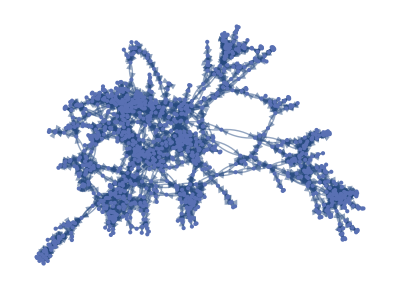
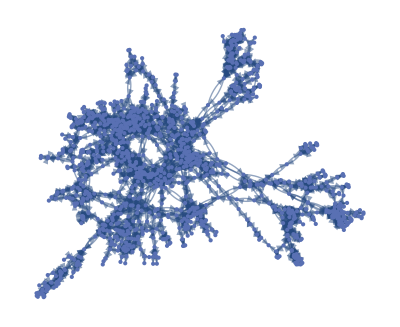
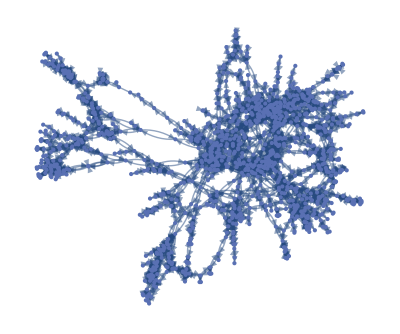
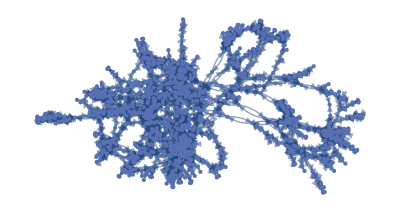
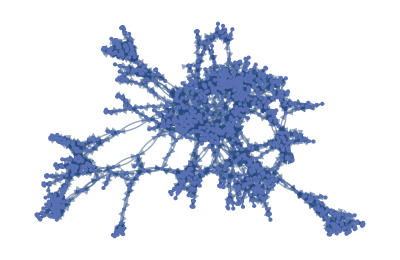
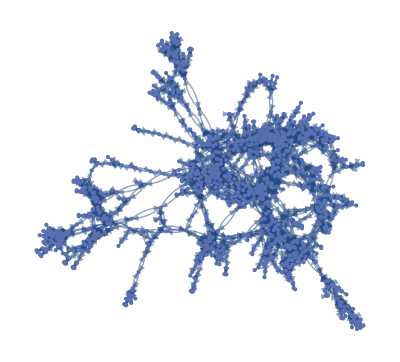
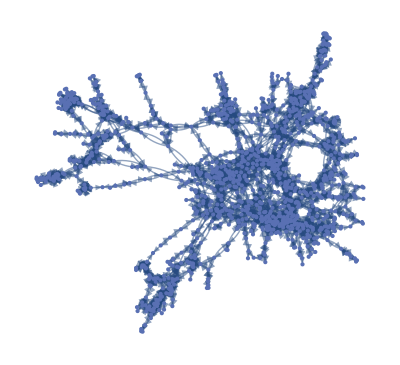
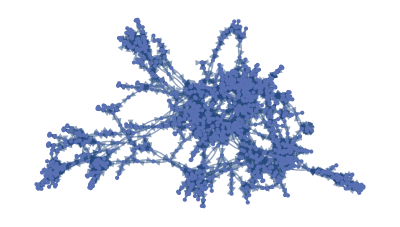
<|crave→-Graphics-,crate→-Graphics-,plate→-Graphics-,carve→-Graphics-,crape→-Graphics-,crane→-Graphics-,prate→-Graphics-,craze→-Graphics-,calve→-Graphics-,plane→-Graphics-|>

```mathematica
TakeLargestBy[AssociationMap[NestGraph[(word↦Select[DamerauLevenshteinDistance[#,word]==1&][wordList5Letters]),#,10]&,wordList5Letters],VertexCount,10]
```

```mathematica
VertexCount@-Graphics-
```

1186

```mathematica
EdgeCount@-Graphics-
```

3947

```mathematica
VertexCount/@<|"crave"->-Graphics-,"crate"->-Graphics-,"plate"->-Graphics-,"carve"->-Graphics-,"crape"->-Graphics-,"crane"->-Graphics-,"prate"->-Graphics-,"craze"->-Graphics-,"calve"->-Graphics-,"plane"->-Graphics-|>
```

<|crave→1186,crate→1177,plate→1167,carve→1165,crape→1162,crane→1152,prate→1131,craze→1127,calve→1122,plane→1113|>

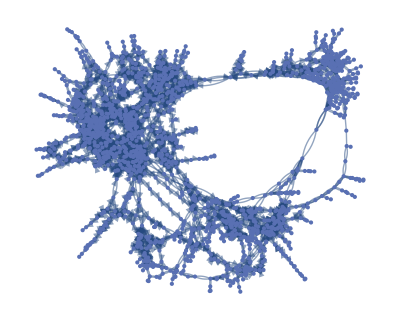

```mathematica
NestGraph[(word↦Select[DamerauLevenshteinDistance[#,word]==1&][wordList5Letters]),#,16]&["crave"]
```

```mathematica
VertexCount[%183]
```

1748

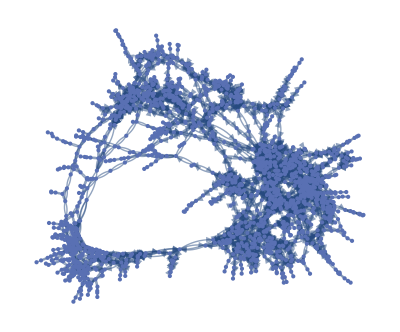

```mathematica
NestGraph[(word↦Select[DamerauLevenshteinDistance[#,word]==1&][wordList5Letters]),#,18]&["crave"]
```

```mathematica
VertexCount[%185]
```

1777

```mathematica
NestGraph[(word↦Select[DamerauLevenshteinDistance[#,word]==1&][wordList5Letters]),#,24]&["crave"]
```

-Graphics-

```mathematica
VertexCount[%187]
```

1785

```mathematica
NestGraph[(word↦Select[DamerauLevenshteinDistance[#,word]==1&][wordList5Letters]),#,48]&["crave"]
```

-Graphics-

```mathematica
VertexCount[%189]
```

1785

```mathematica
NestGraph[(word↦Select[DamerauLevenshteinDistance[#,word]==1&][wordList5Letters]),#,20]&["crave"]
```

-Graphics-

```mathematica
VertexCount[%192]
```

1785

```mathematica
NestGraph[(word↦Select[DamerauLevenshteinDistance[#,word]==1&][wordList5Letters]),#,19]&["crave"]
```

-Graphics-

```mathematica
VertexCount[%194]
```

1783

```mathematica
largest5LetterWordGraph=NestGraph[(word↦Select[DamerauLevenshteinDistance[#,word]==1&][wordList5Letters]),#,20]&["crave"]
```

-Graphics-